## Tensor Rank

```mathematica
TensorRank[{1,2}]
```

1

```mathematica
TensorRank[{{1,2},{3,4}}]
```

2

```mathematica
TensorRank[{{{1,2},{3,4}},{{5,6},{7,8}}}]
```

3

```mathematica
TensorRank[RandomReal[{-1,1},{2,2,2}]]
```

3

```mathematica
inds[s_]:=Rest[Apply[List,s]];
```

```mathematica
sind[list_]:=Apply[Subscript,Prepend[list,s]];
```

```mathematica
sigmaind[list_]:=Apply[Subscript,Prepend[list,σ]];
```

## Signature Tensors

#### Level 1

```mathematica
Table[sigmaind[{i}],{i,1,2}]
```

{σ_1,σ_2}

#### Level 2

```mathematica
Table[sigmaind[{i,j}],{i,1,2},{j,1,2}]
```

{{σ_(1,1),σ_(1,2)},{σ_(2,1),σ_(2,2)}}

#### Level 3

```mathematica
Table[sigmaind[{i,j,k}],{i,1,2},{j,1,2},{k,1,2}]
```

{{{σ_(1,1,1),σ_(1,1,2)},{σ_(1,2,1),σ_(1,2,2)}},{{σ_(2,1,1),σ_(2,1,2)},{σ_(2,2,1),σ_(2,2,2)}}}

```mathematica
{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

{{{s_1^3/6,s_(1,1,2)},{s_1 s_(1,2)-2 s_(1,1,2),s_(1,2,2)}},{{1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2),s_2 s_(1,2)-2 s_(1,2,2)},{1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2),s_2^3/6}}}

```mathematica
S3fromcore[{s1_,s2_,s12_,s112_,s122_}]:=Module[
{σ111,σ112,σ121,σ122,σ211,σ212,σ221,σ222},
σ111=s1^3/6;σ222=s2^3/6;
σ121=s1 s12-2s112;σ212=s2 s12-2s122;
σ211=1/2 (s1^2 s2-2 s1 s12)+s112;σ221=1/2 (s1 s2^2-2 s2 s12)+s122;
σ112=s112;σ122=s122;
{{{σ111,σ112},{σ121,σ122}},{{σ211,σ212},{σ221,σ222}}}];
```

```mathematica
S3corefromS3[{{{σ111_,σ112_},{σ121_,σ122_}},{{σ211_,σ212_},{σ221_,σ222_}}}]:=Module[
{s1,s2,s12,s112,s122},
s1=CubeRoot[6σ111];s2=CubeRoot[6σ222];
s112=σ112;s122=σ122;
 s12=(σ121+2s112)/s1;
{{{σ111,σ112},{σ121,σ122}},{{1/2 (s1^2 s2-2 s1 s12)+s112,s2 s12-2s122},{1/2 (s1^2 s2-2 s1 s12)+s112,σ222}}}];
```

## 3-way arrays

```mathematica
TensorProduct[{Subscript[a, 1],Subscript[a, 2]},{Subscript[b, 1],Subscript[b, 2]},{Subscript[c, 1],Subscript[c, 2]}]
```

{{{a_1 b_1 c_1,a_1 b_1 c_2},{a_1 b_2 c_1,a_1 b_2 c_2}},{{a_2 b_1 c_1,a_2 b_1 c_2},{a_2 b_2 c_1,a_2 b_2 c_2}}}

```mathematica
Table[∑_(r=1)^2 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)}}}

```mathematica
Table[∑_(r=1)^3 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)+a_(1,3) b_(1,3) c_(1,3),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)+a_(1,3) b_(1,3) c_(2,3)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)+a_(1,3) b_(2,3) c_(1,3),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)+a_(1,3) b_(2,3) c_(2,3)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)+a_(2,3) b_(1,3) c_(1,3),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)+a_(2,3) b_(1,3) c_(2,3)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)+a_(2,3) b_(2,3) c_(1,3),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)+a_(2,3) b_(2,3) c_(2,3)}}}

```mathematica
tenr={{{1,2},{3,4}},{{5,6},{7,8}}}
```

{{{1,2},{3,4}},{{5,6},{7,8}}}

```mathematica
(*fibers1[ten_]:=Table[Part[ten,All,j,k],{j,1,Dimensions[ten][[2]]},{k,1,Dimensions[ten][[3]]}];
fibers2[ten_]:=Table[Part[ten,i,All,k],{i,1,Dimensions[ten][[1]]},{k,1,Dimensions[ten][[3]]}];
fibers3[ten_]:=Table[Part[ten,i,j,All],{i,1,Dimensions[ten][[1]]},{j,1,Dimensions[ten][[2]]}];*)
```

```mathematica
fibers1[ften_]:=Flatten[ften,{{2},{3},{1}}];
fibers2[ften_]:=Flatten[ften,{{1},{3},{2}}];
fibers3[ften_]:=Flatten[ften,{{1},{2},{3}}];
```

```mathematica
invertfiber1[ften_]:=Flatten[ften,{{3},{1},{2}}];
invertfiber2[ften_]:=Flatten[ften,{{1},{3},{2}}];
invertfiber3[ften_]:=Flatten[ften,{{1},{2},{3}}];
```

```mathematica
slicei[ten_]:=Table[Part[ten,i,All,All],{i,1,Dimensions[ten][[1]]}];
slicej[ten_]:=Table[Part[ten,All,j,All],{j,1,Dimensions[ten][[2]]}];
slicek[ten_]:=Table[Part[ten,All,All,k],{k,1,Dimensions[ten][[3]]}];
```

```mathematica
slicei[tenr]
```

{{{1,2},{3,4}},{{5,6},{7,8}}}

```mathematica
slicej[tenr]
```

{{{1,2},{5,6}},{{3,4},{7,8}}}

```mathematica
slicek[tenr]
```

{{{1,3},{5,7}},{{2,4},{6,8}}}

```mathematica
ten24X1={{1,4,7,10},{2,5,8,11},{3,6,9,12}};
```

```mathematica
ten24X2=ten24X1+12
```

{{13,16,19,22},{14,17,20,23},{15,18,21,24}}

```mathematica
ten24=MapThread[List,{ten24X1,ten24X2},2]
```

{{{1,13},{4,16},{7,19},{10,22}},{{2,14},{5,17},{8,20},{11,23}},{{3,15},{6,18},{9,21},{12,24}}}

```mathematica
slicek[ten24]=={ten24X1,ten24X2}
```

True

```mathematica
Dimensions[ten24]
```

{3,4,2}

```mathematica
unfold[ten_,n_]:=Module[{rng},
rng=Range[Length[Dimensions[ten]]];
Flatten[ten,{{n},Reverse[Complement[rng,{n}]]}]];
```

```mathematica
unfold[ten24,1]
```

{{1,4,7,10,13,16,19,22},{2,5,8,11,14,17,20,23},{3,6,9,12,15,18,21,24}}

```mathematica
unfold[ten24,2]
```

{{1,2,3,13,14,15},{4,5,6,16,17,18},{7,8,9,19,20,21},{10,11,12,22,23,24}}

```mathematica
unfold[ten24,3]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{13,14,15,16,17,18,19,20,21,22,23,24}}

```mathematica
U={{1,3,5},{2,4,6}}
```

{{1,3,5},{2,4,6}}

```mathematica
Dimensions[U]
```

{2,3}

```mathematica
Map[Dimensions,{ten24,fibers1[ten24]}]
```

{{3,4,2},{4,2,3}}

```mathematica
Map[Dimensions,{ten24,fibers2[ten24]}]
```

{{3,4,2},{3,2,4}}

```mathematica
Map[Dimensions,{ten24,fibers3[ten24]}]
```

{{3,4,2},{3,4,2}}

```mathematica
ten24==invertfiber1[fibers1[ten24]]
```

True

```mathematica
ten24==invertfiber2[fibers2[ten24]]
```

True

```mathematica
ten24==invertfiber3[fibers3[ten24]]
```

True

```mathematica
nmode3[ten_,mat_,n_]:=Module[{tendim,f,invf,fibersten,result},
tendim=Dimensions[ten];
f={fibers1,fibers2,fibers3}[[n]];
invf={invertfiber1,invertfiber2,invertfiber3}[[n]];
fibersten=f[ten];
result=Map[(mat.#)&,fibersten,{2}];
invf[result]
];
```

```mathematica
fibers1[ten24]
```

{{{1,2,3},{13,14,15}},{{4,5,6},{16,17,18}},{{7,8,9},{19,20,21}},{{10,11,12},{22,23,24}}}

```mathematica
nmode3[ten24,U,1]
```

{{{22,130},{49,157},{76,184},{103,211}},{{28,172},{64,208},{100,244},{136,280}}}

```mathematica
slicek[nmode3[ten24,U,1]]
```

{{{22,49,76,103},{28,64,100,136}},{{130,157,184,211},{172,208,244,280}}}

```mathematica
nmode3[ten24,{{1,2,3,4}},2]
```

{{{70,190}},{{80,200}},{{90,210}}}

```mathematica
Dimensions[nmode3[ten24,{{1,2,3,4}},2]]
```

{3,1,2}

```mathematica
Flatten[nmode3[ten24,{{1,2,3,4}},2],{{1,2},{3}}]
```

{{70,190},{80,200},{90,210}}

```mathematica
Dimensions[Flatten[nmode3[ten24,{{1,2,3,4}},2],{{1,2},{3}}]]
```

{3,2}

```mathematica
av ={1,2,3}; bv={4,5};
KroneckerProduct[av,bv]==TensorProduct[av,bv]
KroneckerProduct[av,bv]==Outer[Times,av,bv]
```

True

True

```mathematica
am={{1,2},{3,4}};bm={{5,6},{7,8},{9,10}};
KroneckerProduct[am,bm]==ArrayFlatten[TensorProduct[am,bm]]
KroneckerProduct[am,bm]==Flatten[TensorProduct[am,bm],{{1,3},{2,4}}]
```

True

True

```mathematica
TensorProduct[am,bm]
```

{{{{5,6},{7,8},{9,10}},{{10,12},{14,16},{18,20}}},{{{15,18},{21,24},{27,30}},{{20,24},{28,32},{36,40}}}}

```mathematica
KroneckerProduct[am,bm]
```

{{5,6,10,12},{7,8,14,16},{9,10,18,20},{15,18,20,24},{21,24,28,32},{27,30,36,40}}

```mathematica
Dimensions[TensorProduct[am,bm]]
```

{2,2,3,2}

```mathematica
Dimensions[KroneckerProduct[am,bm]]
```

{6,4}

```mathematica
av=Array[Subscript[a, ##]&,{2,5}];
MatrixForm[av]
bv=Array[Subscript[b, ##]&,{3,4}];
MatrixForm[bv]
MatrixForm[KroneckerProduct[av,bv]]
Dimensions[KroneckerProduct[av,bv]]
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5))

(b_(1,1) | b_(1,2) | b_(1,3) | b_(1,4)
b_(2,1) | b_(2,2) | b_(2,3) | b_(2,4)
b_(3,1) | b_(3,2) | b_(3,3) | b_(3,4))

(a_(1,1) b_(1,1) | a_(1,1) b_(1,2) | a_(1,1) b_(1,3) | a_(1,1) b_(1,4) | a_(1,2) b_(1,1) | a_(1,2) b_(1,2) | a_(1,2) b_(1,3) | a_(1,2) b_(1,4) | a_(1,3) b_(1,1) | a_(1,3) b_(1,2) | a_(1,3) b_(1,3) | a_(1,3) b_(1,4) | a_(1,4) b_(1,1) | a_(1,4) b_(1,2) | a_(1,4) b_(1,3) | a_(1,4) b_(1,4) | a_(1,5) b_(1,1) | a_(1,5) b_(1,2) | a_(1,5) b_(1,3) | a_(1,5) b_(1,4)
a_(1,1) b_(2,1) | a_(1,1) b_(2,2) | a_(1,1) b_(2,3) | a_(1,1) b_(2,4) | a_(1,2) b_(2,1) | a_(1,2) b_(2,2) | a_(1,2) b_(2,3) | a_(1,2) b_(2,4) | a_(1,3) b_(2,1) | a_(1,3) b_(2,2) | a_(1,3) b_(2,3) | a_(1,3) b_(2,4) | a_(1,4) b_(2,1) | a_(1,4) b_(2,2) | a_(1,4) b_(2,3) | a_(1,4) b_(2,4) | a_(1,5) b_(2,1) | a_(1,5) b_(2,2) | a_(1,5) b_(2,3) | a_(1,5) b_(2,4)
a_(1,1) b_(3,1) | a_(1,1) b_(3,2) | a_(1,1) b_(3,3) | a_(1,1) b_(3,4) | a_(1,2) b_(3,1) | a_(1,2) b_(3,2) | a_(1,2) b_(3,3) | a_(1,2) b_(3,4) | a_(1,3) b_(3,1) | a_(1,3) b_(3,2) | a_(1,3) b_(3,3) | a_(1,3) b_(3,4) | a_(1,4) b_(3,1) | a_(1,4) b_(3,2) | a_(1,4) b_(3,3) | a_(1,4) b_(3,4) | a_(1,5) b_(3,1) | a_(1,5) b_(3,2) | a_(1,5) b_(3,3) | a_(1,5) b_(3,4)
a_(2,1) b_(1,1) | a_(2,1) b_(1,2) | a_(2,1) b_(1,3) | a_(2,1) b_(1,4) | a_(2,2) b_(1,1) | a_(2,2) b_(1,2) | a_(2,2) b_(1,3) | a_(2,2) b_(1,4) | a_(2,3) b_(1,1) | a_(2,3) b_(1,2) | a_(2,3) b_(1,3) | a_(2,3) b_(1,4) | a_(2,4) b_(1,1) | a_(2,4) b_(1,2) | a_(2,4) b_(1,3) | a_(2,4) b_(1,4) | a_(2,5) b_(1,1) | a_(2,5) b_(1,2) | a_(2,5) b_(1,3) | a_(2,5) b_(1,4)
a_(2,1) b_(2,1) | a_(2,1) b_(2,2) | a_(2,1) b_(2,3) | a_(2,1) b_(2,4) | a_(2,2) b_(2,1) | a_(2,2) b_(2,2) | a_(2,2) b_(2,3) | a_(2,2) b_(2,4) | a_(2,3) b_(2,1) | a_(2,3) b_(2,2) | a_(2,3) b_(2,3) | a_(2,3) b_(2,4) | a_(2,4) b_(2,1) | a_(2,4) b_(2,2) | a_(2,4) b_(2,3) | a_(2,4) b_(2,4) | a_(2,5) b_(2,1) | a_(2,5) b_(2,2) | a_(2,5) b_(2,3) | a_(2,5) b_(2,4)
a_(2,1) b_(3,1) | a_(2,1) b_(3,2) | a_(2,1) b_(3,3) | a_(2,1) b_(3,4) | a_(2,2) b_(3,1) | a_(2,2) b_(3,2) | a_(2,2) b_(3,3) | a_(2,2) b_(3,4) | a_(2,3) b_(3,1) | a_(2,3) b_(3,2) | a_(2,3) b_(3,3) | a_(2,3) b_(3,4) | a_(2,4) b_(3,1) | a_(2,4) b_(3,2) | a_(2,4) b_(3,3) | a_(2,4) b_(3,4) | a_(2,5) b_(3,1) | a_(2,5) b_(3,2) | a_(2,5) b_(3,3) | a_(2,5) b_(3,4))

{6,20}

```mathematica
KroPro[A_,B_]:=Flatten[TensorProduct[A,B],{{1,3},{2,4}}];
```

```mathematica
KhaRaoPro[A_,B_]:=Flatten[Table[KroneckerProduct[A[[All,k]],B[[All,k]]],{k,1,Dimensions[A][[2]]}],{{2,3},{1}}]
```

```mathematica
PseudoInverse[m]
```

```mathematica
MatrixForm[KroPro[av,bv]]
```

(a_(1,1) b_(1,1) | a_(1,1) b_(1,2) | a_(1,1) b_(1,3) | a_(1,1) b_(1,4) | a_(1,2) b_(1,1) | a_(1,2) b_(1,2) | a_(1,2) b_(1,3) | a_(1,2) b_(1,4) | a_(1,3) b_(1,1) | a_(1,3) b_(1,2) | a_(1,3) b_(1,3) | a_(1,3) b_(1,4) | a_(1,4) b_(1,1) | a_(1,4) b_(1,2) | a_(1,4) b_(1,3) | a_(1,4) b_(1,4) | a_(1,5) b_(1,1) | a_(1,5) b_(1,2) | a_(1,5) b_(1,3) | a_(1,5) b_(1,4)
a_(1,1) b_(2,1) | a_(1,1) b_(2,2) | a_(1,1) b_(2,3) | a_(1,1) b_(2,4) | a_(1,2) b_(2,1) | a_(1,2) b_(2,2) | a_(1,2) b_(2,3) | a_(1,2) b_(2,4) | a_(1,3) b_(2,1) | a_(1,3) b_(2,2) | a_(1,3) b_(2,3) | a_(1,3) b_(2,4) | a_(1,4) b_(2,1) | a_(1,4) b_(2,2) | a_(1,4) b_(2,3) | a_(1,4) b_(2,4) | a_(1,5) b_(2,1) | a_(1,5) b_(2,2) | a_(1,5) b_(2,3) | a_(1,5) b_(2,4)
a_(1,1) b_(3,1) | a_(1,1) b_(3,2) | a_(1,1) b_(3,3) | a_(1,1) b_(3,4) | a_(1,2) b_(3,1) | a_(1,2) b_(3,2) | a_(1,2) b_(3,3) | a_(1,2) b_(3,4) | a_(1,3) b_(3,1) | a_(1,3) b_(3,2) | a_(1,3) b_(3,3) | a_(1,3) b_(3,4) | a_(1,4) b_(3,1) | a_(1,4) b_(3,2) | a_(1,4) b_(3,3) | a_(1,4) b_(3,4) | a_(1,5) b_(3,1) | a_(1,5) b_(3,2) | a_(1,5) b_(3,3) | a_(1,5) b_(3,4)
a_(2,1) b_(1,1) | a_(2,1) b_(1,2) | a_(2,1) b_(1,3) | a_(2,1) b_(1,4) | a_(2,2) b_(1,1) | a_(2,2) b_(1,2) | a_(2,2) b_(1,3) | a_(2,2) b_(1,4) | a_(2,3) b_(1,1) | a_(2,3) b_(1,2) | a_(2,3) b_(1,3) | a_(2,3) b_(1,4) | a_(2,4) b_(1,1) | a_(2,4) b_(1,2) | a_(2,4) b_(1,3) | a_(2,4) b_(1,4) | a_(2,5) b_(1,1) | a_(2,5) b_(1,2) | a_(2,5) b_(1,3) | a_(2,5) b_(1,4)
a_(2,1) b_(2,1) | a_(2,1) b_(2,2) | a_(2,1) b_(2,3) | a_(2,1) b_(2,4) | a_(2,2) b_(2,1) | a_(2,2) b_(2,2) | a_(2,2) b_(2,3) | a_(2,2) b_(2,4) | a_(2,3) b_(2,1) | a_(2,3) b_(2,2) | a_(2,3) b_(2,3) | a_(2,3) b_(2,4) | a_(2,4) b_(2,1) | a_(2,4) b_(2,2) | a_(2,4) b_(2,3) | a_(2,4) b_(2,4) | a_(2,5) b_(2,1) | a_(2,5) b_(2,2) | a_(2,5) b_(2,3) | a_(2,5) b_(2,4)
a_(2,1) b_(3,1) | a_(2,1) b_(3,2) | a_(2,1) b_(3,3) | a_(2,1) b_(3,4) | a_(2,2) b_(3,1) | a_(2,2) b_(3,2) | a_(2,2) b_(3,3) | a_(2,2) b_(3,4) | a_(2,3) b_(3,1) | a_(2,3) b_(3,2) | a_(2,3) b_(3,3) | a_(2,3) b_(3,4) | a_(2,4) b_(3,1) | a_(2,4) b_(3,2) | a_(2,4) b_(3,3) | a_(2,4) b_(3,4) | a_(2,5) b_(3,1) | a_(2,5) b_(3,2) | a_(2,5) b_(3,3) | a_(2,5) b_(3,4))

```mathematica
TensorProduct[av,bv]
```

{{{{a_(1,1) b_(1,1),a_(1,1) b_(1,2),a_(1,1) b_(1,3),a_(1,1) b_(1,4)},{a_(1,1) b_(2,1),a_(1,1) b_(2,2),a_(1,1) b_(2,3),a_(1,1) b_(2,4)},{a_(1,1) b_(3,1),a_(1,1) b_(3,2),a_(1,1) b_(3,3),a_(1,1) b_(3,4)}},{{a_(1,2) b_(1,1),a_(1,2) b_(1,2),a_(1,2) b_(1,3),a_(1,2) b_(1,4)},{a_(1,2) b_(2,1),a_(1,2) b_(2,2),a_(1,2) b_(2,3),a_(1,2) b_(2,4)},{a_(1,2) b_(3,1),a_(1,2) b_(3,2),a_(1,2) b_(3,3),a_(1,2) b_(3,4)}},{{a_(1,3) b_(1,1),a_(1,3) b_(1,2),a_(1,3) b_(1,3),a_(1,3) b_(1,4)},{a_(1,3) b_(2,1),a_(1,3) b_(2,2),a_(1,3) b_(2,3),a_(1,3) b_(2,4)},{a_(1,3) b_(3,1),a_(1,3) b_(3,2),a_(1,3) b_(3,3),a_(1,3) b_(3,4)}},{{a_(1,4) b_(1,1),a_(1,4) b_(1,2),a_(1,4) b_(1,3),a_(1,4) b_(1,4)},{a_(1,4) b_(2,1),a_(1,4) b_(2,2),a_(1,4) b_(2,3),a_(1,4) b_(2,4)},{a_(1,4) b_(3,1),a_(1,4) b_(3,2),a_(1,4) b_(3,3),a_(1,4) b_(3,4)}},{{a_(1,5) b_(1,1),a_(1,5) b_(1,2),a_(1,5) b_(1,3),a_(1,5) b_(1,4)},{a_(1,5) b_(2,1),a_(1,5) b_(2,2),a_(1,5) b_(2,3),a_(1,5) b_(2,4)},{a_(1,5) b_(3,1),a_(1,5) b_(3,2),a_(1,5) b_(3,3),a_(1,5) b_(3,4)}}},{{{a_(2,1) b_(1,1),a_(2,1) b_(1,2),a_(2,1) b_(1,3),a_(2,1) b_(1,4)},{a_(2,1) b_(2,1),a_(2,1) b_(2,2),a_(2,1) b_(2,3),a_(2,1) b_(2,4)},{a_(2,1) b_(3,1),a_(2,1) b_(3,2),a_(2,1) b_(3,3),a_(2,1) b_(3,4)}},{{a_(2,2) b_(1,1),a_(2,2) b_(1,2),a_(2,2) b_(1,3),a_(2,2) b_(1,4)},{a_(2,2) b_(2,1),a_(2,2) b_(2,2),a_(2,2) b_(2,3),a_(2,2) b_(2,4)},{a_(2,2) b_(3,1),a_(2,2) b_(3,2),a_(2,2) b_(3,3),a_(2,2) b_(3,4)}},{{a_(2,3) b_(1,1),a_(2,3) b_(1,2),a_(2,3) b_(1,3),a_(2,3) b_(1,4)},{a_(2,3) b_(2,1),a_(2,3) b_(2,2),a_(2,3) b_(2,3),a_(2,3) b_(2,4)},{a_(2,3) b_(3,1),a_(2,3) b_(3,2),a_(2,3) b_(3,3),a_(2,3) b_(3,4)}},{{a_(2,4) b_(1,1),a_(2,4) b_(1,2),a_(2,4) b_(1,3),a_(2,4) b_(1,4)},{a_(2,4) b_(2,1),a_(2,4) b_(2,2),a_(2,4) b_(2,3),a_(2,4) b_(2,4)},{a_(2,4) b_(3,1),a_(2,4) b_(3,2),a_(2,4) b_(3,3),a_(2,4) b_(3,4)}},{{a_(2,5) b_(1,1),a_(2,5) b_(1,2),a_(2,5) b_(1,3),a_(2,5) b_(1,4)},{a_(2,5) b_(2,1),a_(2,5) b_(2,2),a_(2,5) b_(2,3),a_(2,5) b_(2,4)},{a_(2,5) b_(3,1),a_(2,5) b_(3,2),a_(2,5) b_(3,3),a_(2,5) b_(3,4)}}}}

```mathematica
av=Array[Subscript[a, ##]&,{2,4}]
bv=Array[Subscript[b, ##]&,{3,4}]
```

{{a_(1,1),a_(1,2),a_(1,3),a_(1,4)},{a_(2,1),a_(2,2),a_(2,3),a_(2,4)}}

{{b_(1,1),b_(1,2),b_(1,3),b_(1,4)},{b_(2,1),b_(2,2),b_(2,3),b_(2,4)},{b_(3,1),b_(3,2),b_(3,3),b_(3,4)}}

```mathematica
TensorProduct[av[[All,1]],bv[[All,1]]]
```

{{a_(1,1) b_(1,1),a_(1,1) b_(2,1),a_(1,1) b_(3,1)},{a_(2,1) b_(1,1),a_(2,1) b_(2,1),a_(2,1) b_(3,1)}}

```mathematica
Transpose[av]
Transpose[bv]
```

{{a_(1,1),a_(2,1)},{a_(1,2),a_(2,2)},{a_(1,3),a_(2,3)},{a_(1,4),a_(2,4)}}

{{b_(1,1),b_(2,1),b_(3,1)},{b_(1,2),b_(2,2),b_(3,2)},{b_(1,3),b_(2,3),b_(3,3)},{b_(1,4),b_(2,4),b_(3,4)}}

```mathematica
KroneckerProduct[{Subscript[a, 1,1],Subscript[a, 2,1]},{Subscript[b, 1,1],Subscript[b, 2,1],Subscript[b, 3,1]}]
```

{{a_(1,1) b_(1,1),a_(1,1) b_(2,1),a_(1,1) b_(3,1)},{a_(2,1) b_(1,1),a_(2,1) b_(2,1),a_(2,1) b_(3,1)}}

```mathematica
Table[KroneckerProduct[av[[All,k]],bv[[All,k]]],{k,1,4}]
```

{{{a_(1,1) b_(1,1),a_(1,1) b_(2,1),a_(1,1) b_(3,1)},{a_(2,1) b_(1,1),a_(2,1) b_(2,1),a_(2,1) b_(3,1)}},{{a_(1,2) b_(1,2),a_(1,2) b_(2,2),a_(1,2) b_(3,2)},{a_(2,2) b_(1,2),a_(2,2) b_(2,2),a_(2,2) b_(3,2)}},{{a_(1,3) b_(1,3),a_(1,3) b_(2,3),a_(1,3) b_(3,3)},{a_(2,3) b_(1,3),a_(2,3) b_(2,3),a_(2,3) b_(3,3)}},{{a_(1,4) b_(1,4),a_(1,4) b_(2,4),a_(1,4) b_(3,4)},{a_(2,4) b_(1,4),a_(2,4) b_(2,4),a_(2,4) b_(3,4)}}}

```mathematica
Flatten[Table[KroneckerProduct[av[[All,k]],bv[[All,k]]],{k,1,4}],{{2,3},{1}}]
```

{{a_(1,1) b_(1,1),a_(1,2) b_(1,2),a_(1,3) b_(1,3),a_(1,4) b_(1,4)},{a_(1,1) b_(2,1),a_(1,2) b_(2,2),a_(1,3) b_(2,3),a_(1,4) b_(2,4)},{a_(1,1) b_(3,1),a_(1,2) b_(3,2),a_(1,3) b_(3,3),a_(1,4) b_(3,4)},{a_(2,1) b_(1,1),a_(2,2) b_(1,2),a_(2,3) b_(1,3),a_(2,4) b_(1,4)},{a_(2,1) b_(2,1),a_(2,2) b_(2,2),a_(2,3) b_(2,3),a_(2,4) b_(2,4)},{a_(2,1) b_(3,1),a_(2,2) b_(3,2),a_(2,3) b_(3,3),a_(2,4) b_(3,4)}}

```mathematica
KhatriRaoProduct[av,bv]
```

{{a_(1,1) b_(1,1),a_(1,2) b_(1,2),a_(1,3) b_(1,3),a_(1,4) b_(1,4)},{a_(1,1) b_(2,1),a_(1,2) b_(2,2),a_(1,3) b_(2,3),a_(1,4) b_(2,4)},{a_(1,1) b_(3,1),a_(1,2) b_(3,2),a_(1,3) b_(3,3),a_(1,4) b_(3,4)},{a_(2,1) b_(1,1),a_(2,2) b_(1,2),a_(2,3) b_(1,3),a_(2,4) b_(1,4)},{a_(2,1) b_(2,1),a_(2,2) b_(2,2),a_(2,3) b_(2,3),a_(2,4) b_(2,4)},{a_(2,1) b_(3,1),a_(2,2) b_(3,2),a_(2,3) b_(3,3),a_(2,4) b_(3,4)}}

```mathematica
KhatriRaoProduct[av,bv]==KhaRaoPro[av,bv]
```

True

```mathematica
Table[∑_(r=1)^1 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,1) b_(1,1) c_(1,1),a_(1,1) b_(1,1) c_(2,1)},{a_(1,1) b_(2,1) c_(1,1),a_(1,1) b_(2,1) c_(2,1)}},{{a_(2,1) b_(1,1) c_(1,1),a_(2,1) b_(1,1) c_(2,1)},{a_(2,1) b_(2,1) c_(1,1),a_(2,1) b_(2,1) c_(2,1)}}}

```mathematica
Table[∑_(r=1)^2 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)}}}

```mathematica
Table[∑_(r=1)^3 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)+a_(1,3) b_(1,3) c_(1,3),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)+a_(1,3) b_(1,3) c_(2,3)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)+a_(1,3) b_(2,3) c_(1,3),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)+a_(1,3) b_(2,3) c_(2,3)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)+a_(2,3) b_(1,3) c_(1,3),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)+a_(2,3) b_(1,3) c_(2,3)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)+a_(2,3) b_(2,3) c_(1,3),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)+a_(2,3) b_(2,3) c_(2,3)}}}

```mathematica
AA=Table[Subscript[a, i,r],{i,1,2},{r,1,3}]
BB=Table[Subscript[b, i,r],{i,1,2},{r,1,3}]
CC=Table[Subscript[c, i,r],{i,1,2},{r,1,3}]
```

{{a_(1,1),a_(1,2),a_(1,3)},{a_(2,1),a_(2,2),a_(2,3)}}

{{b_(1,1),b_(1,2),b_(1,3)},{b_(2,1),b_(2,2),b_(2,3)}}

{{c_(1,1),c_(1,2),c_(1,3)},{c_(2,1),c_(2,2),c_(2,3)}}

```mathematica
unfold[Table[∑_(r=1)^3 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}],1]==AA.Transpose[KhaRaoPro[CC,BB]]
```

True

```mathematica
unfold[Table[∑_(r=1)^3 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}],2]==BB.Transpose[KhaRaoPro[CC,AA]]
```

True

```mathematica
unfold[Table[∑_(r=1)^3 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}],3]==CC.Transpose[KhaRaoPro[BB,AA]]
```

True

## Kruskal and Ten Berge

```mathematica
X1={{σ111,σ112},{σ121,σ122}};
X2={{σ211,σ212},{σ221,σ222}};
X={X1,X2};
```

```mathematica
X
```

{{{σ111,σ112},{σ121,σ122}},{{σ211,σ212},{σ221,σ222}}}

```mathematica
slicei[X]
```

{{{σ111,σ112},{σ121,σ122}},{{σ211,σ212},{σ221,σ222}}}

```mathematica
Map[Det,{slicei[X],slicej[X],slicek[X]},{2}]
```

{{-σ112 σ121+σ111 σ122,-σ212 σ221+σ211 σ222},{-σ112 σ211+σ111 σ212,-σ122 σ221+σ121 σ222},{-σ121 σ211+σ111 σ221,-σ122 σ212+σ112 σ222}}

```mathematica
discrim[mat_]:=(Tr[mat])^2-4Det[mat];
```

```mathematica
discrimten[ten_]:=discrim[ten[[2]]Inverse[ten[[1]]]];
```

```mathematica
FullSimplify[Map[discrimten,ComapApply[{slicei,slicej,slicek},{X}]]]
```

{(4 σ112 σ121 σ212 σ221+(σ122 σ211-σ111 σ222)^2)/(σ112 σ121-σ111 σ122)^2,(4 σ112 σ122 σ211 σ221+(σ121 σ212-σ111 σ222)^2)/(σ112 σ211-σ111 σ212)^2,(4 σ121 σ122 σ211 σ212+(σ112 σ221-σ111 σ222)^2)/(σ121 σ211-σ111 σ221)^2}

```mathematica
disc3x3[{{{σ111_,σ112_},{σ121_,σ122_}},{{σ211_,σ212_},{σ221_,σ222_}}}]:=If[And[(σ112 σ121-σ111 σ122)!=0,(σ112 σ211-σ111 σ212)!=0,(σ121 σ211-σ111 σ221)!=0],{(4 σ112 σ121 σ212 σ221+(σ122 σ211-σ111 σ222)^2)/(σ112 σ121-σ111 σ122)^2,(4 σ112 σ122 σ211 σ221+(σ121 σ212-σ111 σ222)^2)/(σ112 σ211-σ111 σ212)^2,(4 σ121 σ122 σ211 σ212+(σ112 σ221-σ111 σ222)^2)/(σ121 σ211-σ111 σ221)^2}];
```

```mathematica
checkdisc2all[ten_]:={ten,Map[(#>0)&,disc3x3[ten]]};
```

```mathematica
checkdisc3all[ten_]:={ten,Map[(#<0)&,disc3x3[ten]]};
```

```mathematica
kruskalpol[{{{σ111_,σ112_},{σ121_,σ122_}},{{σ211_,σ212_},{σ221_,σ222_}}}]:=
σ111^2 σ222^2+σ121^2 σ212^2+σ112^2 σ221^2+σ122^2 σ211^2+
4(σ111 σ122 σ212 σ221+σ112 σ121 σ211 σ222)-2(σ111 σ112 σ221 σ222+σ111 σ121 σ212 σ222+
σ111 σ122 σ211 σ222+σ112 σ121 σ212 σ221+
σ112 σ122 σ211 σ221+σ121 σ122 σ211 σ212);
```

```mathematica
kruskalpolcore[{s1_,s2_,s12_,s112_,s122_}]:=Module[
{σ111,σ112,σ121,σ122,σ211,σ212,σ221,σ222},
σ111=s1^3/6;σ222=s2^3/6;
σ121=s1 s12-2s112;σ212=s2 s12-2s122;
σ211=1/2 (s1^2 s2-2 s1 s12)+s112;σ221=1/2 (s1 s2^2-2 s2 s12)+s122;
σ112=s112;σ122=s122;
σ111^2 σ222^2+σ121^2 σ212^2+σ112^2 σ221^2+σ122^2 σ211^2+
4(σ111 σ122 σ212 σ221+σ112 σ121 σ211 σ222)-2(σ111 σ112 σ221 σ222+σ111 σ121 σ212 σ222+
σ111 σ122 σ211 σ222+σ112 σ121 σ212 σ221+
σ112 σ122 σ211 σ221+σ121 σ122 σ211 σ212)];
```

```mathematica
FullSimplify[kruskalpolcore[{s1,s2,s12,s112,s122}]]
```

((6 s1 s122+6 s112 s2+s1 s2 (-6 s12+s1 s2))^2 ((6 s12+s1 s2)^2-48 (s1 s122+s112 s2)))/1296

(6 s12+s1 s2)^2>48 (s1 s122+s112 s2)⇒Rank 2

```mathematica
SeedRandom[0];
tblrnd=Table[RandomReal[{-100,+100},{2,2,2}],10000000];
```

```mathematica
Timing[testtbl2=Map[Sign[kruskalpol[#]]&,tblrnd];]
```

{58.4918,Null}

```mathematica
Tally[testtbl2]
```

{{1,7697867},{-1,2302133}}

```mathematica
Timing[testtbl2cored=Map[Sign[kruskalpol[S3corefromS3[#]]]&,tblrnd];]
```

{175.384,Null}

```mathematica
Tally[testtbl2cored]
```

{{1,7560555},{-1,2439445}}

```mathematica
SeedRandom[0];
tblrndcore=Table[RandomReal[{-100,+100},{5}],10000000];
```

```mathematica
Timing[testtbl2core=Map[Sign[kruskalpolcore[#]]&,tblrndcore];]
```

{189.251,Null}

```mathematica
Tally[testtbl2core]
```

{{1,9437375},{-1,562625}}

## Tensor Decomposition Functions

```mathematica
KhatriRaoProduct[mats__]:=Module[{mList={mats}},
Flatten[MapThread[KroneckerProduct,Flatten[{mList},{{2},{4},{1},{3}}]],{{3,2},{1}}]];
```

```mathematica
factorsTotensor[factors_,dim_:{2,2,2}]:=ArrayReshape[Total[Apply[KhatriRaoProduct,factors],{2}],dim];
```

```mathematica
subfactors[factors_,dim_:{2,2,2}]:=Module[{rank,trnspf,subfactors},
rank=Last[Dimensions[factors[[1]]]];
trnspf=Map[Transpose,factors];
subfactors=Table[Map[#[[r]]&,trnspf],{r,1,rank}];
(*Map[{Norm[#],Normalize[#]}&,subfactors,{2}]*)
(*Map[{Min[#],#/Min[#]}&,subfactors,{2}]*)];
```

```mathematica
resubsubs[subf_]:=Module[{norms,vecs,signs,signorm,normt},
{norms,vecs}=Transpose[subf];
signs=Map[Sign[Total[#]]&,vecs];
signorm=Apply[Times,signs];
normt=signorm*Apply[Times,norms];
{normt,vecs/signs}];
```

```mathematica
factorsTotensorS[factors_,dim_:{2,2,2}]:=Module[{rank,trnspf,subfactors},
rank=Last[Dimensions[factors[[1]]]];
trnspf=Map[Transpose,factors];
subfactors=Table[Map[Transpose[{#[[r]]}]&,trnspf],{r,1,rank}];
Map[factorsTotensor[#,dim]&,subfactors]];
```

LSsol only works for order 3

```mathematica
LSsol[X_,n_,factors_]:=Module[{Xn,ind,f1,f2,krp,psi,newf},
Xn=unfold[X,n];
newf=factors;
ind=Reverse[Complement[Range[Length[Dimensions[X]]],{n}]];
f1=factors[[ind[[1]]]];
f2=factors[[ind[[2]]]];
krp=KhaRaoPro[f1,f2];
psi=PseudoInverse[(Transpose[f1].f1)*(Transpose[f2].f2)];
newf[[n]]=Xn.krp.psi;
newf
];
```

```mathematica
LSsol[{{{71,-5},{-16,-56}},{{-18,-22},{-100,-28}}},
1,
{{{146.0656284939514,-195.97071222819204,-138.2423542999322},{-52.130192170022546,-379.1792314783524,-11.016921103654601}},{{1.4273737555420634,-0.035884600753826046,1.0586827428779244},{0.7581118642916463,0.3197039467344258,1.4159128540033854}},{{0.36017708714677954,0.6995661934836075,0.061583153344347205},{0.251355209972703,0.09795379005643179,0.39693918260625566}}}]
```

{{{146.066,-195.971,-138.242},{-52.1302,-379.179,-11.0169}},{{1.42737,-0.0358846,1.05868},{0.758112,0.319704,1.41591}},{{0.360177,0.699566,0.0615832},{0.251355,0.0979538,0.396939}}}

```mathematica
errorcp[X_,factors_]:=Module[{dim},
dim=Dimensions[X];
Chop[SquaredEuclideanDistance[Flatten[X],Flatten[factorsTotensor[factors,dim]]]]];
```

```mathematica
errorcp[{{{71,-5},{-16,-56}},{{-18,-22},{-100,-28}}},
{{{146.0656284939514,-195.97071222819204,-138.2423542999322},{-52.130192170022546,-379.1792314783524,-11.016921103654601}},{{1.4273737555420634,-0.035884600753826046,1.0586827428779244},{0.7581118642916463,0.3197039467344258,1.4159128540033854}},{{0.36017708714677954,0.6995661934836075,0.061583153344347205},{0.251355209972703,0.09795379005643179,0.39693918260625566}}}]
```

0

```mathematica
initCP[X_,rank_:3]:=Module[{dim},
dim=Dimensions[X];
Table[RandomReal[{-1,+1},{dim[[n]],rank}],{n,1,Length[dim]}]];
```

```mathematica
initCP[{{{71,-5},{-16,-56}},{{-18,-22},{-100,-28}}}]
```

{{{-0.893482,0.520261,-0.968472},{-0.914069,0.799521,0.601473}},{{0.0724182,0.993622,0.582837},{-0.370045,0.396931,-0.95583}},{{-0.897341,-0.0207623,0.154203},{-0.561419,-0.796791,-0.125249}}}

```mathematica
esttensors[{s1_,s2_,s12_,s112_,s122_}]:={
{{{(s1^3/6),(s1^3/6)(s122)/(s1 s12-2 s112)},{(s1 s12-2 s112),(s122)}},{{(s1^3/6)(1/2 s1 s2^2- s2 s12+s122)/(s1 s12-2 s112),(s1^3/6)(s122)(1/2 s1 s2^2- s2 s12+s122)/(s1 s12-2 s112)^2},{(1/2 s1 s2^2- s2 s12+s122),(s122)(1/2 s1 s2^2- s2 s12+s122)/(s1 s12-2 s112)}}},
{{{(s112)(1/2 s1^2 s2- s1 s12+s112)/(s2 s12-2 s122),(s112)},{(s2^3/6)(s112)(1/2 s1^2 s2- s1 s12+s112)/(s2 s12-2 s122)^2,(s2^3/6)(s112)/(s2 s12-2 s122)}},{{(1/2 s1^2 s2- s1 s12+s112),(s2 s12-2 s122)},{(s2^3/6)(1/2 s1^2 s2- s1 s12+s112)/(s2 s12-2 s122),(s2^3/6)}}}
};
```

```mathematica
{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

```mathematica
esttensorsX[X_]:=Module[{r1a,r1bi,r1c,r2ai,r2b,r2ci},
r1a=X[[2]][[2]][[1]]/X[[1]][[2]][[1]];
r1bi=X[[1]][[1]][[1]]/X[[1]][[2]][[1]];
r1c=X[[1]][[2]][[2]]/X[[1]][[2]][[1]];
r2ai=X[[2]][[2]][[1]]/X[[1]][[2]][[1]];
r2b=X[[2]][[2]][[1]]/X[[1]][[2]][[1]];
r2ci=X[[2]][[2]][[1]]/X[[1]][[2]][[1]];
{
{{{X[[1]][[1]][[1]],X[[1]][[2]][[1]]*r1bi*r1c},{X[[1]][[2]][[1]],X[[1]][[2]][[2]]}},{{X[[1]][[2]][[1]]*r1a*r1bi,X[[1]][[2]][[1]]*r1a*r1bi*r1c},{X[[2]][[2]][[1]],X[[1]][[2]][[1]]*r1a*r1c}}},
{{{X[[2]][[1]][[2]]*r2ai*r2ci,X[[1]][[1]][[2]]},{X[[2]][[1]][[2]]*r2ai*r2b*r2ci,X[[2]][[1]][[2]]*r2ai*r2b}},{{X[[2]][[1]][[1]],X[[2]][[1]][[2]]},{X[[2]][[1]][[2]]*r2b*r2ci,X[[2]][[2]][[2]]}}}
}];
```

```mathematica
cpmaxiter=10000;
cptol=10^-8;
```

```mathematica
solveCP[X_,rank_:3,maxiter_:cpmaxiter,mintol_:cptol]:=Module[{dim,ord,xfacs,niter,err},
dim=Dimensions[X];
ord=Length[dim];
xfacs=initCP[X,rank];
niter=0;
err={errorcp[X,xfacs]};
While[And[Last[err]>mintol,niter<maxiter],
Do[xfacs=LSsol[X,n,xfacs],{n,1,ord}];
niter++;
AppendTo[err,errorcp[X,xfacs]];
(*Print[{niter,errorcp[X,xfacs]}]*)];
{xfacs,niter,err}
];
```

```mathematica
dividetensor[A_,B_]:=MapThread[(#1/#2)&,{A,B},3];
```

```mathematica
Timing[sol3=solveCP[{{{71,-5},{-16,-56}},{{-18,-22},{-100,-28}}},3];]
```

{0.001305,Null}

```mathematica
Timing[sol2=solveCP[{{{71,-5},{-16,-56}},{{-18,-22},{-100,-28}}},2];]
```

{0.938014,Null}

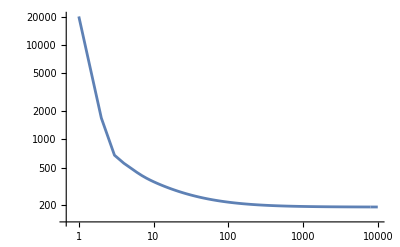

```mathematica
ListLogLogPlot[Last[sol2],PlotRange->All,Joined->True]
```

```mathematica
Timing[testtablesigs1same=Table[{j,
t=S3fromcore[{3,5,7,-2,-4}];
r=If[Sign[kruskalpol[t]]==1,2,3];
sol=solveCP[t,r];
rec=factorsTotensor[sol[[1]]];
(*subs=subfactors[sol[[1]]];
subsf=SortBy[Map[resubsubs,subs],Last];*)
recs=Sort[factorsTotensorS[sol[[1]]]];
r,sol,recs,(*subsf,*)rec,t},
{j,1,5,1}];]
```

{0.01697,Null}

```mathematica
Timing[testtablesigs1same3=Table[{j,
t=S3fromcore[{3,5,7,-2,-4}];
r=3;
sol=solveCP[t,r];
rec=factorsTotensor[sol[[1]]];
(*subs=subfactors[sol[[1]]];
subsf=SortBy[Map[resubsubs,subs],Last];*)
recs=Sort[factorsTotensorS[sol[[1]]]];
r,sol,recs,(*subsf,*)rec,t},
{j,1,5,1}];]
```

{0.007451,Null}

```mathematica
Grid[Map[{#[[1]],N[kruskalpol[#[[6]]]],#[[2]],Last[#[[3]][[3]]],#[[3]][[2]],#[[3]][[1]],(*Map[MatrixForm,#[[5]],{2}],*)Map[MatrixForm,#[[4]],{2}],N[Norm[Flatten[#[[6]]]]],Map[MatrixForm,#[[5]]],Map[MatrixForm,N[#[[6]]]]}&,testtablesigs1same],Frame->All]
```

1 | 957892. | 2 | 9.49574×10^-9 | 11 | {{{-31.852,4.44682},{1.75693,-136.241}},{{0.119142,1.12636},{0.66301,0.541327}},{{-1.18363,0.00164375},{0.157494,-0.279995}}} | {{(0.00823312 | -1.40242
0.00395682 | -0.674),(-0.252244 | 42.967
-0.121228 | 20.6499)},{(4.49175 | -0.597674
24.996 | -3.32598),(-0.247761 | 0.0329672
-1.37876 | 0.183458)}} | 54.3211 | {(4.49999 | -2.00009
25. | -3.99998),(-0.500006 | 43.
-1.49999 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
2 | 957892. | 2 | 1.45582×10^-9 | 18 | {{{-45.665,-5.07613},{2.51895,155.535}},{{0.0885094,0.250882},{0.492541,0.120573}},{{-1.11134,-0.00646348},{0.147878,1.10113}}} | {{(0.00823131 | -1.4023
0.00395595 | -0.673942),(-0.252211 | 42.967
-0.121212 | 20.6499)},{(4.49177 | -0.597691
24.996 | -3.32606),(-0.247773 | 0.0329696
-1.37882 | 0.183471)}} | 54.3211 | {(4.50001 | -1.99999
25. | -4.),(-0.499984 | 43.
-1.50003 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
3 | 957892. | 2 | 7.49009×10^-9 | 12 | {{{164.008,3.46569},{-9.04608,-106.185}},{{0.0758813,-0.476025},{0.42227,-0.228777}},{{0.360925,-0.00499104},{-0.0480253,0.850047}}} | {{(0.00823401 | -1.40237
0.00395725 | -0.673977),(-0.25228 | 42.967
-0.121246 | 20.6499)},{(4.49175 | -0.597679
24.996 | -3.32601),(-0.247749 | 0.0329659
-1.37869 | 0.183451)}} | 54.3211 | {(4.49999 | -2.00005
25. | -3.99999),(-0.50003 | 43.
-1.49994 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
4 | 957892. | 2 | 1.94823×10^-9 | 41 | {{{3.5725,178.771},{-109.464,-9.86131}},{{-0.293431,0.0250014},{-0.141022,0.139129}},{{-0.00785205,1.00498},{1.3377,-0.133726}}} | {{(0.00823118 | -1.40229
0.00395589 | -0.673939),(-0.252208 | 42.967
-0.121211 | 20.6499)},{(4.49178 | -0.597692
24.996 | -3.32606),(-0.247774 | 0.0329697
-1.37883 | 0.183472)}} | 54.3211 | {(4.50001 | -1.99998
25. | -4.),(-0.499982 | 43.
-1.50004 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
5 | 957892. | 2 | 7.57032×10^-9 | 16 | {{{134.417,-4.4994},{-7.41408,137.87}},{{-0.0990609,-0.287952},{-0.55126,-0.138389}},{{-0.337334,0.00635439},{0.0448874,-1.08229}}} | {{(0.00823284 | -1.40223
0.00395669 | -0.673911),(-0.252269 | 42.967
-0.12124 | 20.6499)},{(4.49177 | -0.597698
24.996 | -3.3261),(-0.247754 | 0.0329673
-1.37871 | 0.183459)}} | 54.3211 | {(4.5 | -1.99993
25. | -4.00001),(-0.500023 | 43.
-1.49995 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}

```mathematica
Grid[Map[{#[[1]],N[kruskalpol[#[[6]]]],#[[2]],Last[#[[3]][[3]]],#[[3]][[2]],#[[3]][[1]],(*Map[MatrixForm,#[[5]],{2}],*)Map[MatrixForm,#[[4]],{2}],N[Norm[Flatten[#[[6]]]]],Map[MatrixForm,#[[5]]],Map[MatrixForm,N[#[[6]]]]}&,testtablesigs1same3],Frame->All]
```

1 | 957892. | 3 | 1.02346×10^-9 | 9 | {{{80.4323,58.4442,-55.462},{19.3077,-42.2212,7.83677}},{{-0.548168,0.917018,0.533687},{-0.00970476,0.60172,0.854083}},{{0.181032,-0.102094,-0.606547},{-0.72303,-0.981241,-0.63212}}} | {{(-7.98176 | 31.8787
-0.141309 | 0.56438),(-1.91602 | 7.65246
-0.0339212 | 0.135479)},{(-5.47164 | -52.589
-3.59033 | -34.5074),(3.95282 | 37.9913
2.59372 | 24.9288)},{(17.9534 | 18.7104
28.7316 | 29.943),(-2.53681 | -2.64377
-4.05977 | -4.23094)}} | 54.3211 | {(4.5 | -2.
25. | -4.),(-0.500014 | 43.
-1.49997 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
2 | 957892. | 3 | 5.84316×10^-10 | 4 | {{{56.049,2.48644,-0.340398},{-68.8684,41.5533,-59.9359}},{{0.101836,0.375537,0.925086},{0.468749,-1.60278,-0.736366}},{{0.867406,-0.571175,-0.261453},{-0.268626,-0.828538,-0.974739}}} | {{(-0.533335 | -0.773649
2.27626 | 3.30191),(-8.91308 | -12.9292
38.0407 | 55.1814)},{(0.0823309 | 0.306943
-0.0655351 | -0.244326),(14.4965 | 54.0452
-11.5391 | -43.0198)},{(4.951 | -1.53327
22.7893 | -7.05759),(-6.08339 | 1.88396
-28.0016 | 8.67178)}} | 54.3211 | {(4.5 | -1.99998
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
3 | 957892. | 3 | 3.03795×10^-9 | 6 | {{{-19.6942,9.4882,83.0481},{-21.3863,-65.6501,-162.04}},{{0.970811,0.98936,0.527137},{-0.28966,0.557203,0.434057}},{{0.851827,-1.23818,0.74032},{-0.179716,-0.614599,0.00761497}}} | {{(-16.2864 | 3.43605
4.85936 | -1.02521),(-17.6857 | 3.73128
5.27688 | -1.1133)},{(-11.6231 | -5.76939
-6.54609 | -3.24929),(80.4219 | 39.9191
45.2932 | 22.4823)},{(32.4095 | 0.333366
26.6867 | 0.274501),(-63.2362 | -0.650451
-52.0701 | -0.535596)}} | 54.3211 | {(4.5 | -1.99997
25. | -4.),(-0.499999 | 43.
-1.5 | 20.8334)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
4 | 957892. | 3 | 1.63733×10^-9 | 9 | {{{14.4945,-54.8006,-5.52398},{-1144.7,735.618,-1653.3}},{{-0.290418,-0.107788,0.0568226},{0.625537,-0.280794,-0.432707}},{{0.524432,1.18147,0.86394},{0.059823,-0.295758,0.00360456}}} | {{(-2.20758 | -0.251824
4.75495 | 0.542407),(174.343 | 19.8876
-375.519 | -42.8363)},{(-0.271179 | -0.00113143
2.06504 | 0.00861586),(-81.1629 | -0.338631
618.059 | 2.57869)},{(6.97877 | -1.74701
18.18 | -4.55103),(-93.6798 | 23.451
-244.04 | 61.0909)}} | 54.3211 | {(4.50001 | -1.99996
25. | -4.00001),(-0.5 | 43.
-1.5 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
5 | 957892. | 3 | 1.33961×10^-9 | 3 | {{{0.977915,128.488,-9.80126},{34.7951,-35.1835,-83.392}},{{1.69583,0.0362143,-0.327223},{-1.02826,0.188527,1.11482}},{{0.0470822,1.0009,-0.0733978},{0.987064,-0.384224,-0.576554}}} | {{(-0.235401 | -1.84912
0.80199 | 6.29979),(-2.00286 | -15.7329
6.82357 | 53.6004)},{(0.07808 | 1.63692
-0.0473436 | -0.992544),(2.77816 | 58.2433
-1.68453 | -35.3157)},{(4.65731 | -1.78784
24.2454 | -9.30724),(-1.2753 | 0.489558
-6.63904 | 2.54857)}} | 54.3211 | {(4.49999 | -2.00004
25. | -3.99999),(-0.5 | 43.
-1.5 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}

```mathematica
S3fromcore[{s1,s2,s12,s112,s122}]
```

```mathematica
tblsignats={
{3,5,7,-2,-4},
{0,5,7,-2,-4},
{2,5,7,-2,-4},
{3,5,7,-2,-4},
{4,5,7,-2,-4},
{25,5,7,-2,-4},
{3,0,7,-2,-4},
{3,4,7,-2,-4},
{3,5,7,-2,-4},
{3,6,7,-2,-4},
{3,25,7,-2,-4},
{3,5,0,-2,-4},
{3,5,6,-2,-4},
{3,5,7,-2,-4},
{3,5,8,-2,-4},
{3,5,25,-2,-4},
{3,5,7,0,-4},
{3,5,7,-1,-4},
{3,5,7,-2,-4},
{3,5,7,-3,-4},
{3,5,7,-25,-4},
{3,5,7,-2,0},
{3,5,7,-2,-3},
{3,5,7,-2,-4},
{3,5,7,-2,-5},
{3,5,7,-2,-25},
{3,5,7,0,0},
{3,5,0,0,0},
{3,3,0,-3,-3},
{3,3,1,-3,-3}};
```

```mathematica
Map[Sign[kruskalpol[S3fromcore[#]]]&,tblsignats]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Timing[testtablesigs=Table[{tblsignats[[j]],
t=S3fromcore[tblsignats[[j]]];
r=If[Sign[kruskalpol[t]]==1,2,3];
sol=solveCP[t,r];
rec=factorsTotensor[sol[[1]]];
(*subs=subfactors[sol[[1]]];*)
(*subsf=SortBy[Map[resubsubs,subs],Last];*)
recs=Sort[factorsTotensorS[sol[[1]]]];
r,sol,recs,(*subs,*)rec,t},
{j,1,Length[tblsignats]}];]
```

{2.37601,Null}

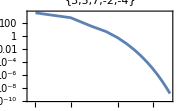
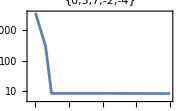
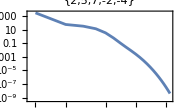
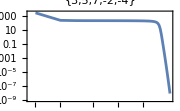
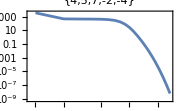
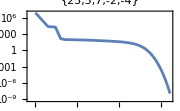
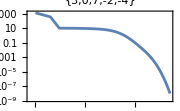
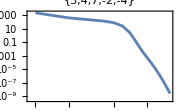

```mathematica
Table[ListLogLogPlot[Last[testtablesigs[[j]][[3]]],
PlotRange->All,Joined->True,Frame->True,
PlotLabel->tblsignats[[j]],ImageSize->Small],{j,1,Length[tblsignats]}]
```

```mathematica
|
```

```mathematica
{Subscript[b, 1,1]->Subscript[s, 1],Subscript[b, 2,1]->Subscript[s, 2],Subscript[b, 1,2]->Subscript[s, 1,1,2],Subscript[b, 2,2]->Subscript[s, 1,2,2],
Subscript[c, 1,1]->(1/2 Subscript[s, 1] Subscript[s, 2]-Subscript[s, 1,2]),Subscript[c, 1,2]->1,Subscript[c, 2,1]->0,Subscript[c, 2,2]->1,
Subscript[a, 1,1]->-Subscript[s, 1]/Subscript[s, 2],Subscript[a, 2,1]->1,Subscript[a, 1,2]->1,Subscript[a, 2,2]->1}
```

{{-s_1/s_2,1},{s_1,s_2}},{(1/2 s_1 s_2-s_(1,2)),0}
{{1,1},{s_(1,1,2),s_(1,2,2)},{1,1}}

```mathematica
Grid[Map[{#[[1]],N[kruskalpol[#[[6]]]],#[[2]],Last[#[[3]][[3]]],#[[3]][[2]],#[[3]][[1]],(*Map[MatrixForm,#[[5]],{2}],*)Map[MatrixForm,#[[4]],{2}],(*N[Norm[Flatten[#[[7]]]]],*)Map[MatrixForm,#[[5]]],Map[MatrixForm,N[#[[6]]]]}&,testtablesigs],Frame->All]
```

{3,5,7,-2,-4} | 957892. | 2 | 1.60676×10^-9 | 13 | {{{-1.4277,12.1599},{43.7438,-0.670749}},{{-1.11997,-0.219663},{-0.538256,-1.2224}},{{0.00514826,-1.68163},{-0.877025,0.223761}}} | {{(0.00823199 | -1.40235
0.00395628 | -0.673967),(-0.252222 | 42.967
-0.121218 | 20.6499)},{(4.49177 | -0.597684
24.996 | -3.32603),(-0.247769 | 0.0329687
-1.3788 | 0.183466)}} | {(4.5 | -2.00003
25. | -3.99999),(-0.499992 | 43.
-1.50002 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
{0,5,7,-2,-4} | 6233.33 | 2 | 8.07179 | 10000 | {{{4.48243,-7.03027},{-52.6541,83.4197}},{{7.42583,-4.68567},{5.75823,-2.95494}},{{0.667739,-0.662916},{0.106129,-0.21583}}} | {{(-21.8375 | -7.10976
-13.7715 | -4.48366),(259.119 | 84.3629
163.409 | 53.2021)},{(22.2262 | 3.53258
17.2349 | 2.73928),(-261.086 | -41.4964
-202.455 | -32.1777)}} | {(0.388724 | -3.57717
3.46346 | -1.74438),(-1.96714 | 42.8664
-39.0454 | 21.0244)} | {(0. | -2.
4. | -4.),(-2. | 43.
-39. | 20.8333)}
{2,5,7,-2,-4} | 504321. | 2 | 3.8885×10^-9 | 21 | {{{-1.65515,16.6476},{39.4109,-10.8752}},{{-1.44226,0.096223},{-0.630276,1.54934}},{{0.0927789,0.694112},{-0.754204,-0.124578}}} | {{(0.221478 | -1.80041
0.0967871 | -0.786787),(-5.27364 | 42.8696
-2.30461 | 18.7342)},{(1.11189 | -0.199559
17.9032 | -3.21323),(-0.726351 | 0.130364
-11.6954 | 2.09907)}} | {(1.33337 | -1.99997
18. | -4.00001),(-5.99999 | 43.
-14. | 20.8333)} | {(1.33333 | -2.
18. | -4.),(-6. | 43.
-14. | 20.8333)}
{3,5,7,-2,-4} | 957892. | 2 | 7.47×10^-9 | 41 | {{{-1.37137,-74.209},{42.0174,4.0936}},{{1.68062,0.229153},{0.807705,1.2752}},{{-0.00357132,-0.264141},{0.608465,0.0351471}}} | {{(0.00823104 | -1.40237
0.00395582 | -0.673975),(-0.25219 | 42.967
-0.121202 | 20.6499)},{(4.49177 | -0.597683
24.996 | -3.32602),(-0.24778 | 0.0329701
-1.37886 | 0.183473)}} | {(4.5 | -2.00005
25. | -3.99999),(-0.49997 | 43.
-1.50006 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
{4,5,7,-2,-4} | 1.39565×10^6 | 2 | 5.44687×10^-9 | 26 | {{{-1.12988,-44.7846},{62.3182,-10.074}},{{0.55453,0.289215},{0.277369,0.858463}},{{0.21905,-0.834124},{1.25222,0.0938349}}} | {{(-0.137247 | -0.784585
-0.0686491 | -0.39244),(7.56976 | 43.2734
3.78631 | 21.6448)},{(10.8039 | -1.21539
32.0687 | -3.60757),(2.43027 | -0.273393
7.21364 | -0.8115)}} | {(10.6667 | -1.99997
32. | -4.00001),(10. | 43.
10.9999 | 20.8333)} | {(10.6667 | -2.
32. | -4.),(10. | 43.
11. | 20.8333)}
{25,5,7,-2,-4} | 2.41553×10^9 | 2 | 9.86657×10^-9 | 1633 | {{{373.237,-4640.8},{-1682.97,-1750.12}},{{-1.11831,0.809963},{-0.571028,0.0666722}},{{0.197808,-0.71477},{0.0214536,-0.00185018}}} | {{(-82.5636 | -8.9546
-42.1585 | -4.57238),(372.289 | 40.3773
190.097 | 20.6174)},{(2686.73 | 6.95458
221.158 | 0.572467),(1013.21 | 2.62269
83.4026 | 0.215887)}} | {(2604.17 | -2.00002
179. | -3.99992),(1385.5 | 43.
273.5 | 20.8333)} | {(2604.17 | -2.
179. | -4.),(1385.5 | 43.
273.5 | 20.8333)}
{3,0,7,-2,-4} | 9360. | 2 | 9.89782×10^-9 | 497 | {{{7.88138,-18.8885},{-26.1974,5.68252}},{{0.493546,-0.161938},{-0.0802835,1.59273}},{{1.84076,-0.869716},{-0.629137,0.146193}}} | {{(-2.66026 | 0.44717
26.1647 | -4.39811),(0.800326 | -0.134529
-7.87154 | 1.32315)},{(7.16024 | -2.44724
-1.16473 | 0.398083),(-23.8003 | 8.1345
3.87152 | -1.32321)}} | {(4.49999 | -2.00006
25. | -4.00002),(-23. | 7.99997
-4.00002 | -0.0000607088)} | {(4.5 | -2.
25. | -4.),(-23. | 8.
-4. | 0.)}
{3,4,7,-2,-4} | 689067. | 2 | 2.56545×10^-9 | 15 | {{{4.12968,163.513},{-108.285,-45.7317}},{{-0.957891,-0.0700342},{-0.258062,-0.401335}},{{-0.0364595,-0.380369},{0.345363,0.0553453}}} | {{(0.144226 | -1.36618
0.0388553 | -0.368058),(-3.78175 | 35.8227
-1.01883 | 9.65086)},{(4.35579 | -0.633786
24.9611 | -3.63195),(-1.21824 | 0.177259
-6.9812 | 1.01579)}} | {(4.50002 | -1.99997
25. | -4.00001),(-4.99999 | 36.
-8.00003 | 10.6667)} | {(4.5 | -2.
25. | -4.),(-5. | 36.
-8. | 10.6667)}
{3,5,7,-2,-4} | 957892. | 2 | 1.40617×10^-9 | 13 | {{{-21.1308,-2.63253},{1.16554,80.6629}},{{0.16225,0.750586},{0.902898,0.36073}},{{-1.31014,-0.0041664},{0.174332,0.709677}}} | {{(0.00823258 | -1.40228
0.00395656 | -0.673934),(-0.252253 | 42.967
-0.121232 | 20.6499)},{(4.49177 | -0.597692
24.996 | -3.32607),(-0.247759 | 0.0329678
-1.37874 | 0.183461)}} | {(4.5 | -1.99997
25. | -4.),(-0.500012 | 43.
-1.49998 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
{3,6,7,-2,-4} | 1.21651×10^6 | 2 | 6.48932×10^-9 | 30 | {{{3.41461,-74.8105},{-116.9,-17.4826}},{{-0.380468,0.15094},{-0.278447,0.824968}},{{0.0658406,-0.406094},{1.127,0.0474506}}} | {{(-0.0855366 | -1.46414
-0.0626004 | -1.07154),(2.92836 | 50.1252
2.14313 | 36.6844)},{(4.58556 | -0.535805
25.0626 | -2.92847),(1.07161 | -0.125213
5.85691 | -0.684358)}} | {(4.50002 | -1.99995
25. | -4.00001),(3.99997 | 50.
8.00005 | 36.)} | {(4.5 | -2.
25. | -4.),(4. | 50.
8. | 36.)}
{3,25,7,-2,-4} | 5.68694×10^7 | 2 | 9.99025×10^-9 | 4678 | {{{-72.1227,65.7565},{-858.198,16280.}},{{-0.0472567,-0.0698839},{-0.250481,-0.896119}},{{1.27558,-0.0331966},{-0.84424,-0.190944}}} | {{(0.152549 | 0.87745
1.95613 | 11.2515),(37.768 | 217.239
484.298 | 2785.65)},{(4.34754 | -2.87741
23.0439 | -15.2515),(51.732 | -34.2387
274.202 | -181.48)}} | {(4.50009 | -1.99996
25. | -4.),(89.5 | 183.
758.5 | 2604.17)} | {(4.5 | -2.
25. | -4.),(89.5 | 183.
758.5 | 2604.17)}
{3,5,0,-2,-4} | 8548.9 | 2 | 9.88769×10^-9 | 337 | {{{20.0265,2.72044},{45.7688,-18.9371}},{{-0.801716,1.48749},{-0.948974,3.54683}},{{-0.349091,-0.273019},{0.0398944,-0.335972}}} | {{(-1.10481 | -1.35955
-2.63435 | -3.24177),(7.69059 | 9.46388
18.3378 | 22.5661)},{(5.60484 | -0.640525
6.63433 | -0.758176),(12.8094 | -1.46387
15.1622 | -1.73275)}} | {(4.50003 | -2.00008
3.99998 | -3.99995),(20.5 | 8.00001
33.5 | 20.8333)} | {(4.5 | -2.
4. | -4.),(20.5 | 8.
33.5 | 20.8333)}
{3,5,6,-2,-4} | 563813. | 2 | 5.96427×10^-9 | 15 | {{{1.2439,-57.8144},{-35.7914,-6.25362}},{{-0.986455,-0.409127},{-0.548927,-1.97313}},{{0.0568085,0.193195},{1.07836,-0.02861}}} | {{(-0.069707 | -1.3232
-0.0387894 | -0.736315),(2.00572 | 38.0732
1.11611 | 21.1864)},{(4.56972 | -0.676724
22.0388 | -3.2637),(0.494294 | -0.0731994
2.38388 | -0.353026)}} | {(4.50001 | -1.99993
22. | -4.00002),(2.50001 | 38.
3.49998 | 20.8333)} | {(4.5 | -2.
22. | -4.),(2.5 | 38.
3.5 | 20.8333)}
{3,5,7,-2,-4} | 957892. | 2 | 7.51008×10^-9 | 16 | {{{1.0549,27.393},{-32.324,-1.51107}},{{-1.04412,0.193306},{-0.501801,1.07572}},{{-0.00747237,0.84827},{1.27309,-0.112875}}} | {{(0.00823042 | -1.40224
0.00395552 | -0.673915),(-0.252193 | 42.967
-0.121204 | 20.6499)},{(4.49178 | -0.597699
24.996 | -3.3261),(-0.247779 | 0.0329708
-1.37885 | 0.183477)}} | {(4.50001 | -1.99994
25. | -4.00001),(-0.499973 | 43.
-1.50006 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
{3,5,8,-2,-4} | 1.52428×10^6 | 2 | 2.99361×10^-9 | 34 | {{{3.2626,-78.2569},{-106.631,15.0653}},{{1.02286,-0.123529},{0.430999,-0.781763}},{{0.02429,0.45712},{-0.439145,-0.055289}}} | {{(0.0810604 | -1.46551
0.034156 | -0.617516),(-2.64928 | 47.8971
-1.11631 | 20.1822)},{(4.41896 | -0.534476
27.9658 | -3.38249),(-0.850698 | 0.102893
-5.38373 | 0.651166)}} | {(4.50002 | -1.99999
28. | -4.),(-3.49998 | 48.
-6.50004 | 20.8333)} | {(4.5 | -2.
28. | -4.),(-3.5 | 48.
-6.5 | 20.8333)}
{3,5,25,-2,-4} | 1.01529×10^8 | 2 | 9.48634×10^-9 | 28 | {{{7.9811,622.659},{-583.014,-671.783}},{{-0.559592,0.0179122},{-0.0706443,0.370983}},{{-0.15445,0.34162},{0.407061,-0.0163226}}} | {{(0.689798 | -1.818
0.0870819 | -0.229509),(-50.3893 | 132.804
-6.36127 | 16.7655)},{(3.81015 | -0.182048
78.9129 | -3.77045),(-4.11075 | 0.196411
-85.1387 | 4.06791)}} | {(4.49995 | -2.00005
79. | -3.99995),(-54.5 | 133.
-91.5 | 20.8334)} | {(4.5 | -2.
79. | -4.),(-54.5 | 133.
-91.5 | 20.8333)}
{3,5,7,0,-4} | 671527. | 2 | 7.93661×10^-9 | 14 | {{{6.72483,-32.67},{305.381,3.827}},{{0.490351,0.482772},{0.23223,2.27317}},{{0.0135023,-0.282489},{0.286418,0.0598844}}} | {{(0.0445241 | 0.944471
0.0210866 | 0.447301),(2.02188 | 42.8894
0.957563 | 20.3124)},{(4.45546 | -0.944506
20.9789 | -4.44729),(-0.521917 | 0.11064
-2.45749 | 0.52096)}} | {(4.49998 | -0.0000354477
21. | -3.99999),(1.49997 | 43.
-1.49993 | 20.8333)} | {(4.5 | 0.
21. | -4.),(1.5 | 43.
-1.5 | 20.8333)}
{3,5,7,-1,-4} | 806253. | 2 | 5.79439×10^-9 | 13 | {{{47.6603,0.0953795},{-3.9748,-17.1401}},{{0.104438,2.10094},{0.533269,1.00354}},{{0.905041,-0.0243188},{-0.152893,-1.19234}}} | {{(-0.00487316 | -0.238929
-0.00232773 | -0.114128),(0.875727 | 42.9365
0.418304 | 20.5093)},{(4.50489 | -0.76103
23.0023 | -3.88588),(-0.375701 | 0.0634688
-1.91836 | 0.324077)}} | {(4.50001 | -0.999959
23. | -4.00001),(0.500026 | 43.
-1.50006 | 20.8333)} | {(4.5 | -1.
23. | -4.),(0.5 | 43.
-1.5 | 20.8333)}
{3,5,7,-2,-4} | 957892. | 2 | 9.48887×10^-9 | 13 | {{{-2.08121,-31.9404},{63.772,1.76193}},{{-0.665126,-0.234994},{-0.319658,-1.3077}},{{0.00594553,0.598444},{-1.01298,-0.079632}}} | {{(0.0082302 | -1.40224
0.00395541 | -0.673911),(-0.252188 | 42.967
-0.121201 | 20.6498)},{(4.49179 | -0.5977
24.996 | -3.3261),(-0.247781 | 0.0329711
-1.37886 | 0.183478)}} | {(4.50002 | -1.99994
25. | -4.00001),(-0.499969 | 43.
-1.50006 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
{3,5,7,-3,-4} | 1.12744×10^6 | 2 | 4.13024×10^-9 | 25 | {{{3.21672,-5.4374},{-0.100537,91.8147}},{{-0.420034,0.190004},{-2.5625,0.0917035}},{{-3.27085,-0.0780674},{0.336214,2.46406}}} | {{(0.0806534 | -2.54568
0.0389266 | -1.22865),(-1.36189 | 42.9858
-0.657306 | 20.7467)},{(4.41935 | -0.454269
26.9611 | -2.77136),(-0.138125 | 0.014198
-0.842655 | 0.0866174)}} | {(4.5 | -2.99995
27. | -4.00001),(-1.50002 | 43.
-1.49996 | 20.8333)} | {(4.5 | -3.
27. | -4.),(-1.5 | 43.
-1.5 | 20.8333)}
{3,5,7,-25,-4} | 1.14134×10^7 | 2 | 6.79087×10^-9 | 12 | {{{-50.0029,-24.6957},{-6.76798,44.1427}},{{0.122013,-1.85743},{-0.989985,-0.855946}},{{1.31756,0.273343},{0.143759,-0.52589}}} | {{(-8.03842 | -0.877072
65.222 | 7.11638),(-1.08801 | -0.118713
8.8279 | 0.963212)},{(12.5384 | -24.1229
5.77799 | -11.1164),(-22.412 | 43.1188
-10.3279 | 19.8701)}} | {(4.50001 | -25.
71. | -3.99999),(-23.5 | 43.
-1.50003 | 20.8333)} | {(4.5 | -25.
71. | -4.),(-23.5 | 43.
-1.5 | 20.8333)}
{3,5,7,-2,0} | 622147. | 2 | 6.39999×10^-9 | 14 | {{{-3.40783,-12.7416},{53.3317,-1.59443}},{{0.531078,0.148438},{0.313873,0.835857}},{{-0.0372383,-2.34364},{1.2347,-0.124005}}} | {{(0.0673946 | -2.23458
0.039831 | -1.32066),(-1.05471 | 34.9706
-0.623347 | 20.6681)},{(4.43262 | 0.234535
24.9602 | 1.32067),(0.554678 | 0.0293486
3.1234 | 0.165263)}} | {(4.50001 | -2.00004
25. | 7.8285×10^-6),(-0.500033 | 35.
2.50006 | 20.8333)} | {(4.5 | -2.
25. | 0.),(-0.5 | 35.
2.5 | 20.8333)}
{3,5,7,-2,-3} | 864823. | 2 | 3.68802×10^-9 | 16 | {{{-53.8391,-2.66263},{0.583666,67.867}},{{-0.10902,0.286585},{-0.607839,0.145472}},{{0.763655,-0.0232078},{-0.0667238,2.10779}}} | {{(0.0177091 | -1.60839
0.00898923 | -0.816426),(-0.451383 | 40.9958
-0.229124 | 20.8097)},{(4.48229 | -0.391637
24.991 | -2.18357),(-0.0485922 | 0.0042457
-0.270926 | 0.0236719)}} | {(4.5 | -2.00002
25. | -3.),(-0.499975 | 41.
-0.50005 | 20.8333)} | {(4.5 | -2.
25. | -3.),(-0.5 | 41.
-0.5 | 20.8333)}
{3,5,7,-2,-4} | 957892. | 2 | 2.4431×10^-9 | 14 | {{{-90.3927,-7.07023},{4.98622,216.638}},{{-0.192121,-0.953914},{-1.06912,-0.458449}},{{0.258649,0.00122044},{-0.0344169,-0.207918}}} | {{(0.0082311 | -1.40228
0.00395585 | -0.673933),(-0.252208 | 42.967
-0.12121 | 20.6499)},{(4.49178 | -0.597694
24.996 | -3.32607),(-0.247774 | 0.0329698
-1.37883 | 0.183472)}} | {(4.50001 | -1.99997
25. | -4.),(-0.499982 | 43.
-1.50004 | 20.8333)} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.8333)}
{3,5,7,-2,-5} | 1.05741×10^6 | 2 | 3.5864×10^-9 | 15 | {{{-136.204,-1.05321},{13.4862,39.4868}},{{-0.063909,1.55113},{-0.355155,0.704151}},{{0.516796,-0.000890706},{-0.0921181,0.733405}}} | {{(0.00145512 | -1.19814
0.000660566 | -0.543909),(-0.0545552 | 44.9206
-0.0247658 | 20.3921)},{(4.49855 | -0.80186
24.9993 | -4.45609),(-0.445421 | 0.0793955
-2.47529 | 0.441216)}} | {(4.50001 | -2.
25. | -5.),(-0.499976 | 45.
-2.50005 | 20.8333)} | {(4.5 | -2.
25. | -5.),(-0.5 | 45.
-2.5 | 20.8333)}
{3,5,7,-2,-25} | 4.73458×10^6 | 2 | 5.32822×10^-9 | 38 | {{{-2.83934,-182.373},{-96.2998,163.64}},{{0.67115,-0.0637225},{-0.012896,-0.362218}},{{-0.0533273,0.37848},{-1.2542,-0.377756}}} | {{(0.101622 | 2.39003
-0.00195264 | -0.045924),(3.44663 | 81.0609
-0.0662264 | -1.55757)},{(4.39842 | -4.39001
25.0019 | -24.9541),(-3.94663 | 3.93908
-22.4338 | 22.3909)}} | {(4.50004 | -1.99998
25. | -25.),(-0.500002 | 85.
-22.5 | 20.8333)} | {(4.5 | -2.
25. | -25.),(-0.5 | 85.
-22.5 | 20.8333)}
{3,5,7,0,0} | 411202. | 2 | 3.98635×10^-9 | 19 | {{{0.0000732456,-14.9444},{-34.7901,-1.31091}},{{-0.834685,-0.285334},{-0.496836,-1.33156}},{{0.0380615,1.05531},{1.20528,2.88014×10^-6}}} | {{(-2.32696×10^-6 | -0.0000736874
-1.3851×10^-6 | -0.0000438615),(1.10526 | 35.
0.657892 | 20.8333)},{(4.5 | 0.0000122813
21. | 0.0000573128),(0.394738 | 1.07731×10^-6
1.84211 | 5.02745×10^-6)}} | {(4.5 | -0.0000614061
21. | 0.0000134512),(1.5 | 35.
2.5 | 20.8333)} | {(4.5 | 0.
21. | 0.),(1.5 | 35.
2.5 | 20.8333)}
{3,5,0,0,0} | 8789.06 | 2 | 9.75735×10^-9 | 298 | {{{0.0000462161,-40.3004},{-14.5989,-201.508}},{{-0.0000507453,-0.105543},{3.12259,-3.51902×10^-6}},{{-0.822598,1.05797},{-0.457008,0.0000153069}}} | {{(1.9292×10^-9 | 1.0718×10^-9
-0.000118712 | -0.0000659526),(-0.000609401 | -0.000338563
37.4992 | 20.8333)},{(4.5 | 0.0000651066
0.00015004 | 2.1708×10^-9),(22.5006 | 0.000325542
0.00075022 | 1.08543×10^-8)}} | {(4.5 | 0.0000651077
0.0000313274 | -0.0000659504),(22.5 | -0.0000130207
37.5 | 20.8333)} | {(4.5 | 0.
0. | 0.),(22.5 | 0.
37.5 | 20.8333)}
{3,3,0,-3,-3} | 531.563 | 2 | 9.6313×10^-9 | 329 | {{{9.54456,1.8701},{7.74791,-8.0617}},{{0.959323,-0.945953},{1.1668,-0.77773}},{{0.637443,0.755579},{-0.147809,0.930845}}} | {{(-1.33664 | -1.64669
-1.09894 | -1.35385),(5.76204 | 7.09861
4.73735 | 5.83624)},{(5.83663 | -1.35338
7.09895 | -1.64609),(4.73795 | -1.09862
5.76266 | -1.33623)}} | {(4.49999 | -3.00007
6.00001 | -2.99994),(10.5 | 5.99999
10.5 | 4.50001)} | {(4.5 | -3.
6. | -3.),(10.5 | 6.
10.5 | 4.5)}
{3,3,1,-3,-3} | 5513.06 | 2 | 6.64665×10^-9 | 47 | {{{-8.15958,-11.8},{40.7958,-5.90016}},{{-0.325323,-0.514084},{-0.185898,-0.899642}},{{-0.359606,0.899173},{-0.719227,-0.179827}}} | {{(-0.954573 | -1.90919
-0.545467 | -1.09096),(4.77262 | 9.54545
2.7272 | 5.45451)},{(5.45458 | -1.09087
9.54545 | -1.90901),(2.72735 | -0.545447
4.77284 | -0.954526)}} | {(4.5 | -3.00005
8.99999 | -2.99996),(7.49998 | 9.
7.50004 | 4.49998)} | {(4.5 | -3.
9. | -3.),(7.5 | 9.
7.5 | 4.5)}

```mathematica
Map[MatrixForm,{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}]
```

{(s_1^3/6 | s_(1,1,2)
s_1 s_(1,2)-2 s_(1,1,2) | s_(1,2,2)),(1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2) | s_2 s_(1,2)-2 s_(1,2,2)
1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2) | s_2^3/6)}

```mathematica
Map[Grid[#,Frame->All]&,{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}]
```

{s_1^3/6 | s_(1,1,2)
s_1 s_(1,2)-2 s_(1,1,2) | s_(1,2,2),1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2) | s_2 s_(1,2)-2 s_(1,2,2)
1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2) | s_2^3/6}

```mathematica
Map[Grid[#,Frame->All]&,{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}]//.Subscript[s, 1,2]->0
```

{s_1^3/6 | s_(1,1,2)
-2 s_(1,1,2) | s_(1,2,2),1/2 s_1^2 s_2+s_(1,1,2) | -2 s_(1,2,2)
1/2 s_1 s_2^2+s_(1,2,2) | s_2^3/6}

```mathematica
fts[{s1_,s2_,s12_,s112_,s122_}]:={
{{{1 s1^3/6,0s112},{1(s1 s12-2 s112),1s122}},{{0(1/2 s1^2 s2- s1 s12+s112),0(s2 s12-2 s122)},{1(1/2 s1 s2^2- s2 s12+s122),0 s2^3/6}}},
{{{0 s1^3/6,1s112},{0(s1 s12-2 s112),0s122}},{{1(1/2 s1^2 s2- s1 s12+s112),1(s2 s12-2 s122)},{0(1/2 s1 s2^2- s2 s12+s122),1 s2^3/6}}}
}
```

```mathematica
ftsratios[{s1_,s2_,s12_,s112_,s122_}]:=ratios[fts[{s1,s2,s12,s112,s122}]];
```

```mathematica
TensorProduct[{Subscript[a, 1],Subscript[a, 2]},{Subscript[b, 1],Subscript[b, 2]},{Subscript[c, 1],Subscript[c, 2]}]
```

{{{a_1 b_1 c_1,a_1 b_1 c_2},{a_1 b_2 c_1,a_1 b_2 c_2}},{{a_2 b_1 c_1,a_2 b_1 c_2},{a_2 b_2 c_1,a_2 b_2 c_2}}}

```mathematica
ratios[ten_]:={
{ten[[2]][[1]][[1]],ten[[2]][[1]][[2]],ten[[2]][[2]][[1]],ten[[2]][[2]][[2]]}/{ten[[1]][[1]][[1]],ten[[1]][[1]][[2]],ten[[1]][[2]][[1]],ten[[1]][[2]][[2]]},
{ten[[1]][[2]][[1]],ten[[1]][[2]][[2]],ten[[2]][[2]][[1]],ten[[2]][[2]][[2]]}/{ten[[1]][[1]][[1]],ten[[1]][[1]][[2]],ten[[2]][[1]][[1]],ten[[2]][[1]][[2]]},
{ten[[1]][[1]][[2]],ten[[1]][[2]][[2]],ten[[2]][[1]][[2]],ten[[2]][[2]][[2]]}/{ten[[1]][[1]][[1]],ten[[1]][[2]][[1]],ten[[2]][[1]][[1]],ten[[2]][[2]][[1]]}};
```

```mathematica
ratios[{{{Subscript[a, 1] Subscript[b, 1] Subscript[c, 1],Subscript[a, 1] Subscript[b, 1] Subscript[c, 2]},{Subscript[a, 1] Subscript[b, 2] Subscript[c, 1],Subscript[a, 1] Subscript[b, 2] Subscript[c, 2]}},{{Subscript[a, 2] Subscript[b, 1] Subscript[c, 1],Subscript[a, 2] Subscript[b, 1] Subscript[c, 2]},{Subscript[a, 2] Subscript[b, 2] Subscript[c, 1],Subscript[a, 2] Subscript[b, 2] Subscript[c, 2]}}}]
```

{{a_2/a_1,a_2/a_1,a_2/a_1,a_2/a_1},{b_2/b_1,b_2/b_1,b_2/b_1,b_2/b_1},{c_2/c_1,c_2/c_1,c_2/c_1,c_2/c_1}}

```mathematica
ratios2[ten_]:={
{Subscript[a, 2]/Subscript[a, 1],ten[[2]][[1]][[1]]/ten[[1]][[1]][[1]]},
{Subscript[b, 2]/Subscript[b, 1],ten[[1]][[2]][[1]]/ten[[1]][[1]][[1]]},
{Subscript[c, 2]/Subscript[c, 1],ten[[1]][[1]][[2]]/ten[[1]][[1]][[1]]}};
```

```mathematica
ratios3[ten_]:={
ten[[2]][[1]][[1]]/ten[[1]][[1]][[1]],
ten[[1]][[2]][[1]]/ten[[1]][[1]][[1]],
ten[[1]][[1]][[2]]/ten[[1]][[1]][[1]]};
```

```mathematica
ftsratios3[{s1_,s2_,s12_,s112_,s122_}]:=ratios3[fts[{s1,s2,s12,s112,s122}]];
```

```mathematica
ratios2[{{{Subscript[a, 1] Subscript[b, 1] Subscript[c, 1],Subscript[a, 1] Subscript[b, 1] Subscript[c, 2]},{Subscript[a, 1] Subscript[b, 2] Subscript[c, 1],Subscript[a, 1] Subscript[b, 2] Subscript[c, 2]}},{{Subscript[a, 2] Subscript[b, 1] Subscript[c, 1],Subscript[a, 2] Subscript[b, 1] Subscript[c, 2]},{Subscript[a, 2] Subscript[b, 2] Subscript[c, 1],Subscript[a, 2] Subscript[b, 2] Subscript[c, 2]}}}]
```

{{a_2/a_1,a_2/a_1},{b_2/b_1,b_2/b_1},{c_2/c_1,c_2/c_1}}

```mathematica
S3fromcore[{s1,s2,s12,s112,s122}]
```

```mathematica
S3fromcore[{3,5,7,-2,-4}]
```

```mathematica
initCP[S3fromcore[{3,5,7,-2,-4}],3]
```

{{{-0.558026,-0.39397,0.509643},{0.431042,-0.700954,0.867564}},{{0.68257,-0.952873,-0.609152},{0.142986,0.551337,0.274701}},{{0.105005,0.881244,-0.206694},{0.77775,-0.17317,0.135647}}}

```mathematica
initCP[S3fromcore[{3,5,7,-2,-4}],2]
```

{{{0.501591,-0.384142},{0.958276,-0.0461607}},{{-0.306323,0.88741},{0.158266,-0.0297122}},{{-0.420074,-0.981956},{-0.140603,0.473121}}}

```mathematica
X=S3fromcore[{3,5,7,-2,-4}]
```

{{{9/2,-2},{25,-4}},{{-1/2,43},{-3/2,125/6}}}

```mathematica
{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}}, {{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}
```

```mathematica
{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

```mathematica
ifacs={{{Subscript[s, 1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[s, 2]}}, {{Subscript[s, 1]/2,Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[s, 2]/2}},{{Subscript[s, 1]/3,Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[s, 2]/3}}};
```

```mathematica
factorsTotensor[ifacs]
```

{{{s_1^3/6+a_(1,2) b_(1,2) c_(1,2),1/3 s_2 a_(1,2) b_(1,2)+1/2 s_1^2 c_(2,1)},{1/3 s_1^2 b_(2,1)+1/2 s_2 a_(1,2) c_(1,2),1/6 s_2^2 a_(1,2)+s_1 b_(2,1) c_(2,1)}},{{1/6 s_1^2 a_(2,1)+s_2 b_(1,2) c_(1,2),1/3 s_2^2 b_(1,2)+1/2 s_1 a_(2,1) c_(2,1)},{1/3 s_1 a_(2,1) b_(2,1)+1/2 s_2^2 c_(1,2),s_2^3/6+a_(2,1) b_(2,1) c_(2,1)}}}

```mathematica
(Subscript[a, 1,2]-Subscript[s, 2]) Subscript[b, 1,2] Subscript[c, 1,2]==1/6 Subscript[s, 1]^2 Subscript[a, 2,1]
```

```mathematica
(Subscript[a, 2,1]-Subscript[s, 1]) Subscript[b, 2,1] Subscript[c, 2,1]==1/6 Subscript[s, 2]^2 Subscript[a, 1,2]
```

```mathematica
xfacs1=LSsol[X,1,ifacs]
```

```mathematica
Table[∑_(r=1)^2 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

```mathematica
Table[∑_(r=1)^1 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,1) b_(1,1) c_(1,1),a_(1,1) b_(1,1) c_(2,1)},{a_(1,1) b_(2,1) c_(1,1),a_(1,1) b_(2,1) c_(2,1)}},{{a_(2,1) b_(1,1) c_(1,1),a_(2,1) b_(1,1) c_(2,1)},{a_(2,1) b_(2,1) c_(1,1),a_(2,1) b_(2,1) c_(2,1)}}}

```mathematica
Map[Grid[#,Frame->All]&,MapThread[(#1==#2)&,{
{{{Subscript[a, 1,1] Subscript[b, 1,1] Subscript[c, 1,1],Subscript[a, 1,1] Subscript[b, 1,1] Subscript[c, 2,1]},{Subscript[a, 1,1] Subscript[b, 2,1] Subscript[c, 1,1],Subscript[a, 1,1] Subscript[b, 2,1] Subscript[c, 2,1]}},{{Subscript[a, 2,1] Subscript[b, 1,1] Subscript[c, 1,1],Subscript[a, 2,1] Subscript[b, 1,1] Subscript[c, 2,1]},{Subscript[a, 2,1] Subscript[b, 2,1] Subscript[c, 1,1],Subscript[a, 2,1] Subscript[b, 2,1] Subscript[c, 2,1]}}},
{{{1 s1^3/6,0s112},{1(s1 s12-2 s112),1s122}},{{0(1/2 s1^2 s2- s1 s12+s112),0(s2 s12-2 s122)},{1(1/2 s1 s2^2- s2 s12+s122),0 s2^3/6}}}
},3]]
```

{a_(1,1) b_(1,1) c_(1,1)==s1^3/6 | a_(1,1) b_(1,1) c_(2,1)==0
a_(1,1) b_(2,1) c_(1,1)==-2 s112+s1 s12 | a_(1,1) b_(2,1) c_(2,1)==s122,a_(2,1) b_(1,1) c_(1,1)==0 | a_(2,1) b_(1,1) c_(2,1)==0
a_(2,1) b_(2,1) c_(1,1)==s122-s12 s2+(s1 s2^2)/2 | a_(2,1) b_(2,1) c_(2,1)==0}

```mathematica
Table[∑_(r=2)^2 Subscript[a, i,r] Subscript[b, j,r] Subscript[c, k,r],{i,1,2},{j,1,2},{k,1,2}]
```

{{{a_(1,2) b_(1,2) c_(1,2),a_(1,2) b_(1,2) c_(2,2)},{a_(1,2) b_(2,2) c_(1,2),a_(1,2) b_(2,2) c_(2,2)}},{{a_(2,2) b_(1,2) c_(1,2),a_(2,2) b_(1,2) c_(2,2)},{a_(2,2) b_(2,2) c_(1,2),a_(2,2) b_(2,2) c_(2,2)}}}

```mathematica
Map[Grid[#,Frame->All]&,MapThread[(#1==#2)&,{
{{{Subscript[a, 1,2] Subscript[b, 1,2] Subscript[c, 1,2],Subscript[a, 1,2] Subscript[b, 1,2] Subscript[c, 2,2]},{Subscript[a, 1,2] Subscript[b, 2,2] Subscript[c, 1,2],Subscript[a, 1,2] Subscript[b, 2,2] Subscript[c, 2,2]}},{{Subscript[a, 2,2] Subscript[b, 1,2] Subscript[c, 1,2],Subscript[a, 2,2] Subscript[b, 1,2] Subscript[c, 2,2]},{Subscript[a, 2,2] Subscript[b, 2,2] Subscript[c, 1,2],Subscript[a, 2,2] Subscript[b, 2,2] Subscript[c, 2,2]}}},
{{{0 s1^3/6,1s112},{0(s1 s12-2 s112),0s122}},{{1(1/2 s1^2 s2- s1 s12+s112),1(s2 s12-2 s122)},{0(1/2 s1 s2^2- s2 s12+s122),1 s2^3/6}}}
},3]]
```

{a_(1,2) b_(1,2) c_(1,2)==0 | a_(1,2) b_(1,2) c_(2,2)==s112
a_(1,2) b_(2,2) c_(1,2)==0 | a_(1,2) b_(2,2) c_(2,2)==0,a_(2,2) b_(1,2) c_(1,2)==s112-s1 s12+(s1^2 s2)/2 | a_(2,2) b_(1,2) c_(2,2)==-2 s122+s12 s2
a_(2,2) b_(2,2) c_(1,2)==0 | a_(2,2) b_(2,2) c_(2,2)==s2^3/6}

```mathematica
N[S3fromcore[{3,5,7,-2,-4}]]
```

{{{4.5,-2.},{25.,-4.}},{{-0.5,43.},{-1.5,20.8333}}}

```mathematica
Map[MatrixForm,N[fts[{3,5,7,-2,-4}]],{2}]
```

{{(4.5 | 0.
25. | -4.),(0. | 0.
-1.5 | 0.)},{(0. | -2.
0. | 0.),(-0.5 | 43.
0. | 20.8333)}}

```mathematica
{{Subscript[a, 2]/Subscript[a, 1],Subscript[a, 2]/Subscript[a, 1],Subscript[a, 2]/Subscript[a, 1],Subscript[a, 2]/Subscript[a, 1]},{Subscript[b, 2]/Subscript[b, 1],Subscript[b, 2]/Subscript[b, 1],Subscript[b, 2]/Subscript[b, 1],Subscript[b, 2]/Subscript[b, 1]},{Subscript[c, 2]/Subscript[c, 1],Subscript[c, 2]/Subscript[c, 1],Subscript[c, 2]/Subscript[c, 1],Subscript[c, 2]/Subscript[c, 1]}}
```

```mathematica
rev2[mat_]:={mat[[1]],Reverse[1/mat[[2]]]};
```

```mathematica
revmult[mat_]:=mat[[1]]Reverse[mat[[2]]];
```

```mathematica
estratios[{s1_,s2_,s12_,s112_,s122_}]:={
{(1/2 s1 s2^2- s2 s12+s122)/(s1 s12-2 s112),(s1 s12-2 s112)/(s1^3/6),(s122)/(s1 s12-2 s112)},
{(s2 s12-2 s122)/(s112),(s2^3/6)/(s2 s12-2 s122),(s2 s12-2 s122)/(1/2 s1^2 s2- s1 s12+s112)}};
```

```mathematica
{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

```mathematica
FullSimplify[Solve[(s1^3/6)(1-k1)==(s112)(1/2 s1^2 s2- s1 s12+s112)/(s2 s12-2 s122)k2&&(s2^3/6)(1-k2)==(s122)(1/2 s1 s2^2- s2 s12+s122)/(s1 s12-2 s112)k1,{k1,k2}]]
```

{{k1→-(s2^3 (-s1^3+(3 s112 (2 s112+s1 (-2 s12+s1 s2)))/(-2 s122+s12 s2)))/(s1^3 s2^3+(9 s112 s122 (2 s112+s1 (-2 s12+s1 s2)) (2 s122+s2 (-2 s12+s1 s2)))/((2 s112-s1 s12) (-2 s122+s12 s2))),k2→-(s1^3 (2 s122-s12 s2) (6 s122^2+(2 s112-s1 s12) s2^3+3 s122 s2 (-2 s12+s1 s2)))/(36 s112 (s112-s1 s12) s122^2+18 s112 s122 (-2 s112 s12+s1 (2 s12^2+s1 s122)) s2+18 s1 s112 (s112-2 s1 s12) s122 s2^2+s1^3 (5 s112+2 s1 s12) s122 s2^3+s1^3 s12 (2 s112-s1 s12) s2^4)}}

```mathematica
estweights[{s1_,s2_,s12_,s112_,s122_}]:={-(s2^3 (-s1^3+(3 s112 (2 s112+s1 (-2 s12+s1 s2)))/(-2 s122+s12 s2)))/(s1^3 s2^3+(9 s112 s122 (2 s112+s1 (-2 s12+s1 s2)) (2 s122+s2 (-2 s12+s1 s2)))/((2 s112-s1 s12) (-2 s122+s12 s2))),-(s1^3 (2 s122-s12 s2) (6 s122^2+(2 s112-s1 s12) s2^3+3 s122 s2 (-2 s12+s1 s2)))/(36 s112 (s112-s1 s12) s122^2+18 s112 s122 (-2 s112 s12+s1 (2 s12^2+s1 s122)) s2+18 s1 s112 (s112-2 s1 s12) s122 s2^2+s1^3 (5 s112+2 s1 s12) s122 s2^3+s1^3 s12 (2 s112-s1 s12) s2^4)};
```

```mathematica
Map[MatrixForm,esttensors[{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1,2],Subscript[s, 1,1,2],Subscript[s, 1,2,2]}],{2}]
```

{{(s_1^3/6 | (s_1^3 s_(1,2,2))/(6 (s_1 s_(1,2)-2 s_(1,1,2)))
s_1 s_(1,2)-2 s_(1,1,2) | s_(1,2,2)),((s_1^3 (1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2)))/(6 (s_1 s_(1,2)-2 s_(1,1,2))) | (s_1^3 s_(1,2,2) (1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2)))/(6 (s_1 s_(1,2)-2 s_(1,1,2))^2)
1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2) | (s_(1,2,2) (1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2)))/(s_1 s_(1,2)-2 s_(1,1,2)))},{((s_(1,1,2) (1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2)))/(s_2 s_(1,2)-2 s_(1,2,2)) | s_(1,1,2)
(s_2^3 s_(1,1,2) (1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2)))/(6 (s_2 s_(1,2)-2 s_(1,2,2))^2) | (s_2^3 s_(1,1,2))/(6 (s_2 s_(1,2)-2 s_(1,2,2)))),(1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2) | s_2 s_(1,2)-2 s_(1,2,2)
(s_2^3 (1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2)))/(6 (s_2 s_(1,2)-2 s_(1,2,2))) | s_2^3/6)}}

```mathematica
Grid[Map[{#[[1]],(*N[kruskalpol[#[[7]]]],*)(*#[[2]],Last[#[[3]][[3]]],#[[3]][[2]],*)(*#[[3]][[1]],*)(*Map[MatrixForm,Round[#[[5]],0.001],{2}],*)Map[MatrixForm,Round[esttensors[#[[1]]],0.001],{2}],Map[MatrixForm,Round[#[[4]],0.001],{2}],N[estratios[#[[1]]]],Map[ratios3,Sort[#[[4]]]],(*N[Norm[Flatten[#[[7]]]]],*)(*Map[MatrixForm,Round[#[[6]],0.1]],*)Map[MatrixForm,Round[#[[6]],0.001]]}&,testtablesigs],Frame->All]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{3,5,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.27 | 0.043
-1.5 | 0.24)},{(0.023 | -2.
0.011 | -0.969),(-0.5 | 43.
-0.242 | 20.833)}} | {{(0.008 | -1.402
0.004 | -0.674),(-0.252 | 42.967
-0.121 | 20.65)},{(4.492 | -0.598
24.996 | -3.326),(-0.248 | 0.033
-1.379 | 0.183)}} | {{-0.06,5.55556,-0.16},{-21.5,0.484496,-86.}} | {{-30.641,0.480598,-170.33},{-0.0551581,5.56486,-0.133064}} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.833)}
{0,5,7,-2,-4} | {{(0. | 0.
4. | -4.),(0. | 0.
-39. | 39.)},{(0.093 | -2.
0.045 | -0.969),(-2. | 43.
-0.969 | 20.833)}} | {{(-0.202 | 0.29
4.178 | -6.017),(2.054 | -2.959
-42.57 | 61.302)},{(0.202 | -2.29
-0.178 | 2.017),(-4.054 | 45.959
3.57 | -40.469)}} | {{-9.75,ComplexInfinity,-1.},{-21.5,0.484496,-21.5}} | {{-10.1889,-20.7205,-1.44003},{-20.0671,-0.880553,-11.3353}} | {(0. | -2.
4. | -4.),(-2. | 43.
-39. | 20.833)}
{2,5,7,-2,-4} | {{(1.333 | -0.296
18. | -4.),(-1.037 | 0.23
-14. | 3.111)},{(0.279 | -2.
0.135 | -0.969),(-6. | 43.
-2.907 | 20.833)}} | {{(0.221 | -1.8
0.097 | -0.787),(-5.274 | 42.87
-2.305 | 18.734)},{(1.112 | -0.2
17.903 | -3.213),(-0.726 | 0.13
-11.695 | 2.099)}} | {{-0.777778,13.5,-0.222222},{-21.5,0.484496,-7.16667}} | {{-23.8099,0.437008,-8.12891},{-0.653252,16.1029,-0.179473}} | {(1.333 | -2.
18. | -4.),(-6. | 43.
-14. | 20.833)}
{3,5,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.27 | 0.043
-1.5 | 0.24)},{(0.023 | -2.
0.011 | -0.969),(-0.5 | 43.
-0.242 | 20.833)}} | {{(0.008 | -1.402
0.004 | -0.674),(-0.252 | 42.967
-0.121 | 20.65)},{(4.492 | -0.598
24.996 | -3.326),(-0.248 | 0.033
-1.379 | 0.183)}} | {{-0.06,5.55556,-0.16},{-21.5,0.484496,-86.}} | {{-30.6408,0.480598,-170.359},{-0.0551613,5.56485,-0.133064}} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.833)}
{4,5,7,-2,-4} | {{(10.667 | -1.333
32. | -4.),(3.667 | -0.458
11. | -1.375)},{(-0.465 | -2.
-0.225 | -0.969),(10. | 43.
4.845 | 20.833)}} | {{(-0.137 | -0.785
-0.069 | -0.392),(7.57 | 43.273
3.786 | 21.645)},{(10.804 | -1.215
32.069 | -3.608),(2.43 | -0.273
7.214 | -0.811)}} | {{0.34375,3.,-0.125},{-21.5,0.484496,4.3}} | {{-55.1545,0.500188,5.7166},{0.224943,2.96825,-0.112495}} | {(10.667 | -2.
32. | -4.),(10. | 43.
11. | 20.833)}
{25,5,7,-2,-4} | {{(2604.17 | -58.194
179. | -4.),(3978.99 | -88.916
273.5 | -6.112)},{(-64.442 | -2.
-31.222 | -0.969),(1385.5 | 43.
671.269 | 20.833)}} | {{(-82.564 | -8.955
-42.158 | -4.572),(372.289 | 40.377
190.097 | 20.617)},{(2686.73 | 6.955
221.158 | 0.572),(1013.21 | 2.623
83.403 | 0.216)}} | {{1.52793,0.068736,-0.0223464},{-21.5,0.484496,0.0310357}} | {{-4.50912,0.510618,0.108457},{0.377117,0.0823151,0.00258849}} | {(2604.17 | -2.
179. | -4.),(1385.5 | 43.
273.5 | 20.833)}
{3,0,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.72 | 0.115
-4. | 0.64)},{(5.75 | -2.
0. | 0.),(-23. | 8.
0. | 0.)}} | {{(-2.659 | 0.447
26.164 | -4.398),(0.8 | -0.134
-7.87 | 1.323)},{(7.159 | -2.447
-1.164 | 0.398),(-23.8 | 8.134
3.87 | -1.323)}} | {{-0.16,5.55556,-0.16},{-4.,0.,-0.347826}} | {{-0.300808,-9.83928,-0.168088},{-3.32439,-0.162624,-0.341786}} | {(4.5 | -2.
25. | -4.),(-23. | 8.
-4. | 0.)}
{3,4,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-1.44 | 0.23
-8. | 1.28)},{(0.278 | -2.
0.082 | -0.593),(-5. | 36.
-1.481 | 10.667)}} | {{(0.144 | -1.366
0.039 | -0.368),(-3.782 | 35.823
-1.019 | 9.651)},{(4.356 | -0.634
24.961 | -3.632),(-1.218 | 0.177
-6.981 | 1.016)}} | {{-0.32,5.55556,-0.16},{-18.,0.296296,-7.2}} | {{-26.2194,0.269408,-9.4724},{-0.279679,5.73063,-0.145502}} | {(4.5 | -2.
25. | -4.),(-5. | 36.
-8. | 10.667)}
{3,5,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.27 | 0.043
-1.5 | 0.24)},{(0.023 | -2.
0.011 | -0.969),(-0.5 | 43.
-0.242 | 20.833)}} | {{(0.008 | -1.402
0.004 | -0.674),(-0.252 | 42.967
-0.121 | 20.65)},{(4.492 | -0.598
24.996 | -3.326),(-0.248 | 0.033
-1.379 | 0.183)}} | {{-0.06,5.55556,-0.16},{-21.5,0.484496,-86.}} | {{-30.6386,0.480598,-170.322},{-0.0551573,5.56488,-0.133061}} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.833)}
{3,6,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(1.44 | -0.23
8. | -1.28)},{(-0.16 | -2.
-0.115 | -1.44),(4. | 50.
2.88 | 36.)}} | {{(-0.086 | -1.464
-0.063 | -1.072),(2.928 | 50.125
2.143 | 36.684)},{(4.586 | -0.536
25.063 | -2.928),(1.072 | -0.125
5.857 | -0.684)}} | {{0.32,5.55556,-0.16},{-25.,0.72,12.5}} | {{-34.2316,0.731854,17.1171},{0.233691,5.46556,-0.116841}} | {(4.5 | -2.
25. | -4.),(4. | 50.
8. | 36.)}
{3,25,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(136.53 | -21.845
758.5 | -121.36)},{(-0.978 | -2.
-13.919 | -28.461),(89.5 | 183.
1273.62 | 2604.17)}} | {{(0.153 | 0.877
1.956 | 11.252),(37.768 | 217.239
484.298 | 2785.65)},{(4.348 | -2.877
23.044 | -15.252),(51.732 | -34.239
274.202 | -181.48)}} | {{30.34,5.55556,-0.16},{-91.5,14.2304,2.04469}} | {{247.58,12.823,5.75193},{11.8991,5.30043,-0.661848}} | {(4.5 | -2.
25. | -4.),(89.5 | 183.
758.5 | 2604.17)}
{3,5,0,-2,-4} | {{(4.5 | -4.5
4. | -4.),(37.688 | -37.688
33.5 | -33.5)},{(-5.125 | -2.
-13.346 | -5.208),(20.5 | 8.
53.385 | 20.833)}} | {{(-1.105 | -1.36
-2.634 | -3.242),(7.691 | 9.464
18.338 | 22.566)},{(5.605 | -0.641
6.634 | -0.758),(12.809 | -1.464
15.162 | -1.733)}} | {{8.375,0.888889,-1.},{-4.,2.60417,0.390244}} | {{-6.96102,2.38444,1.23058},{2.28542,1.18368,-0.11428}} | {(4.5 | -2.
4. | -4.),(20.5 | 8.
33.5 | 20.833)}
{3,5,6,-2,-4} | {{(4.5 | -0.818
22. | -4.),(0.716 | -0.13
3.5 | -0.636)},{(-0.132 | -2.
-0.072 | -1.096),(2.5 | 38.
1.371 | 20.833)}} | {{(-0.07 | -1.323
-0.039 | -0.736),(2.006 | 38.073
1.116 | 21.186)},{(4.57 | -0.677
22.039 | -3.264),(0.494 | -0.073
2.384 | -0.353)}} | {{0.159091,4.88889,-0.181818},{-19.,0.548246,15.2}} | {{-28.773,0.556464,18.983},{0.108172,4.82278,-0.148088}} | {(4.5 | -2.
22. | -4.),(2.5 | 38.
3.5 | 20.833)}
{3,5,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.27 | 0.043
-1.5 | 0.24)},{(0.023 | -2.
0.011 | -0.969),(-0.5 | 43.
-0.242 | 20.833)}} | {{(0.008 | -1.402
0.004 | -0.674),(-0.252 | 42.967
-0.121 | 20.65)},{(4.492 | -0.598
24.996 | -3.326),(-0.248 | 0.033
-1.379 | 0.183)}} | {{-0.06,5.55556,-0.16},{-21.5,0.484496,-86.}} | {{-30.6411,0.480598,-170.369},{-0.0551623,5.56484,-0.133064}} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.833)}
{3,5,8,-2,-4} | {{(4.5 | -0.643
28. | -4.),(-1.045 | 0.149
-6.5 | 0.929)},{(0.146 | -2.
0.063 | -0.868),(-3.5 | 48.
-1.519 | 20.833)}} | {{(0.081 | -1.465
0.034 | -0.617),(-2.649 | 47.897
-1.116 | 20.182)},{(4.419 | -0.534
27.966 | -3.383),(-0.851 | 0.103
-5.384 | 0.651)}} | {{-0.232143,6.22222,-0.142857},{-24.,0.434028,-13.7143}} | {{-32.6837,0.421365,-18.0793},{-0.192511,6.3286,-0.120952}} | {(4.5 | -2.
28. | -4.),(-3.5 | 48.
-6.5 | 20.833)}
{3,5,25,-2,-4} | {{(4.5 | -0.228
79. | -4.),(-5.212 | 0.264
-91.5 | 4.633)},{(0.82 | -2.
0.128 | -0.313),(-54.5 | 133.
-8.537 | 20.833)}} | {{(0.69 | -1.818
0.087 | -0.23),(-50.389 | 132.804
-6.361 | 16.765)},{(3.81 | -0.182
78.913 | -3.77),(-4.111 | 0.196
-85.139 | 4.068)}} | {{-1.15823,17.5556,-0.0506329},{-66.5,0.156642,-2.44037}} | {{-73.0496,0.126242,-2.63555},{-1.07889,20.7112,-0.0477799}} | {(4.5 | -2.
79. | -4.),(-54.5 | 133.
-91.5 | 20.833)}
{3,5,7,0,-4} | {{(4.5 | -0.857
21. | -4.),(-0.321 | 0.061
-1.5 | 0.286)},{(0. | 0.
0. | 0.),(1.5 | 43.
0.727 | 20.833)}} | {{(0.045 | 0.945
0.021 | 0.447),(2.022 | 42.889
0.958 | 20.312)},{(4.455 | -0.945
20.979 | -4.447),(-0.522 | 0.111
-2.458 | 0.521)}} | {{-0.0714286,4.66667,-0.190476},{ComplexInfinity,0.484496,28.6667}} | {{45.4078,0.473599,21.2117},{-0.117148,4.70856,-0.211991}} | {(4.5 | 0.
21. | -4.),(1.5 | 43.
-1.5 | 20.833)}
{3,5,7,-1,-4} | {{(4.5 | -0.783
23. | -4.),(-0.293 | 0.051
-1.5 | 0.261)},{(-0.012 | -1.
-0.006 | -0.484),(0.5 | 43.
0.242 | 20.833)}} | {{(-0.005 | -0.239
-0.002 | -0.114),(0.876 | 42.937
0.418 | 20.509)},{(4.505 | -0.761
23.002 | -3.886),(-0.376 | 0.063
-1.918 | 0.324)}} | {{-0.0652174,5.11111,-0.173913},{-43.,0.484496,86.}} | {{-179.645,0.477665,49.0305},{-0.0833972,5.1061,-0.168932}} | {(4.5 | -1.
23. | -4.),(0.5 | 43.
-1.5 | 20.833)}
{3,5,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.27 | 0.043
-1.5 | 0.24)},{(0.023 | -2.
0.011 | -0.969),(-0.5 | 43.
-0.242 | 20.833)}} | {{(0.008 | -1.402
0.004 | -0.674),(-0.252 | 42.967
-0.121 | 20.65)},{(4.492 | -0.598
24.996 | -3.326),(-0.248 | 0.033
-1.379 | 0.183)}} | {{-0.06,5.55556,-0.16},{-21.5,0.484496,-86.}} | {{-30.6413,0.480598,-170.357},{-0.055161,5.56484,-0.133064}} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.833)}
{3,5,7,-3,-4} | {{(4.5 | -0.667
27. | -4.),(-0.25 | 0.037
-1.5 | 0.222)},{(0.105 | -3.
0.051 | -1.453),(-1.5 | 43.
-0.727 | 20.833)}} | {{(0.081 | -2.546
0.039 | -1.229),(-1.362 | 42.986
-0.657 | 20.747)},{(4.419 | -0.454
26.961 | -2.771),(-0.138 | 0.014
-0.843 | 0.087)}} | {{-0.0555556,6.,-0.148148},{-14.3333,0.484496,-28.6667}} | {{-16.8848,0.482642,-31.5631},{-0.0312542,6.10072,-0.102788}} | {(4.5 | -3.
27. | -4.),(-1.5 | 43.
-1.5 | 20.833)}
{3,5,7,-25,-4} | {{(4.5 | -0.254
71. | -4.),(-0.095 | 0.005
-1.5 | 0.085)},{(13.663 | -25.
6.62 | -12.112),(-23.5 | 43.
-11.386 | 20.833)}} | {{(-8.039 | -0.877
65.222 | 7.116),(-1.088 | -0.119
8.828 | 0.963)},{(12.539 | -24.123
5.778 | -11.116),(-22.412 | 43.119
-10.328 | 19.87)}} | {{-0.0211268,15.7778,-0.056338},{-1.72,0.484496,-1.82979}} | {{0.135354,-8.11368,0.109111},{-1.78745,0.460825,-1.92391}} | {(4.5 | -25.
71. | -4.),(-23.5 | 43.
-1.5 | 20.833)}
{3,5,7,-2,0} | {{(4.5 | 0.
25. | 0.),(0.45 | 0.
2.5 | 0.)},{(0.029 | -2.
0.017 | -1.19),(-0.5 | 35.
-0.298 | 20.833)}} | {{(0.067 | -2.235
0.04 | -1.321),(-1.055 | 34.971
-0.623 | 20.668)},{(4.433 | 0.235
24.96 | 1.321),(0.555 | 0.029
3.123 | 0.165)}} | {{0.1,5.55556,0.},{-17.5,0.595238,-70.}} | {{-15.6498,0.591012,-33.1591},{0.12513,5.63104,0.0529109}} | {(4.5 | -2.
25. | 0.),(-0.5 | 35.
2.5 | 20.833)}
{3,5,7,-2,-3} | {{(4.5 | -0.54
25. | -3.),(-0.09 | 0.011
-0.5 | 0.06)},{(0.024 | -2.
0.012 | -1.016),(-0.5 | 41.
-0.254 | 20.833)}} | {{(0.018 | -1.608
0.009 | -0.816),(-0.451 | 40.996
-0.229 | 20.81)},{(4.482 | -0.392
24.991 | -2.184),(-0.049 | 0.004
-0.271 | 0.024)}} | {{-0.02,5.55556,-0.12},{-20.5,0.50813,-82.}} | {{-25.4896,0.507606,-90.8023},{-0.0108335,5.57551,-0.0873757}} | {(4.5 | -2.
25. | -3.),(-0.5 | 41.
-0.5 | 20.833)}
{3,5,7,-2,-4} | {{(4.5 | -0.72
25. | -4.),(-0.27 | 0.043
-1.5 | 0.24)},{(0.023 | -2.
0.011 | -0.969),(-0.5 | 43.
-0.242 | 20.833)}} | {{(0.008 | -1.402
0.004 | -0.674),(-0.252 | 42.967
-0.121 | 20.65)},{(4.492 | -0.598
24.996 | -3.326),(-0.248 | 0.033
-1.379 | 0.183)}} | {{-0.06,5.55556,-0.16},{-21.5,0.484496,-86.}} | {{-30.6389,0.480598,-170.374},{-0.055163,5.56485,-0.133062}} | {(4.5 | -2.
25. | -4.),(-0.5 | 43.
-1.5 | 20.833)}
{3,5,7,-2,-5} | {{(4.5 | -0.9
25. | -5.),(-0.45 | 0.09
-2.5 | 0.5)},{(0.022 | -2.
0.01 | -0.926),(-0.5 | 45.
-0.231 | 20.833)}} | {{(0.001 | -1.198
0.001 | -0.544),(-0.055 | 44.921
-0.025 | 20.392)},{(4.499 | -0.802
24.999 | -4.456),(-0.445 | 0.079
-2.475 | 0.441)}} | {{-0.1,5.55556,-0.2},{-22.5,0.462963,-90.}} | {{-37.49,0.45396,-822.622},{-0.0990104,5.55722,-0.178247}} | {(4.5 | -2.
25. | -5.),(-0.5 | 45.
-2.5 | 20.833)}
{3,5,7,-2,-25} | {{(4.5 | -4.5
25. | -25.),(-4.05 | 4.05
-22.5 | 22.5)},{(0.012 | -2.
0.003 | -0.49),(-0.5 | 85.
-0.123 | 20.833)}} | {{(0.102 | 2.39
-0.002 | -0.046),(3.447 | 81.061
-0.066 | -1.558)},{(4.398 | -4.39
25.002 | -24.954),(-3.947 | 3.939
-22.434 | 22.391)}} | {{-0.9,5.55556,-1.},{-42.5,0.245098,-170.}} | {{33.9165,-0.0192153,23.5189},{-0.897285,5.6843,-0.998088}} | {(4.5 | -2.
25. | -25.),(-0.5 | 85.
-22.5 | 20.833)}
{3,5,7,0,0} | {{(4.5 | 0.
21. | 0.),(0.536 | 0.
2.5 | 0.)},{(0. | 0.
0. | 0.),(1.5 | 35.
0.893 | 20.833)}} | {{(0. | 0.
0. | 0.),(1.105 | 35.
0.658 | 20.833)},{(4.5 | 0.
21. | 0.),(0.395 | 0.
1.842 | 0.)}} | {{0.119048,4.66667,0.},{ComplexInfinity,0.595238,23.3333}} | {{-1.89246×10^7,0.595238,31.6682},{0.0877235,4.66666,7.45153×10^-8}} | {(4.5 | 0.
21. | 0.),(1.5 | 35.
2.5 | 20.833)}
{3,5,0,0,0} | {{(4.5 | Indeterminate
0. | 0.),(ComplexInfinity | Indeterminate
37.5 | Indeterminate)},{(Indeterminate | 0.
Indeterminate | Indeterminate),(22.5 | 0.
ComplexInfinity | 20.833)}} | {{(0. | 0.
0. | 0.),(-0.001 | 0.
37.5 | 20.833)},{(4.5 | 0.
0. | 0.),(22.501 | 0.
0. | 0.)}} | {{ComplexInfinity,0.,Indeterminate},{Indeterminate,ComplexInfinity,0.}} | {{-656957.,-44487.5,0.555561},{5.00019,0.0000160321,0.000020012}} | {(4.5 | 0.
0. | 0.),(22.5 | 0.
37.5 | 20.833)}
{3,3,0,-3,-3} | {{(4.5 | -2.25
6. | -3.),(7.875 | -3.938
10.5 | -5.25)},{(-5.25 | -3.
-3.938 | -2.25),(10.5 | 6.
7.875 | 4.5)}} | {{(-1.337 | -1.647
-1.099 | -1.354),(5.762 | 7.099
4.737 | 5.836)},{(5.837 | -1.353
7.099 | -1.646),(4.738 | -1.099
5.763 | -1.336)}} | {{1.75,1.33333,-0.5},{-2.,0.75,0.571429}} | {{-4.31104,0.822165,1.23201},{0.811797,1.21627,-0.231888}} | {(4.5 | -3.
6. | -3.),(10.5 | 6.
10.5 | 4.5)}
{3,3,1,-3,-3} | {{(4.5 | -1.5
9. | -3.),(3.75 | -1.25
7.5 | -2.5)},{(-2.5 | -3.
-1.25 | -1.5),(7.5 | 9.
3.75 | 4.5)}} | {{(-0.955 | -1.909
-0.545 | -1.091),(4.773 | 9.545
2.727 | 5.455)},{(5.455 | -1.091
9.545 | -1.909),(2.727 | -0.545
4.773 | -0.955)}} | {{0.833333,2.,-0.333333},{-3.,0.5,1.2}} | {{-4.9999,0.571426,2.00005},{0.500016,1.74999,-0.199996}} | {(4.5 | -3.
9. | -3.),(7.5 | 9.
7.5 | 4.5)}

## Old Numeric Stuff

```mathematica
CPD[mat_,rank_:Automatic,prop_:"Factors",maxit_:cpmaxiter,tol_:cptol]:=Chop[ResourceFunction["CPDecomposition"][mat,rank,prop,MaxIterations->maxit,Tolerance->tol]];
```

```mathematica
testten={{{71,-5},{-16,-56}},{{-18,-22},{-65,-28}}};
```

```mathematica
testten2={{{71,-5},{-16,-56}},{{-18,-22},{65,-28}}};
```

```mathematica
testten3=S3fromcore[{2,5,3,-4,7}]
```

{{{4/3,-4},{14,7}},{{0,1},{17,125/6}}}

```mathematica
Sign[kruskalpol[testten]]
```

-1

```mathematica
Sign[kruskalpol[testten2]]
```

1

```mathematica
Sign[kruskalpol[testten3]]
```

1

```mathematica
Timing[testtableten3=Table[{σ221,
CPD[{{{71,-5},{-16,-56}},{{-18,-22},{σ221,-28}}},3,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]},
{σ221,-100,+100,5}];]
```

{0.383737,Null}

```mathematica
Grid[Map[{#[[1]],First[#[[2]]]}&,testtableten3],Frame->All]
```

-100 | {{{-369.174,151.386,174.05},{-1133.38,760.838,140.346}},{{0.882007,0.723114,1.07043},{1.23894,1.11774,0.523801}},{{0.281056,0.285587,0.704489},{0.432163,0.650736,0.346106}}}
-95 | {{{-231.279,148.708,-1.89723},{-32.608,-235.455,77.711}},{{0.110111,0.851287,1.00093},{0.661261,1.02047,0.767419}},{{0.837772,0.755703,1.75463},{0.407444,0.0400553,-0.160811}}}
-90 | {{{-205.043,246.822,166.629},{79.1525,-65.1583,-384.381}},{{-2.58881,-1.57717,-0.0761706},{1.43023,0.398214,0.402491}},{{0.294588,0.194377,0.764695},{0.541593,0.736559,0.453754}}}
-85 | {{{184.234,-721.043,288.524},{627.148,382.189,-3313.5}},{{0.40977,0.319377,0.147862},{0.478187,0.913065,0.218034}},{{1.34007,0.280988,0.809642},{0.233509,0.135528,0.20115}}}
-80 | {{{-247.826,405.571,194.202},{-103.924,-58.8326,122.183}},{{0.0165099,0.51219,-0.205213},{0.921993,0.874904,0.724539}},{{0.79866,0.393935,0.189802},{0.848614,0.121762,0.67301}}}
-75 | {{{91.7288,148.327,-241.531},{-657.221,72.4989,341.415}},{{0.274789,0.684979,0.248429},{0.679486,0.456751,0.877072}},{{0.582639,0.863135,0.522996},{0.335276,0.101078,0.395323}}}
-70 | {{{-1859.59,-393.756,2081.55},{-113.548,132.947,24.5352}},{{0.390944,0.264564,0.407194},{0.799331,0.308876,0.752764}},{{1.52193,0.980246,1.50963},{0.0548662,-0.54877,-0.0262857}}}
-65 | {{{2278.64,176.089,-666.723},{-282.167,40.931,-107.762}},{{0.0274926,-1.9101,-0.516205},{0.125554,2.66224,1.51595}},{{0.970952,0.508516,0.526525},{0.454866,0.548205,0.438428}}}
-60 | {{{-88.5046,1053.68,-1030.31},{360.987,1053.63,486.09}},{{0.147286,0.113338,0.403314},{0.165848,0.0635043,0.679193}},{{-2.86594,0.854862,0.164721},{-1.53283,0.271467,0.138135}}}
-55 | {{{-87.3894,-514.672,261.046},{-95.3962,-253.818,44.293}},{{0.406272,0.107892,0.616046},{0.727351,0.123752,0.262284}},{{0.846337,0.130492,0.673404},{-0.273638,1.67612,0.487254}}}
-50 | {{{-1057.55,194.54,226.692},{51.3105,7.69161,-95.9807}},{{-0.435974,-1.72909,0.128087},{0.951078,1.35263,0.664363}},{{0.195741,0.13981,0.956729},{0.291824,0.478783,0.740556}}}
-45 | {{{205.594,-670.182,69.1562},{41.8144,-223.087,-38.431}},{{1.24277,0.643607,0.265521},{0.206344,0.384113,0.615532}},{{0.798273,0.347978,0.93294},{0.5306,0.333153,0.17037}}}
-40 | {{{2569.51,57.8021,-1099.51},{96.8482,11.9028,-127.103}},{{0.354285,-4.32516,0.0638491},{0.940772,3.93143,0.816916}},{{0.245148,0.390641,0.776405},{0.16218,0.439268,0.609952}}}
-35 | {{{149.429,249.035,-216.99},{-180.03,38.994,60.9413}},{{0.574039,0.566899,0.483557},{0.819905,0.151037,0.894039}},{{0.434503,0.589039,0.471088},{0.407153,0.143537,0.573626}}}
-30 | {{{571.789,72.7185,-243.579},{-212.885,3.97948,-114.729}},{{0.152811,1.05645,0.268772},{1.00824,0.38696,0.338376}},{{0.00788676,1.59035,0.792245},{-0.0121351,0.64223,0.813818}}}
-25 | {{{54.3313,1231.3,-232.215},{-77.5241,-262.617,29.3285}},{{-0.506856,0.774425,2.1073},{1.00219,-0.0397347,0.271452}},{{0.398442,0.280948,0.379945},{0.525288,0.499669,0.95432}}}
-20 | {{{-18.6989,-204.998,1704.51},{20.5118,-23.2271,-611.281}},{{2.92026,0.928903,0.151581},{-1.34533,0.517998,-0.00814365}},{{0.728256,0.243682,0.608308},{0.847983,0.645195,0.635382}}}
-15 | {{{-335.615,350.167,416.262},{-109.235,0.286486,180.178}},{{0.348067,0.862388,0.118065},{0.0322874,0.134293,-0.287206}},{{0.615136,0.432668,0.248262},{0.850544,0.23381,0.483287}}}
-10 | {{{4652.2,-896.542,3567.75},{-1335.83,117.934,-511.944}},{{0.0474511,0.396418,0.206898},{0.0758936,0.592114,0.16885}},{{0.187221,0.441503,0.252768},{0.627212,0.665986,0.12631}}}
-5 | {{{494.55,-324.706,-681.126},{-34.4714,-43.1729,127.794}},{{0.306973,0.304196,-0.141644},{0.506345,0.507936,0.293643}},{{0.521764,0.442734,0.368167},{0.565642,1.04418,0.127134}}}
0 | {{{454.882,87.303,-465.578},{36.1343,49.9106,-237.931}},{{0.350456,0.605106,0.711627},{0.00478738,1.27462,0.874873}},{{0.850889,1.33001,0.407182},{0.288746,0.131841,0.175045}}}
5 | {{{-159.155,369.86,-175.312},{58.0779,-45.4931,-141.072}},{{0.0740364,0.494521,0.511971},{0.704781,0.586194,0.954822}},{{0.931033,0.518418,0.143166},{0.334085,0.133082,0.283045}}}
10 | {{{-28.9519,161.123,-129.052},{-66.8708,-45.2599,28.4025}},{{0.454488,0.54216,0.579367},{0.931415,-0.0320508,0.410198}},{{-0.0903054,1.01269,0.249459},{0.59399,0.626395,0.694179}}}
15 | {{{384.624,-445.656,42.4851},{-466.782,-797.163,341.675}},{{0.685572,1.04519,0.979663},{0.0082415,0.679602,0.374026}},{{0.338116,0.0810967,0.47134},{0.26356,0.227086,0.751503}}}
20 | {{{553.968,-262.313,178.664},{248.66,-39.821,-111.866}},{{0.423169,0.38106,0.303202},{0.927937,1.10154,0.19425}},{{0.378072,0.885034,1.30765},{-0.0544938,0.146585,0.413994}}}
25 | {{{134.786,-20.399,-236.85},{54.1172,-111.395,72.8574}},{{0.524751,0.452761,-0.0355006},{1.12915,0.854938,0.522293}},{{0.970505,0.841559,1.20471},{-0.058967,0.3863,0.325682}}}
30 | {{{-79.8742,-5.71157,195.891},{-47.4996,49.9835,-98.9965}},{{0.42854,0.550593,0.648485},{0.938182,0.843915,0.0438406}},{{0.222194,1.01219,0.643841},{0.75675,0.153002,0.168336}}}
35 | {{{-5138.87,4207.72,3667.44},{-2060.01,2183.13,1311.95}},{{0.782162,0.374132,0.82584},{0.561596,0.422206,0.488302}},{{1.2602,0.69045,1.33698},{0.208508,0.0628616,0.242387}}}
40 | {{{-42.3187,841.772,-526.107},{54.6787,-47.4765,-51.1353}},{{-0.0816856,0.192125,0.67741},{0.768479,0.131388,0.726973}},{{1.2088,0.768736,0.161347},{-0.161856,0.897384,0.41968}}}
45 | {{{-59.2908,-113.918,242.82},{-61.6243,151.686,29.8356}},{{0.484766,-0.143778,0.588603},{1.28445,0.959389,0.626561}},{{0.534902,0.53034,0.543557},{0.667107,0.16006,0.0808292}}}
50 | {{{-147.258,481.092,-768.644},{1010.36,196.627,-812.29}},{{0.0334332,0.426104,0.505573},{0.29376,0.73522,1.34198}},{{0.826242,0.942708,0.30412},{0.21806,0.18981,0.110232}}}
55 | {{{-122.606,476.947,582.761},{-69.7792,1381.23,-949.146}},{{0.271991,0.139817,0.549724},{0.82752,0.169782,0.112876}},{{0.668874,0.486069,0.190075},{0.616492,0.0498492,0.03819}}}
60 | {{{431.571,-222.902,-1297.66},{-73.3365,87.8873,-47.3441}},{{0.276273,-0.0296879,0.318417},{1.17274,2.03876,0.999238}},{{0.754166,0.711945,0.0571923},{0.849349,0.320668,0.262324}}}
65 | {{{-14.3596,-132.206,165.017},{-92.7473,140.686,-35.5814}},{{0.324778,0.0304614,0.644335},{1.02938,0.731867,0.696537}},{{0.194386,0.983284,0.713524},{0.792337,0.464026,0.00530357}}}
70 | {{{2879.78,732.504,-332.858},{-6228.64,-431.867,469.328}},{{0.285665,0.519137,0.447343},{0.711115,0.595414,1.11901}},{{0.056208,0.374778,0.790831},{0.0885702,0.0827226,0.73417}}}
75 | {{{-77.23,428.027,-375.283},{-163.266,129.681,207.31}},{{0.462983,0.253498,-0.0387589},{1.10744,0.67157,0.416849}},{{0.40535,0.645041,1.06592},{0.271747,0.0123548,0.232104}}}
80 | {{{739.509,-864.085,-22.2332},{-192.48,790.593,-252.661}},{{0.12468,0.0956103,0.318872},{0.238705,0.52175,0.882653}},{{1.25448,0.512301,0.330393},{0.11019,0.150745,0.381675}}}
85 | {{{536.628,-193.171,-89.829},{3.54916,-37.97,105.365}},{{0.506114,0.580443,-0.15036},{0.560903,0.882561,0.80832}},{{0.250058,0.0965765,1.03017},{0.388566,0.992126,0.052525}}}
90 | {{{91.4383,-441.675,132.879},{52.3643,272.321,-180.292}},{{0.451469,0.150823,0.301328},{1.18539,0.980137,0.706572}},{{1.42878,0.719354,1.49692},{-0.269294,0.148733,0.400215}}}
95 | {{{-64.743,195.389,-349.061},{842.567,-544.745,-388.886}},{{0.718279,0.960458,0.367173},{0.917603,0.81956,0.897182}},{{0.702116,0.762545,0.30781},{0.173692,0.178275,0.237023}}}
100 | {{{209.766,-655.805,-171.569},{-108.179,219.294,207.838}},{{0.789271,0.314986,0.331457},{1.20858,0.645072,1.31297}},{{0.985727,0.251298,0.708461},{0.644908,0.564888,-0.0864543}}}

```mathematica
testtableten3[[1]][[2]][[1]]
```

{{{-369.174,151.386,174.05},{-1133.38,760.838,140.346}},{{0.882007,0.723114,1.07043},{1.23894,1.11774,0.523801}},{{0.281056,0.285587,0.704489},{0.432163,0.650736,0.346106}}}

```mathematica
Apply[KhatriRaoProduct,testtableten3[[1]][[2]][[1]]]
```

{{-91.5157,31.263,131.253},{-140.718,71.2355,64.4827},{-128.551,48.3241,64.2265},{-197.665,110.111,31.5536},{-280.959,157.122,105.837},{-432.013,358.017,51.9961},{-394.658,242.869,51.7895},{-606.842,553.399,25.4435}}

```mathematica
Total[Apply[KhatriRaoProduct,testtableten3[[1]][[2]][[1]]],{2}]
```

{71.,-5.,-16.,-56.,-18.,-22.,-100.,-28.}

```mathematica
Timing[testtableten2=Table[{σ221,
t={{{71,-5},{-16,-56}},{{-18,-22},{σ221,-28}}};
r=If[Sign[kruskalpol[t]]==1,2,3];
r,
CPD[t,r,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]},
{σ221,-100,+100,5}];]
```

{2.97536,Null}

```mathematica
Grid[Map[{#[[1]],#[[2]],#[[3]][[3]],First[#[[3]]]}&,testtableten2],Frame->All]
```

-100 | 3 | 0 | {{{146.066,-195.971,-138.242},{-52.1302,-379.179,-11.0169}},{{1.42737,-0.0358846,1.05868},{0.758112,0.319704,1.41591}},{{0.360177,0.699566,0.0615832},{0.251355,0.0979538,0.396939}}}
-95 | 3 | 0 | {{{635.174,-616.964,26.239},{116.509,-624.03,67.2181}},{{0.26299,0.476752,0.385202},{0.216167,1.33994,2.4205}},{{0.64272,0.121619,-0.0583541},{0.17884,0.135655,0.497385}}}
-90 | 3 | 1.32186×10^-9 | {{{5786.72,74.2266,-1832.57},{-18756.9,95.84,2141.84}},{{0.0191878,0.823199,0.17734},{0.0195678,0.021252,0.237457}},{{0.482529,1.17109,0.166574},{0.405387,0.435423,0.235755}}}
-85 | 3 | 0 | {{{-2082.66,139.449,944.391},{-697.568,-21.5104,228.61}},{{2.05821,-0.832759,5.94402},{1.24279,1.19381,2.10433}},{{0.162219,0.638595,0.149732},{0.0545548,0.0201643,0.0411855}}}
-80 | 3 | 0 | {{{225.26,63.8733,-556.022},{-558.718,429.942,139.972}},{{0.63968,0.584944,0.208225},{0.950066,0.65282,0.668256}},{{0.70758,0.870442,0.548293},{0.136138,0.078417,0.237926}}}
-75 | 3 | 0 | {{{-1687.81,-4522.,615.536},{-484.912,-1970.82,123.805}},{{0.390607,0.0382051,0.386393},{0.595663,0.0773957,0.494475}},{{-0.224531,1.11071,0.482943},{0.906598,-0.752412,1.94545}}}
-70 | 3 | 0 | {{{219.735,-300.932,-19.5076},{-150.356,-114.747,53.7564}},{{0.448129,0.110594,0.857669},{0.173286,0.305917,-0.132703}},{{1.24759,0.7358,1.63535},{0.171735,0.678218,-0.039518}}}
-65 | 3 | 0 | {{{-221.898,137.179,62.7175},{-33.1276,-48.7009,17.0526}},{{-0.184299,0.431139,-1.14017},{0.980754,1.03102,1.4737}},{{0.738508,0.906253,0.179006},{0.946045,0.428753,0.965578}}}
-60 | 3 | 5.9059×10^-8 | {{{-187.074,177.224,65.8561},{-40.0132,-222.998,-3.96633}},{{0.508836,0.0329441,2.40021},{0.27098,0.31536,-1.2271}},{{0.29849,0.848523,0.597584},{0.772031,0.308319,0.421903}}}
-55 | 3 | 1.80168×10^-10 | {{{-2498.95,494.059,6.45058},{-1229.52,190.718,-5.08594}},{{0.180183,0.67272,3.39304},{0.36328,1.10161,-1.67263}},{{0.594654,0.975606,0.662427},{0.135924,0.134302,0.528405}}}
-50 | 3 | 0 | {{{75.7512,71.8398,-146.806},{22.6772,-45.8932,-27.2222}},{{-0.671905,0.662691,-0.136171},{0.61815,0.869935,1.12359}},{{-0.472767,0.864076,0.290171},{0.775986,0.422339,0.719798}}}
-45 | 3 | 8.37241×10^-8 | {{{81.3132,-145.985,41.2468},{-33.5572,-57.6606,12.0297}},{{0.588775,1.63456,4.54583},{0.76867,0.109285,-2.8414}},{{0.903676,0.334002,0.572992},{0.246458,0.496075,0.541731}}}
-40 | 3 | 2.28914×10^-10 | {{{-105.732,759.428,-7736.87},{-109.815,-74.2435,-517.613}},{{0.198973,0.422593,0.128397},{0.180301,0.791666,0.730169}},{{0.18659,0.35832,0.0403364},{0.826093,0.0904112,0.0167471}}}
-35 | 3 | 6.31249×10^-9 | {{{130.121,-71.5757,-463.721},{-39.9594,-42.3368,84.2796}},{{1.33929,0.14682,0.838157},{0.412208,0.893027,0.344383}},{{-0.0547937,0.774433,-0.228181},{0.801968,0.663349,0.354511}}}
-30 | 3 | 1.16898×10^-8 | {{{-200.843,147.755,187.862},{-4.86606,-99.2214,4.16932}},{{9.45734,0.282936,10.2026},{-6.38485,0.455749,-7.56512}},{{0.213634,0.64653,0.234655},{0.962338,0.626528,0.937412}}}
-25 | 2 | 0.000219687 | {{{669.654,-106.143},{23.0476,-34.4845}},{{0.654431,0.757477},{0.315397,0.905401}},{{0.322654,0.875612},{0.160005,0.934343}}}
-20 | 2 | 0.0000219839 | {{{-27.2577,46.0759},{-10.721,-1.85407}},{{1.69918,5.38611},{2.31589,1.60715}},{{0.754193,0.426849},{1.1055,0.186169}}}
-15 | 2 | 7.01608×10^-6 | {{{36.9453,-60.2516},{-3.57455,-26.7312}},{{2.04349,0.658321},{0.326119,0.97857}},{{1.21326,0.519305},{0.484822,1.04886}}}
-10 | 2 | 2.78019×10^-6 | {{{-353.404,240.251},{-171.417,-34.6741}},{{0.334833,0.789345},{0.53169,0.0337248}},{{0.104094,0.439345},{0.305102,0.164011}}}
-5 | 2 | 1.49461×10^-6 | {{{-29.5552,155.833},{5.51003,81.1876}},{{-5.11476,-0.180786},{0.310192,-0.303033}},{{0.514216,0.238987},{0.181368,1.15067}}}
0 | 2 | 6.82405×10^-7 | {{{-365.665,857.089},{-202.236,-192.557}},{{0.112796,0.119192},{0.197952,-0.0184163}},{{0.0638627,0.720788},{0.72086,0.242098}}}
5 | 2 | 5.30205×10^-7 | {{{283.803,-210.249},{-73.7867,-122.413}},{{0.380283,0.203758},{-0.0917413,0.372175}},{{0.652806,-0.0127406},{0.210008,0.645785}}}
10 | 2 | 1.34084×10^-7 | {{{-270.973,47.8942},{-165.055,-14.0351}},{{0.243991,2.04601},{0.461775,-0.659613}},{{-0.0470477,0.692807},{0.393407,0.214406}}}
15 | 2 | 6.4523×10^-8 | {{{-246.04,1017.49},{-156.027,-329.914}},{{0.300535,0.134681},{0.587264,-0.0537362}},{{-0.0708551,0.479878},{0.333318,0.143368}}}
20 | 2 | 8.76248×10^-8 | {{{134.334,-179.926},{-47.5407,-118.328}},{{0.906732,0.254863},{-0.427796,0.512716}},{{0.525058,-0.153644},{0.151869,0.512434}}}
25 | 2 | 3.78104×10^-8 | {{{-137.107,-77.1712},{-93.2095,29.4984}},{{0.242048,-1.38734},{0.500121,0.751096}},{{-0.2593,0.582789},{0.678402,0.163585}}}
30 | 2 | 1.61192×10^-8 | {{{112.41,-40.6593},{-46.0275,-28.4973}},{{0.788454,0.44089},{-0.479547,0.933756}},{{0.688577,-0.556247},{0.187946,1.20815}}}
35 | 2 | 1.22288×10^-7 | {{{-584.245,272.892},{-421.208,-118.895}},{{0.0853343,0.635936},{0.184931,-0.427728}},{{-0.224289,0.344688},{0.419295,0.091646}}}
40 | 2 | 6.37474×10^-8 | {{{-349.969,-155.871},{-259.023,71.8621}},{{0.0834175,-0.746779},{0.184707,0.548759}},{{-0.42016,0.504583},{0.693127,0.130882}}}
45 | 2 | 1.72393×10^-7 | {{{156.525,-71.1803},{-76.0096,-53.9929}},{{0.676729,0.27071},{-0.538102,0.611646}},{{0.545249,-0.687333},{0.138161,1.01897}}}
50 | 2 | 7.77583×10^-8 | {{{233.014,-253.717},{180.871,129.259}},{{0.0998774,-0.309237},{0.230009,0.264012}},{{0.60732,0.72479},{-0.820381,0.179617}}}
55 | 2 | 8.50609×10^-8 | {{{-378.628,223.651},{-300.366,-119.138}},{{0.295811,0.430043},{0.693612,-0.391672}},{{-0.133464,0.582783},{0.166069,0.141404}}}
60 | 2 | 1.72604×10^-7 | {{{64.39,-1645.54},{52.1422,913.843}},{{-0.988666,-0.617159},{-2.35821,0.596409}},{{-0.246586,0.0544551},{0.285106,0.0129485}}}
65 | 2 | 9.56972×10^-8 | {{{570.948,-297.111},{-329.7,-245.336}},{{0.483458,0.237218},{-0.493455,0.575116}},{{0.197838,-0.23256},{0.0461412,0.25165}}}
70 | 2 | 1.24115×10^-7 | {{{131.923,-107.708},{-79.0334,-90.6043}},{{0.794786,0.250164},{-0.853419,0.615998}},{{0.514686,-0.632213},{0.117832,0.644083}}}
75 | 2 | 4.10764×10^-7 | {{{-12463.7,850.737},{-10671.6,-527.682}},{{0.00985764,0.326582},{0.0246363,-0.36765}},{{-0.143539,0.192072},{0.138375,0.0431953}}}
80 | 2 | 1.69988×10^-7 | {{{-68.1938,-67.2843},{-59.3831,43.1302}},{{0.56172,-0.758393},{1.42399,0.892407}},{{-0.475069,1.03477},{0.435241,0.228743}}}
85 | 2 | 2.63379×10^-7 | {{{77.0864,-565.452},{-50.9832,-500.425}},{{1.00456,0.39094},{-1.23229,1.00467}},{{0.675044,-0.0847114},{0.146771,0.0740329}}}
90 | 2 | 5.40633×10^-7 | {{{-133.196,175.855},{-119.722,-119.824}},{{0.237812,0.390019},{0.619225,-0.497581}},{{-0.606889,0.754899},{0.507597,0.161526}}}
95 | 2 | 5.19378×10^-7 | {{{315.894,427.986},{288.198,-300.031}},{{0.135274,0.204861},{0.356711,-0.271243}},{{0.460862,0.585168},{-0.369958,0.123283}}}
100 | 2 | 3.71965×10^-7 | {{{123.496,52.3271},{114.294,-37.6943}},{{0.167673,0.738485},{0.447568,-1.01283}},{{0.972561,1.31619},{-0.751233,0.273161}}}

```mathematica
coredtestten=S3corefromS3[testten]
```

{{{71,-5},{-16,-56}},{{-5+1/2 (52-6 7^(1/3) 142^(2/3)),112+26 (7/71)^(1/3) 2^(2/3)},{-5+1/2 (52-6 7^(1/3) 142^(2/3)),-28}}}

```mathematica
N[coredtestten]
```

{{{71.,-5.},{-16.,-56.}},{{-135.199,131.067},{-135.199,-28.}}}

```mathematica
Sign[kruskalpol[coredtestten]]
```

1

```mathematica
seed=0;
```

```mathematica
SeedRandom[seed];
CPD[testten,Automatic,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten,4,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten,3,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten,2,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten,1,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
```

{{{{-210.924,-190.694,792.901,81.6591},{-176.164,-88.1162,896.651,-275.189}},{{0.101098,0.645525,0.159522,0.813788},{0.904785,0.640712,0.30654,0.756198}},{{0.876688,0.0191284,0.542617,0.352371},{0.8992,0.968878,0.876215,0.340281}}},{{{71.,-5.},{-16.,-56.}},{{-18.,-22.},{-65.,-28.}}},0,0,4}

{{{{-210.924,-190.694,792.901,81.6591},{-176.164,-88.1162,896.651,-275.189}},{{0.101098,0.645525,0.159522,0.813788},{0.904785,0.640712,0.30654,0.756198}},{{0.876688,0.0191284,0.542617,0.352371},{0.8992,0.968878,0.876215,0.340281}}},{{{71.,-5.},{-16.,-56.}},{{-18.,-22.},{-65.,-28.}}},0,0,4}

{{{{-183.593,223.33,305.554},{-142.218,347.815,-42.9981}},{{-0.0489543,-0.0847464,0.77061},{0.609731,0.12596,0.736225}},{{0.877164,0.473722,0.306129},{0.771557,0.903911,0.0219706}}},{{{71.,-5.},{-16.,-56.}},{{-18.,-22.},{-65.,-28.}}},0,7,3}

{{{{1393.17,-175.167},{156.7,-63.0728}},{{0.485329,0.576287},{0.59648,1.22325}},{{0.278719,1.15758},{0.0661826,0.511637}}},{{{71.6015,-6.89886},{-16.4217,-54.6322}},{{-20.8787,-13.5637},{-63.2597,-33.2887}}},116.472,100,2}

{{{{-37.5285},{-42.0274}},{{-0.157804},{1.01238}},{{1.10254},{0.943173}}},{{{6.5294,5.58559},{-41.8889,-35.8339}},{{7.31215,6.25519},{-46.9105,-40.1297}}},7258.84,17,1}

```mathematica
SeedRandom[seed];
CPD[testten2,Automatic,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten2,4,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten2,3,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten2,2,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten2,1,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
```

{{{{-210.924,-190.694,792.901,81.6591},{348.423,166.521,-1933.44,405.992}},{{0.101098,0.645525,0.159522,0.813788},{0.904785,0.640712,0.30654,0.756198}},{{0.876688,0.0191284,0.542617,0.352371},{0.8992,0.968878,0.876215,0.340281}}},{{{71.,-5.},{-16.,-56.}},{{-18.,-22.},{65.,-28.}}},0,0,4}

{{{{-210.924,-190.694,792.901,81.6591},{348.423,166.521,-1933.44,405.992}},{{0.101098,0.645525,0.159522,0.813788},{0.904785,0.640712,0.30654,0.756198}},{{0.876688,0.0191284,0.542617,0.352371},{0.8992,0.968878,0.876215,0.340281}}},{{{71.,-5.},{-16.,-56.}},{{-18.,-22.},{65.,-28.}}},0,0,4}

{{{{-146.456,97.8344,268.176},{-60.0903,-47.4301,435.634}},{{0.27893,0.610562,0.300809},{0.625312,0.106567,0.781862}},{{1.11438,1.49696,0.335989},{0.63774,0.361202,-0.00649185}}},{{{71.,-4.99996},{-16.,-56.}},{{-18.,-21.9999},{65.,-28.}}},1.13757×10^-8,7,3}

{{{{365.09,-43.1864},{-210.821,-35.66}},{{-0.825415,0.748309},{0.842492,1.81425}},{{-0.181215,-0.507193},{-0.0422634,0.548821}}},{{{71.0001,-5.00002},{-16.,-56.0002}},{{-17.9999,-21.9996},{64.9999,-27.9999}}},2.40295×10^-7,260,2}

{{{{4.89337},{-3.66704}},{{6.18066},{-5.27993}},{{1.71086},{0.506767}}},{{{51.7435,15.3268},{-44.2028,-13.0932}},{{-38.7761,-11.4857},{33.1251,9.81188}}},6408.33,7,1}

```mathematica
SeedRandom[seed];
CPD[testten3,Automatic,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten3,4,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten3,3,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten3,2,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
SeedRandom[seed];
CPD[testten3,1,{"Factors","ReconstructedTensor","Error","Iterations","Rank"}]
```

{{{{23.1695,-4.86896,-43.1355,10.7188},{17.7282,-3.21504,51.2263,-20.8042}},{{0.101098,0.645525,0.159522,0.813788},{0.904785,0.640712,0.30654,0.756198}},{{0.876688,0.0191284,0.542617,0.352371},{0.8992,0.968878,0.876215,0.340281}}},{{{1.33333,-4.},{14.,7.}},{{0,1.},{17.,20.8333}}},0,0,4}

{{{{23.1695,-4.86896,-43.1355,10.7188},{17.7282,-3.21504,51.2263,-20.8042}},{{0.101098,0.645525,0.159522,0.813788},{0.904785,0.640712,0.30654,0.756198}},{{0.876688,0.0191284,0.542617,0.352371},{0.8992,0.968878,0.876215,0.340281}}},{{{1.33333,-4.},{14.,7.}},{{0,1.},{17.,20.8333}}},0,0,4}

{{{{17.8718,-12.0729,20.9497},{47.8997,-15.9504,-39.2509}},{{0.345186,0.850133,0.46394},{0.637024,0.139652,0.76924}},{{0.906647,0.700585,0.301531},{0.741397,0.833253,-0.00221743}}},{{{1.33333,-4.},{14.,7.}},{{7.12153×10^-7,1.},{17.,20.8333}}},0,2,3}

{{{{-165.256,25.856},{29.9442,37.0511}},{{0.266152,0.011743},{0.427088,0.944922}},{{-0.0268826,0.495381},{0.0948181,0.560424}}},{{{1.33279,-4.00023},{14.0004,7.00008}},{{0.00128882,0.999507},{16.9997,20.8333}}},2.54035×10^-6,251,2}

{{{{7.87021},{14.1528}},{{-0.0135849},{1.39745}},{{0.956821},{0.95527}}},{{{-0.102299,-0.102133},{10.5233,10.5062}},{{-0.183962,-0.183664},{18.9238,18.8931}}},50.5359,4,1}

```mathematica
SeedRandom[seed];
CPD[testten3,3,{"Factors"}]
```

{{{{17.8718,-12.0729,20.9497},{47.8997,-15.9504,-39.2509}},{{0.345186,0.850133,0.46394},{0.637024,0.139652,0.76924}},{{0.906647,0.700585,0.301531},{0.741397,0.833253,-0.00221743}}}}

```mathematica
{2,5,3,-4,7}
```

```mathematica
{Subscript[b, 1,1]->Subscript[s, 1],Subscript[b, 1,2]->Subscript[s, 1],Subscript[b, 1,3]->Subscript[s, 1,1,2],
Subscript[b, 2,1]->Subscript[s, 2],Subscript[b, 2,2]->Subscript[s, 2],Subscript[b, 2,3]->Subscript[s, 1,2,2],
Subscript[c, 1,1]->(Subscript[s, 1] Subscript[s, 2])/2,Subscript[c, 1,2]->-Subscript[s, 1,2],Subscript[c, 1,3]->1,
Subscript[c, 2,1]->(Subscript[s, 1] Subscript[s, 2])/2,Subscript[c, 2,2]->-(Subscript[s, 1] Subscript[s, 2])/2,Subscript[c, 2,3]->1,
Subscript[a, 1,1]->Subscript[s, 1]/Subscript[s, 2],Subscript[a, 1,2]->Subscript[s, 1]/Subscript[s, 2],Subscript[a, 1,3]->1,
Subscript[a, 2,1]->1,Subscript[a, 2,2]->1,Subscript[a, 2,3]->1}
```

```mathematica
{{{2/5,2/5,1},{1,1,1}},
{{2,2,-4},{5,5,7}},
{{5,-3,1},{5,-5,1}}}
```

```mathematica
{{-210.92392287090726,-190.69376848097517,792.9010111170103,81.6591076244795},{-176.1638896392882,-88.11624536293819,896.6507696761795,-275.1888167707299}}
```

```mathematica
{{0.10109838042028697,0.645524693821961,0.15952222581015724,0.8137878512759338},{0.9047854704514382,0.6407124574470059,0.30653972751169795,0.7561975977844154}}
```

```mathematica
{{0.8766883777539974,0.019128400638495135,0.5426166812893751,0.35237087260940414},{0.8991998763328368,0.9688784096828462,0.8762150737127782,0.340281445182269}}
```

```mathematica
ResourceFunction["KhatriRaoProduct"][{{0.8766883777539974,0.019128400638495135,0.5426166812893751,0.35237087260940414},{0.8991998763328368,0.9688784096828462,0.8762150737127782,0.340281445182269}},
{{0.10109838042028697,0.645524693821961,0.15952222581015724,0.8137878512759338},{0.9047854704514382,0.6407124574470059,0.30653972751169795,0.7561975977844154}}]
```

{{0.0886318,0.0123479,0.0865594,0.286755},{0.793215,0.0122558,0.166334,0.266462},{0.0909077,0.625435,0.139776,0.276917},{0.813583,0.620772,0.268595,0.25732}}

```mathematica
Transpose[{{0.08863177512421788,0.012347854965468376,0.08655942076100182,0.28675513527303276},{0.7932149063054588,0.012255804580121096,0.1663335696257469,0.26646200739642967},{0.09090765117137214,0.6254349387612278,0.13977577884707337,0.27691690610394815},{0.8135829831376808,0.6207724668352433,0.26859472993755734,0.25732001141744104}}]
```

{{0.0886318,0.793215,0.0909077,0.813583},{0.0123479,0.0122558,0.625435,0.620772},{0.0865594,0.166334,0.139776,0.268595},{0.286755,0.266462,0.276917,0.25732}}

```mathematica
{{-210.92392287090726,-190.69376848097517,792.9010111170103,81.6591076244795},{-176.1638896392882,-88.11624536293819,896.6507696761795,-275.1888167707299}}.{{0.08863177512421788,0.7932149063054588,0.09090765117137214,0.8135829831376808},{0.012347854965468376,0.012255804580121096,0.6254349387612278,0.6207724668352433},{0.08655942076100182,0.1663335696257469,0.13977577884707337,0.26859472993755734},{0.28675513527303276,0.26646200739642967,0.27691690610394815,0.25732001141744104}}
```

{{71.,-16.,-5.,-56.},{-18.,-65.,-22.,-28.}}

```mathematica
testten2
```

{{{71,-5},{-16,-56}},{{-18,-22},{65,-28}}}

```mathematica
tensor=testten2;
dims = Dimensions[tensor]
tensorRank = Length[dims]
```

{2,2,2}

3

```mathematica
rank =2;
```

```mathematica
factors = Map[RandomReal[1, {#, rank}] &,dims]
```

{{{0.549551,0.640646},{0.805751,0.647834}},{{0.781628,0.661523},{0.605934,0.511299}},{{0.24356,0.49292},{0.122842,0.0827749}}}

```mathematica
Map[Dimensions,factors]
```

{{2,2},{2,2},{2,2}}

```mathematica
Thread[{dims, rank}]
```

{{2,2},{2,2},{2,2}}

```mathematica
maxIterations=1000
```

1000

```mathematica
tolerance=10^-6
```

1/1000000

```mathematica
iter = 0
```

0

```mathematica
prevError = 0
```

0

```mathematica
error = 0
```

0

```mathematica
Delete[factors, 1]
```

{{{0.781628,0.661523},{0.605934,0.511299}},{{0.24356,0.49292},{0.122842,0.0827749}}}

```mathematica
Apply[ ResourceFunction["KhatriRaoProduct"],Delete[factors, 1]]
```

{{0.190373,0.326078},{0.0960166,0.0547575},{0.147581,0.252029},{0.074434,0.0423227}}

```mathematica
TakeDrop[Range[tensorRank], {1}]
```

{{1},{2,3}}

```mathematica
Reverse[TakeDrop[Range[tensorRank], {1}]]
```

{{2,3},{1}}

```mathematica
tensor
```

{{{71,-5},{-16,-56}},{{-18,-22},{65,-28}}}

Flatten levels 2 and 3 of an array of depth 3 into the first level of the resulting matrix :

```mathematica
Flatten[RandomReal[1,{3,5,7}],{{2,3},{1}}]//Dimensions
```

{35,3}

```mathematica
Flatten[tensor, Reverse[TakeDrop[Range[tensorRank], {1}]]]
```

{{71,-18},{-5,-22},{-16,65},{-56,-28}}

```mathematica
{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}
```

```mathematica
Delete[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}},1]
```

{{{b_(1,1),b_(1,2)},{b_(2,1),b_(2,2)}},{{c_(1,1),c_(1,2)},{c_(2,1),c_(2,2)}}}

```mathematica
Apply[ ResourceFunction["KhatriRaoProduct"],{{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}]
```

{{b_(1,1) c_(1,1),b_(1,2) c_(1,2)},{b_(1,1) c_(2,1),b_(1,2) c_(2,2)},{b_(2,1) c_(1,1),b_(2,2) c_(1,2)},{b_(2,1) c_(2,1),b_(2,2) c_(2,2)}}

```mathematica
Flatten[{{{σ111,σ112},{σ121,σ122}},{{σ211,σ212},{σ221,σ222}}},
 Reverse[TakeDrop[Range[tensorRank], {1}]]]
```

{{σ111,σ211},{σ112,σ212},{σ121,σ221},{σ122,σ222}}

```mathematica
FullSimplify[Refine[LeastSquares[{{b11 c11,b12 c12},{b11 c21,b12 c22},{b21 c11,b22 c12},{b21 c21,b22 c22}},
{{σ111,σ211},{σ112,σ212},{σ121,σ221},{σ122,σ222}}],b11∈Reals&&c11∈Reals&&b12∈Reals&& c12∈Reals&&b21 ∈Reals&&c21∈Reals&&b22∈Reals&& c22∈Reals]]
```

{{(-b12 b22 (c11 c12+c21 c22) (b21 c12 σ111+b21 c22 σ112+b11 c12 σ121+b11 c22 σ122)+b22^2 (b11 (c12^2+c22^2) (c11 σ111+c21 σ112)+b21 (c12 c21-c11 c22) (-c22 σ121+c12 σ122))+b12^2 (b11 (c12 c21-c11 c22) (-c22 σ111+c12 σ112)+b21 (c12^2+c22^2) (c11 σ121+c21 σ122)))/(-2 b11 b12 b21 b22 (c11 c12+c21 c22)^2+b22^2 (b21^2 (c12 c21-c11 c22)^2+b11^2 (c11^2+c21^2) (c12^2+c22^2))+b12^2 (b11^2 (c12 c21-c11 c22)^2+b21^2 (c11^2+c21^2) (c12^2+c22^2))),(-b12 b22 (c11 c12+c21 c22) (b21 c12 σ211+b21 c22 σ212+b11 c12 σ221+b11 c22 σ222)+b22^2 (b11 (c12^2+c22^2) (c11 σ211+c21 σ212)+b21 (c12 c21-c11 c22) (-c22 σ221+c12 σ222))+b12^2 (b11 (c12 c21-c11 c22) (-c22 σ211+c12 σ212)+b21 (c12^2+c22^2) (c11 σ221+c21 σ222)))/(-2 b11 b12 b21 b22 (c11 c12+c21 c22)^2+b22^2 (b21^2 (c12 c21-c11 c22)^2+b11^2 (c11^2+c21^2) (c12^2+c22^2))+b12^2 (b11^2 (c12 c21-c11 c22)^2+b21^2 (c11^2+c21^2) (c12^2+c22^2)))},{(b12 (b11^2 (c12 c21-c11 c22) (c21 σ111-c11 σ112)+b21^2 (c11^2+c21^2) (c12 σ111+c22 σ112)-b11 b21 (c11 c12+c21 c22) (c11 σ121+c21 σ122))+b22 (-b11 b21 (c11 c12+c21 c22) (c11 σ111+c21 σ112)+b21^2 (c12 c21-c11 c22) (c21 σ121-c11 σ122)+b11^2 (c11^2+c21^2) (c12 σ121+c22 σ122)))/(-2 b11 b12 b21 b22 (c11 c12+c21 c22)^2+b22^2 (b21^2 (c12 c21-c11 c22)^2+b11^2 (c11^2+c21^2) (c12^2+c22^2))+b12^2 (b11^2 (c12 c21-c11 c22)^2+b21^2 (c11^2+c21^2) (c12^2+c22^2))),(b12 (b11^2 (c12 c21-c11 c22) (c21 σ211-c11 σ212)+b21^2 (c11^2+c21^2) (c12 σ211+c22 σ212)-b11 b21 (c11 c12+c21 c22) (c11 σ221+c21 σ222))+b22 (-b11 b21 (c11 c12+c21 c22) (c11 σ211+c21 σ212)+b21^2 (c12 c21-c11 c22) (c21 σ221-c11 σ222)+b11^2 (c11^2+c21^2) (c12 σ221+c22 σ222)))/(-2 b11 b12 b21 b22 (c11 c12+c21 c22)^2+b22^2 (b21^2 (c12 c21-c11 c22)^2+b11^2 (c11^2+c21^2) (c12^2+c22^2))+b12^2 (b11^2 (c12 c21-c11 c22)^2+b21^2 (c11^2+c21^2) (c12^2+c22^2)))}}

```mathematica
FullSimplify[Refine[LeastSquares[{{ν11,ν12},{ν21,ν22},{ν31,ν32},{ν41,ν42}},
{{σ111,σ211},{σ112,σ212},{σ121,σ221},{σ122,σ222}}],ν11∈Reals&&ν12∈Reals&&ν21∈Reals&& ν22∈Reals&&ν31 ∈Reals&&ν32∈Reals&&ν41∈Reals&& ν42∈Reals]]
```

{{(ν11 (ν22^2+ν32^2+ν42^2) σ111-ν22 ν31 ν32 σ112+ν21 ν32^2 σ112-ν22 ν41 ν42 σ112+ν21 ν42^2 σ112+ν22^2 ν31 σ121-ν21 ν22 ν32 σ121-ν32 ν41 ν42 σ121+ν31 ν42^2 σ121+(ν22^2+ν32^2) ν41 σ122-(ν21 ν22+ν31 ν32) ν42 σ122+ν12^2 (ν21 σ112+ν31 σ121+ν41 σ122)-ν12 (ν21 ν22 σ111+ν31 ν32 σ111+ν41 ν42 σ111+ν11 ν22 σ112+ν11 ν32 σ121+ν11 ν42 σ122))/(ν22^2 ν31^2-2 ν21 ν22 ν31 ν32+ν21^2 ν32^2+ν22^2 ν41^2+ν32^2 ν41^2+ν12^2 (ν21^2+ν31^2+ν41^2)-2 (ν21 ν22+ν31 ν32) ν41 ν42+(ν21^2+ν31^2) ν42^2-2 ν11 ν12 (ν21 ν22+ν31 ν32+ν41 ν42)+ν11^2 (ν22^2+ν32^2+ν42^2)),(ν11 (ν22^2+ν32^2+ν42^2) σ211-ν22 ν31 ν32 σ212+ν21 ν32^2 σ212-ν22 ν41 ν42 σ212+ν21 ν42^2 σ212+ν22^2 ν31 σ221-ν21 ν22 ν32 σ221-ν32 ν41 ν42 σ221+ν31 ν42^2 σ221+(ν22^2+ν32^2) ν41 σ222-(ν21 ν22+ν31 ν32) ν42 σ222+ν12^2 (ν21 σ212+ν31 σ221+ν41 σ222)-ν12 (ν21 ν22 σ211+ν31 ν32 σ211+ν41 ν42 σ211+ν11 ν22 σ212+ν11 ν32 σ221+ν11 ν42 σ222))/(ν22^2 ν31^2-2 ν21 ν22 ν31 ν32+ν21^2 ν32^2+ν22^2 ν41^2+ν32^2 ν41^2+ν12^2 (ν21^2+ν31^2+ν41^2)-2 (ν21 ν22+ν31 ν32) ν41 ν42+(ν21^2+ν31^2) ν42^2-2 ν11 ν12 (ν21 ν22+ν31 ν32+ν41 ν42)+ν11^2 (ν22^2+ν32^2+ν42^2))},{(-ν11 (ν21 ν22+ν31 ν32+ν41 ν42) σ111+ν22 ν31^2 σ112-ν21 ν31 ν32 σ112+ν22 ν41^2 σ112-ν21 ν41 ν42 σ112-ν21 ν22 ν31 σ121+ν21^2 ν32 σ121+ν32 ν41^2 σ121-ν31 ν41 ν42 σ121-ν21 ν22 ν41 σ122-ν31 ν32 ν41 σ122+ν21^2 ν42 σ122+ν31^2 ν42 σ122+ν12 (ν21^2 σ111+ν31^2 σ111+ν41^2 σ111-ν11 ν21 σ112-ν11 ν31 σ121-ν11 ν41 σ122)+ν11^2 (ν22 σ112+ν32 σ121+ν42 σ122))/(ν22^2 ν31^2-2 ν21 ν22 ν31 ν32+ν21^2 ν32^2+ν22^2 ν41^2+ν32^2 ν41^2+ν12^2 (ν21^2+ν31^2+ν41^2)-2 (ν21 ν22+ν31 ν32) ν41 ν42+(ν21^2+ν31^2) ν42^2-2 ν11 ν12 (ν21 ν22+ν31 ν32+ν41 ν42)+ν11^2 (ν22^2+ν32^2+ν42^2)),(-ν11 (ν21 ν22+ν31 ν32+ν41 ν42) σ211+ν22 ν31^2 σ212-ν21 ν31 ν32 σ212+ν22 ν41^2 σ212-ν21 ν41 ν42 σ212-ν21 ν22 ν31 σ221+ν21^2 ν32 σ221+ν32 ν41^2 σ221-ν31 ν41 ν42 σ221-ν21 ν22 ν41 σ222-ν31 ν32 ν41 σ222+ν21^2 ν42 σ222+ν31^2 ν42 σ222+ν12 (ν21^2 σ211+ν31^2 σ211+ν41^2 σ211-ν11 ν21 σ212-ν11 ν31 σ221-ν11 ν41 σ222)+ν11^2 (ν22 σ212+ν32 σ221+ν42 σ222))/(ν22^2 ν31^2-2 ν21 ν22 ν31 ν32+ν21^2 ν32^2+ν22^2 ν41^2+ν32^2 ν41^2+ν12^2 (ν21^2+ν31^2+ν41^2)-2 (ν21 ν22+ν31 ν32) ν41 ν42+(ν21^2+ν31^2) ν42^2-2 ν11 ν12 (ν21 ν22+ν31 ν32+ν41 ν42)+ν11^2 (ν22^2+ν32^2+ν42^2))}}

```mathematica
Do[
Do[
factors[[n]] = Transpose @ LeastSquares[
With[{df = Delete[factors, n]},
If[Length[df] > 1,
 ResourceFunction["KhatriRaoProduct"] @@ df,
 First[df]]],
Flatten[tensor, Reverse[TakeDrop[Range[tensorRank], {n}]]]],
{n, tensorRank}];newFlatTensor = Total[ResourceFunction["KhatriRaoProduct"] @@ factors, {2}];error = SquaredEuclideanDistance[Flatten[tensor], newFlatTensor];If[Abs[error - prevError] < tolerance, Break[]];prevError = error;
iter++,
{maxIterations}];
```

```mathematica
{factors,error,rank,iter}
```

{{{{-455.86,273.661},{263.238,225.969}},{{-0.547471,0.185155},{0.558796,0.448901}},{{0.218813,0.323483},{0.0510324,-0.350034}}},9.38297×10^-8,2,1171}

```mathematica
ResourceFunction["KhatriRaoProduct"] @@ {{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}
```

{{a_(1,1) b_(1,1) c_(1,1),a_(1,2) b_(1,2) c_(1,2)},{a_(1,1) b_(1,1) c_(2,1),a_(1,2) b_(1,2) c_(2,2)},{a_(1,1) b_(2,1) c_(1,1),a_(1,2) b_(2,2) c_(1,2)},{a_(1,1) b_(2,1) c_(2,1),a_(1,2) b_(2,2) c_(2,2)},{a_(2,1) b_(1,1) c_(1,1),a_(2,2) b_(1,2) c_(1,2)},{a_(2,1) b_(1,1) c_(2,1),a_(2,2) b_(1,2) c_(2,2)},{a_(2,1) b_(2,1) c_(1,1),a_(2,2) b_(2,2) c_(1,2)},{a_(2,1) b_(2,1) c_(2,1),a_(2,2) b_(2,2) c_(2,2)}}

```mathematica
Total[ResourceFunction["KhatriRaoProduct"] @@ {{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}},{2}]
```

{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2),a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2),a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2),a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)}

```mathematica
KhatriRaoProduct[mats__?MatrixQ]/;Apply[Equal,Last@*Dimensions/@{mats}]:=Module[{mList={mats}},
mList=If[!StructuredArray`ContainsSparseOrStructuredArray[#],#,Normal[#,SparseArray|StructuredArray]]&/@mList;
Flatten[MapThread[KroneckerProduct,Flatten[{mList},{{2},{4},{1},{3}}]],{{3,2},{1}}]]
```

```mathematica
factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)}}}

```mathematica
factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2],Subscript[a, 1,3]},{Subscript[a, 2,1],Subscript[a, 2,2],Subscript[a, 2,3]}},{{Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3]},{Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}},{{Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3]},{Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]}}}]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)+a_(1,3) b_(1,3) c_(1,3),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)+a_(1,3) b_(1,3) c_(2,3)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)+a_(1,3) b_(2,3) c_(1,3),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)+a_(1,3) b_(2,3) c_(2,3)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)+a_(2,3) b_(1,3) c_(1,3),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)+a_(2,3) b_(1,3) c_(2,3)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)+a_(2,3) b_(2,3) c_(1,3),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)+a_(2,3) b_(2,3) c_(2,3)}}}

```mathematica
MapThread[Equal,{factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}],{{{Subscript[σ, 1,1,1],Subscript[σ, 1,1,2]},{Subscript[σ, 1,2,1],Subscript[σ, 1,2,2]}},{{Subscript[σ, 2,1,1],Subscript[σ, 2,1,2]},{Subscript[σ, 2,2,1],Subscript[σ, 2,2,2]}}}},3]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)==σ_(1,1,1),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)==σ_(1,1,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)==σ_(1,2,1),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)==σ_(1,2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)==σ_(2,1,1),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)==σ_(2,1,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)==σ_(2,2,1),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)==σ_(2,2,2)}}}

```mathematica
MapThread[Equal,{factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2],Subscript[a, 1,3]},{Subscript[a, 2,1],Subscript[a, 2,2],Subscript[a, 2,3]}},{{Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3]},{Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}},{{Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3]},{Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]}}}],{{{Subscript[σ, 1,1,1],Subscript[σ, 1,1,2]},{Subscript[σ, 1,2,1],Subscript[σ, 1,2,2]}},{{Subscript[σ, 2,1,1],Subscript[σ, 2,1,2]},{Subscript[σ, 2,2,1],Subscript[σ, 2,2,2]}}}},3]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)+a_(1,3) b_(1,3) c_(1,3)==σ_(1,1,1),a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)+a_(1,3) b_(1,3) c_(2,3)==σ_(1,1,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)+a_(1,3) b_(2,3) c_(1,3)==σ_(1,2,1),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)+a_(1,3) b_(2,3) c_(2,3)==σ_(1,2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)+a_(2,3) b_(1,3) c_(1,3)==σ_(2,1,1),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)+a_(2,3) b_(1,3) c_(2,3)==σ_(2,1,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)+a_(2,3) b_(2,3) c_(1,3)==σ_(2,2,1),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)+a_(2,3) b_(2,3) c_(2,3)==σ_(2,2,2)}}}

```mathematica
{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

```mathematica
MapThread[Equal,{factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}],{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}},3]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)==s_1^3/6,a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)==s_(1,1,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)==s_1 s_(1,2)-2 s_(1,1,2),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)==s_(1,2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)==1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)==s_2 s_(1,2)-2 s_(1,2,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)==1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)==s_2^3/6}}}

```mathematica
subs2={Subscript[b, 1,1]->Subscript[s, 1],Subscript[b, 2,1]->Subscript[s, 2],Subscript[b, 1,2]->Subscript[s, 1,1,2],Subscript[b, 2,2]->Subscript[s, 1,2,2],
Subscript[c, 1,1]->(1/2 Subscript[s, 1] Subscript[s, 2]-Subscript[s, 1,2]),Subscript[c, 1,2]->1,Subscript[c, 2,1]->0,Subscript[c, 2,2]->1,
Subscript[a, 1,1]->-Subscript[s, 1]/Subscript[s, 2],Subscript[a, 2,1]->1,Subscript[a, 1,2]->1,Subscript[a, 2,2]->1};
```

```mathematica
Grid[Expand[Flatten[MapThread[Equal,{factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{{Subscript[b, 1,1],Subscript[b, 1,2]},{Subscript[b, 2,1],Subscript[b, 2,2]}},{{Subscript[c, 1,1],Subscript[c, 1,2]},{Subscript[c, 2,1],Subscript[c, 2,2]}}}],{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}},3]//.
subs2,
1]],Frame->All]
```

-s_1^3/2+(s_1^2 s_(1,2))/s_2+s_(1,1,2)==s_1^3/6 | True
-1/2 s_1^2 s_2+s_1 s_(1,2)+s_(1,2,2)==s_1 s_(1,2)-2 s_(1,1,2) | True
True | s_(1,1,2)==s_2 s_(1,2)-2 s_(1,2,2)
True | s_(1,2,2)==s_2^3/6

```mathematica
Subscript[s, 1,2,2]==Subscript[s, 2]^3/6
```

```mathematica
Subscript[s, 1,1,2]==Subscript[s, 2] Subscript[s, 1,2]- Subscript[s, 2]^3/3
```

```mathematica
Solve[-1/2 Subscript[s, 1]^2 Subscript[s, 2]+Subscript[s, 2]^3/6==-2 Subscript[s, 2] Subscript[s, 1,2]+2 Subscript[s, 2]^3/3,Subscript[s, 1,2]]
```

{{s_(1,2)→1/4 (s_1^2+s_2^2)}}

```mathematica
FullSimplify[-Subscript[s, 1]^3/2+Subscript[s, 1]^2/Subscript[s, 2] 1/4 (Subscript[s, 1]^2+Subscript[s, 2]^2)+Subscript[s, 2] 1/4 (Subscript[s, 1]^2+Subscript[s, 2]^2)- Subscript[s, 2]^3/3==Subscript[s, 1]^3/6]
```

(3 s_1^2)/s_2==2 s_1+s_2

```mathematica
MapThread[Equal,{factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2],Subscript[a, 1,3]},{Subscript[a, 2,1],Subscript[a, 2,2],Subscript[a, 2,3]}},{{Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3]},{Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}},{{Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3]},{Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]}}}],{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}},3]
```

{{{a_(1,1) b_(1,1) c_(1,1)+a_(1,2) b_(1,2) c_(1,2)+a_(1,3) b_(1,3) c_(1,3)==s_1^3/6,a_(1,1) b_(1,1) c_(2,1)+a_(1,2) b_(1,2) c_(2,2)+a_(1,3) b_(1,3) c_(2,3)==s_(1,1,2)},{a_(1,1) b_(2,1) c_(1,1)+a_(1,2) b_(2,2) c_(1,2)+a_(1,3) b_(2,3) c_(1,3)==s_1 s_(1,2)-2 s_(1,1,2),a_(1,1) b_(2,1) c_(2,1)+a_(1,2) b_(2,2) c_(2,2)+a_(1,3) b_(2,3) c_(2,3)==s_(1,2,2)}},{{a_(2,1) b_(1,1) c_(1,1)+a_(2,2) b_(1,2) c_(1,2)+a_(2,3) b_(1,3) c_(1,3)==1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,1,2),a_(2,1) b_(1,1) c_(2,1)+a_(2,2) b_(1,2) c_(2,2)+a_(2,3) b_(1,3) c_(2,3)==s_2 s_(1,2)-2 s_(1,2,2)},{a_(2,1) b_(2,1) c_(1,1)+a_(2,2) b_(2,2) c_(1,2)+a_(2,3) b_(2,3) c_(1,3)==1/2 s_1 s_2^2-s_2 s_(1,2)+s_(1,2,2),a_(2,1) b_(2,1) c_(2,1)+a_(2,2) b_(2,2) c_(2,2)+a_(2,3) b_(2,3) c_(2,3)==s_2^3/6}}}

```mathematica
{{Subscript[a, 2,1] Subscript[b, 1,1] Subscript[c, 1,1]+Subscript[a, 2,2] Subscript[b, 1,2] Subscript[c, 1,2]+Subscript[a, 2,3] Subscript[b, 1,3] Subscript[c, 1,3]==1/2 Subscript[s, 1]^2 Subscript[s, 2]-Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],
Subscript[a, 2,1] Subscript[b, 1,1] Subscript[c, 2,1]+Subscript[a, 2,2] Subscript[b, 1,2] Subscript[c, 2,2]+Subscript[a, 2,3] Subscript[b, 1,3] Subscript[c, 2,3]==Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},
{Subscript[a, 2,1] Subscript[b, 2,1] Subscript[c, 1,1]+Subscript[a, 2,2] Subscript[b, 2,2] Subscript[c, 1,2]+Subscript[a, 2,3] Subscript[b, 2,3] Subscript[c, 1,3]==1/2 Subscript[s, 1] Subscript[s, 2]^2-Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],
Subscript[a, 2,1] Subscript[b, 2,1] Subscript[c, 2,1]+Subscript[a, 2,2] Subscript[b, 2,2] Subscript[c, 2,2]+Subscript[a, 2,3] Subscript[b, 2,3] Subscript[c, 2,3]==Subscript[s, 2]^3/6}}
```

```mathematica
{Subscript[b, 1,1]->Subscript[s, 1],Subscript[b, 1,2]->Subscript[s, 1],Subscript[b, 1,3]->Subscript[s, 1,1,2],
Subscript[b, 2,1]->Subscript[s, 2],Subscript[b, 2,2]->Subscript[s, 2],Subscript[b, 2,3]->Subscript[s, 1,2,2],
Subscript[c, 1,1]->(Subscript[s, 1] Subscript[s, 2])/(2 Subscript[a, 2,1]),Subscript[c, 1,2]->-Subscript[s, 1,2]/Subscript[a, 2,2],Subscript[c, 1,3]->1/Subscript[a, 2,3],
Subscript[c, 2,1]->(Subscript[s, 1] Subscript[s, 2])/(2 Subscript[a, 1,1]),Subscript[c, 2,2]->-(Subscript[s, 1] Subscript[s, 2])/(2 Subscript[a, 1,2]),Subscript[c, 2,3]->1/Subscript[a, 1,3],
Subscript[a, 1,1]->(Subscript[a, 2,1] Subscript[s, 1])/Subscript[s, 2]};
```

```mathematica
subs3={Subscript[b, 1,1]->Subscript[s, 1],Subscript[b, 1,2]->Subscript[s, 1],Subscript[b, 1,3]->Subscript[s, 1,1,2],
Subscript[b, 2,1]->Subscript[s, 2],Subscript[b, 2,2]->Subscript[s, 2],Subscript[b, 2,3]->Subscript[s, 1,2,2],
Subscript[c, 1,1]->(Subscript[s, 1] Subscript[s, 2])/2,Subscript[c, 1,2]->-Subscript[s, 1,2],Subscript[c, 1,3]->1,
Subscript[c, 2,1]->(Subscript[s, 1] Subscript[s, 2])/2,Subscript[c, 2,2]->-(Subscript[s, 1] Subscript[s, 2])/2,Subscript[c, 2,3]->1,
Subscript[a, 1,1]->Subscript[s, 1]/Subscript[s, 2],Subscript[a, 1,2]->Subscript[s, 1]/Subscript[s, 2],Subscript[a, 1,3]->1,
Subscript[a, 2,1]->1,Subscript[a, 2,2]->1,Subscript[a, 2,3]->1};
```

```mathematica
Grid[Flatten[MapThread[Equal,{factorsTotensor[{{{Subscript[a, 1,1],Subscript[a, 1,2],Subscript[a, 1,3]},{Subscript[a, 2,1],Subscript[a, 2,2],Subscript[a, 2,3]}},{{Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3]},{Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}},{{Subscript[c, 1,1],Subscript[c, 1,2],Subscript[c, 1,3]},{Subscript[c, 2,1],Subscript[c, 2,2],Subscript[c, 2,3]}}}],{{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 Subscript[s, 1]^2 Subscript[s, 2]- Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 Subscript[s, 1] Subscript[s, 2]^2- Subscript[s, 2] Subscript[s, 1,2]+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}},3]//.
subs3,
1],Frame->All]
```

s_1^3/2-(s_1^2 s_(1,2))/s_2+s_(1,1,2)==s_1^3/6 | True
1/2 s_1^2 s_2-s_1 s_(1,2)+s_(1,2,2)==s_1 s_(1,2)-2 s_(1,1,2) | True
True | s_(1,1,2)==s_2 s_(1,2)-2 s_(1,2,2)
True | s_(1,2,2)==s_2^3/6

```mathematica
Subscript[s, 1,2,2]==Subscript[s, 2]^3/6
```

```mathematica
Subscript[s, 1,1,2]==Subscript[s, 2] Subscript[s, 1,2]-Subscript[s, 2]^3/3
```

```mathematica
Solve[1/2 Subscript[s, 1]^2 Subscript[s, 2]-Subscript[s, 1] Subscript[s, 1,2]+Subscript[s, 2]^3/6==Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 2] Subscript[s, 1,2]+2 Subscript[s, 2]^3/3, Subscript[s, 1,2]]
```

{{s_(1,2)→1/4 (s_1 s_2+s_2^2)}}

```mathematica
FullSimplify[(Subscript[s, 1]^3/2-(Subscript[s, 1]^2 Subscript[s, 1,2])/Subscript[s, 2]+Subscript[s, 1,1,2]==Subscript[s, 1]^3/6)//.{Subscript[s, 1,1,2]->Subscript[s, 2] Subscript[s, 1,2]-Subscript[s, 2]^3/3,Subscript[s, 1,2]->1/4 (Subscript[s, 1] Subscript[s, 2]+Subscript[s, 2]^2)}]
```

s_1==s_2

```mathematica
testten2
```

{{{71,-5},{-16,-56}},{{-18,-22},{65,-28}}}

```mathematica
newFlatTensor
```

{71.0001,-5.00002,-16.,-56.0001,-17.9999,-21.9998,65.,-27.9999}

```mathematica
rt = ArrayReshape[newFlatTensor, dims]
```

{{{70.9999,-4.99998},{-16.,-55.9999}},{{-18.0001,-22.0003},{65.,-28.0001}}}

```mathematica
FromCP[mat_,rank_:Automatic]:=Chop[ResourceFunction["CPDecomposition"][mat,rank,"ReconstructedTensor",MaxIterations->cpmaxiter,Tolerance->cptol]];
```

```mathematica
ShowCP[mat_,rank_:Automatic]:=Map[MatrixForm,{mat,FromCP[mat,rank]}];
```

```mathematica
ShowCPDiff[mat_,rank_:Automatic]:=MatrixForm[Chop[mat-FromCP[mat,rank]]];
```

```mathematica
SeedRandom[seed];
ShowCPDiff[testten,Automatic]
SeedRandom[seed];
ShowCPDiff[testten,4]
SeedRandom[seed];
ShowCPDiff[testten,3]
SeedRandom[seed];
ShowCPDiff[testten,2]
SeedRandom[seed];
ShowCPDiff[testten,1]
```

((0
0) | (0
0)
(0
0) | (0
0))

((0
0) | (0
0)
(0
0) | (0
0))

((-5.21329×10^-7
4.86684×10^-7) | (4.30813×10^-7
-4.02183×10^-7)
(-1.82852×10^-7
1.70701×10^-7) | (-6.24862×10^-7
5.83336×10^-7))

((-0.601469
1.89886) | (0.421688
-1.3678)
(2.87866
-8.43626) | (-1.74034
5.28869))

((64.4706
-10.5856) | (25.8889
-20.1661)
(-25.3121
-28.2552) | (-18.0895
12.1297))

```mathematica
ShowCPError[mat_,rank_:Automatic]:=ResourceFunction["CPDecomposition"][mat,rank,"Error",MaxIterations->cpmaxiter,Tolerance->cptol];
```

```mathematica
NormCPDiff[mat_,rank_:Automatic]:=Chop[SquaredEuclideanDistance[Flatten[mat],Flatten[FromCP[mat,rank]]]];
```

```mathematica
SeedRandom[seed];
NormCPDiff[testten,Automatic]
SeedRandom[seed];
NormCPDiff[testten,4]
SeedRandom[seed];
NormCPDiff[testten,3]
SeedRandom[seed];
NormCPDiff[testten,2]
SeedRandom[seed];
NormCPDiff[testten,1]
```

0

0

0

116.472

7258.84

```mathematica
tblrndcp=Table[RandomReal[{-100,+100},{2,2,2}],{1000}];
```

```mathematica
tblrndcpcored=Map[S3corefromS3,tblrndcp];
```

```mathematica
tblrndcpcore=Table[S3fromcore[RandomReal[{-100,+100},{5}]],{1000}];
```

```mathematica
rndkp=Map[(Sign[kruskalpol[#]])&,tblrndcp];
```

```mathematica
Tally[rndkp]
```

{{1,776},{-1,224}}

```mathematica
Timing[testtblCP=Map[
SeedRandom[0];
CPD[#,2,{"Factors","ReconstructedTensor","Error","Iterations","Rank"},10000,10^-6]&,tblrndcp];]
```

{2450.15,Null}

```mathematica
rndcoredkp=Map[(Sign[kruskalpol[#]])&,tblrndcpcored];
```

```mathematica
Tally[rndcoredkp]
```

{{1,764},{-1,236}}

```mathematica
Timing[testtblCPcored=Map[
SeedRandom[0];
CPD[#,2,{"Factors","ReconstructedTensor","Error","Iterations","Rank"},10000,10^-6]&,tblrndcpcored];]
```

{2693.04,Null}

```mathematica
rndkpcore=Map[(Sign[kruskalpol[#]])&,tblrndcpcore];
```

```mathematica
Tally[rndkpcore]
```

{{1,947},{-1,53}}

```mathematica
Timing[testtblCPcore=Map[
SeedRandom[0];
CPD[#,2,{"Factors","ReconstructedTensor","Error","Iterations","Rank"},10000,10^-6]&,tblrndcpcore];]
```

{3929.56,Null}

```mathematica
testtblCP[[1]]
```

{{{{1141.38,-158.926},{-1238.81,-95.2916}},{{0.324572,-0.893278},{0.361331,0.70598}},{{-0.022873,0.726861},{0.136831,0.308225}}},{{{94.7157,94.448},{-90.9863,21.8489}},{{71.0686,-28.7808},{-38.6604,-81.984}}},0,34,2}

```mathematica
testtblCPcored[[1]]
```

{{{{1219.2,-137.302},{-1468.78,-161.293}},{{0.876883,0.455527},{0.380698,1.09185}},{{0.151552,1.07615},{0.0974739,0.156046}}},{{{94.7157,94.4488},{-90.9865,21.8488}},{{-274.26,-137.007},{-274.26,-81.9846}}},1.88644×10^-6,143,2}

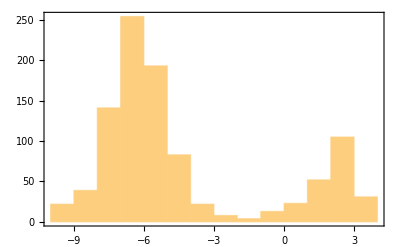

```mathematica
Histogram[Log10[Transpose[testtblCP][[3]]],Frame->True,PlotRange->All]
```

```mathematica
Total[Map[(#<=10^-2)&,Transpose[testtblCP][[3]]]]
```

228 False+772 True

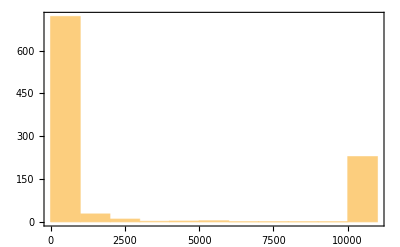

```mathematica
Histogram[Transpose[testtblCP][[4]],Frame->True,PlotRange->All]
```

```mathematica
Histogram3D[Map[{Log10[#[[3]]],#[[4]]}&,testtblCP],PlotRange->All]
```

-Graphics3D-

```mathematica
S3fromcore[RandomReal[{-10,+10},{5}]]
```

{{{-18.2106,4.10942},{-9.63253,1.77594}},{{38.053,-2.7101},{-18.4355,3.84449}}}

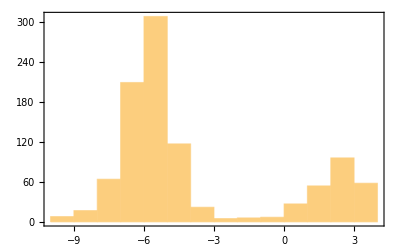

```mathematica
Histogram[Log10[Transpose[testtblCPcored][[3]]],Frame->True,PlotRange->All]
```

```mathematica
Total[Map[(#<=10^-2)&,Transpose[testtblCPcored][[3]]]]
```

248 False+752 True

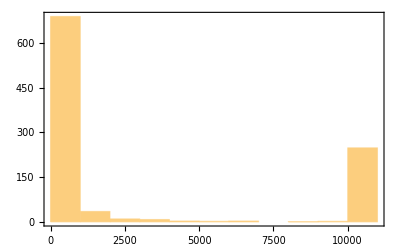

```mathematica
Histogram[Transpose[testtblCPcored][[4]],Frame->True,PlotRange->All]
```

```mathematica
Histogram3D[Map[{Log10[#[[3]]],#[[4]]}&,testtblCPcored],PlotRange->All]
```

-Graphics3D-

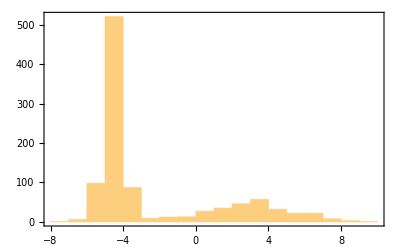

```mathematica
Histogram[Log10[Transpose[testtblCPcore][[3]]],Frame->True,PlotRange->All]
```

```mathematica
Total[Map[(#<=10^-2)&,Transpose[testtblCPcore][[3]]]]
```

278 False+722 True

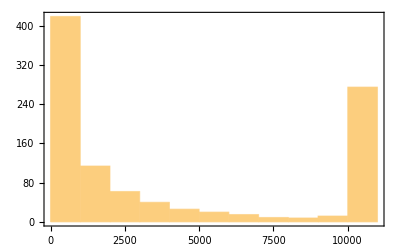

```mathematica
Histogram[Transpose[testtblCPcore][[4]],Frame->True,PlotRange->All]
```

```mathematica
Histogram3D[Map[{Log10[#[[3]]],#[[4]]}&,testtblCPcore],PlotRange->All]
```

-Graphics3D-

```mathematica
rndten=RandomInteger[{-100,+100},{2,2,2}];
While[NormCPDiff[rndten,2]<10^-6,
rndten=RandomInteger[{-100,+100},{2,2,2}]];
rndten
```

{{{71,-5},{-16,-56}},{{-18,-22},{-65,-28}}}

```mathematica
TuckerD[mat_,rank_]:=Chop[ResourceFunction["TuckerDecomposition"][mat,rank]];
```

```mathematica
TuckerD[testten,4]
TuckerD[testten,3]
TuckerD[testten,2]
TuckerD[testten,1]
```

{{{{-43.747,50.6232},{-64.9444,-19.9249}},{{62.7718,17.0162},{-30.5035,4.83647}}},{{{-0.915386,-0.402577},{-0.402577,0.915386}},{{0.311961,-0.950095},{0.950095,0.311961}},{{-0.922173,-0.386779},{-0.386779,0.922173}}}}

{{{{-43.747,50.6232},{-64.9444,-19.9249}},{{62.7718,17.0162},{-30.5035,4.83647}}},{{{-0.915386,-0.402577},{-0.402577,0.915386}},{{0.311961,-0.950095},{0.950095,0.311961}},{{-0.922173,-0.386779},{-0.386779,0.922173}}}}

{{{{-43.747,50.6232},{-64.9444,-19.9249}},{{62.7718,17.0162},{-30.5035,4.83647}}},{{{-0.915386,-0.402577},{-0.402577,0.915386}},{{0.311961,-0.950095},{0.950095,0.311961}},{{-0.922173,-0.386779},{-0.386779,0.922173}}}}

{{{{-79.8712}}},{{{-0.915386},{-0.402577}},{{-0.467973},{0.883743}},{{-0.789926},{-0.613202}}}}

```mathematica
FromTucker[mat_,rank_]:=Module[{core,comps,indices},
{core,comps}=TuckerD[mat,rank];
indices=Prepend[Thread[{-#,#}],#]&@Range[Length[comps]];
Chop[ResourceFunction["EinsteinSummation"][indices,Prepend[comps,core]]]];
```

```mathematica
ShowTucker[mat_,rank_]:=Map[MatrixForm,{mat,FromTucker[mat,rank]}];
```

```mathematica
ShowTuckerDiff[mat_,rank_]:=MatrixForm[mat-FromTucker[mat,rank]];
```

```mathematica
ShowTuckerDiff[testten,4]
ShowTuckerDiff[testten,3]
ShowTuckerDiff[testten,2]
ShowTuckerDiff[testten,1]
```

((-4.26326×10^-14
7.10543×10^-15) | (3.55271×10^-15
2.84217×10^-14)
(3.55271×10^-15
1.06581×10^-14) | (2.84217×10^-14
1.06581×10^-14))

((-4.26326×10^-14
7.10543×10^-15) | (3.55271×10^-15
2.84217×10^-14)
(3.55271×10^-15
1.06581×10^-14) | (2.84217×10^-14
1.06581×10^-14))

((-4.26326×10^-14
7.10543×10^-15) | (3.55271×10^-15
2.84217×10^-14)
(3.55271×10^-15
1.06581×10^-14) | (2.84217×10^-14
1.06581×10^-14))

((43.9727
-25.9807) | (35.0396
-16.3791)
(-29.8863
-31.2271) | (-42.5533
-10.5752))

```mathematica
NormTuckerDiff[mat_,rank_]:=Chop[SquaredEuclideanDistance[Flatten[mat],Flatten[FromTucker[mat,rank]]]];
```

```mathematica
NormTuckerDiff[testten,4]
NormTuckerDiff[testten,3]
NormTuckerDiff[testten,2]
NormTuckerDiff[testten,1]
```

0

0

0

7895.59

```mathematica
Timing[testtblTucker=Table[NormTuckerDiff[RandomReal[{-100,+100},{2,2,2}],2],10000];]
```

{6.3157,Null}

```mathematica
Sort[Tally[Chop[testtblTucker,10^-6]]]
```

{{0,1000}}

## Signatures

```mathematica
sl2={{Subscript[s, 1]^2/2,Subscript[s, 1,2]},{Subscript[s, 1] Subscript[s, 2]-Subscript[s, 1,2],Subscript[s, 2]^2/2}}
```

{{s_1^2/2,s_(1,2)},{s_1 s_2-s_(1,2),s_2^2/2}}

```mathematica
sl2f[s1_,s2_,s12_]:={{s1^2/2,s12},{s1 s2-s12,s2^2/2}};
```

```mathematica
sl3={{{Subscript[s, 1]^3/6,Subscript[s, 1,1,2]},{Subscript[s, 1] Subscript[s, 1,2]-2 Subscript[s, 1,1,2],Subscript[s, 1,2,2]}},{{1/2 (Subscript[s, 1]^2 Subscript[s, 2]-2 Subscript[s, 1] Subscript[s, 1,2])+Subscript[s, 1,1,2],Subscript[s, 2] Subscript[s, 1,2]-2 Subscript[s, 1,2,2]},{1/2 (Subscript[s, 1] Subscript[s, 2]^2-2 Subscript[s, 2] Subscript[s, 1,2])+Subscript[s, 1,2,2],Subscript[s, 2]^3/6}}}
```

```mathematica
sl3f[s1_,s2_,s12_,s112_,s122_]:={{{s1^3/6,s112},{s1 s12-2 s112,s122}},{{1/2 (s1^2 s2-2 s1 s12)+s112,s2 s12-2 s122},{1/2 (s1 s2^2-2 s2 s12)+s122,s2^3/6}}};
```

```mathematica
sl3f[1,2,3,4,5]
```

{{{1/6,4},{-5,5}},{{2,-4},{1,4/3}}}

```mathematica
MatrixForm[sl3f[1,2,3,4,5]]
```

((1/6
4) | (-5
5)
(2
-4) | (1
4/3))

## Example 2.4

```mathematica
sl2x[x11_,x12_,x21_,x22_]:={{x11^2/2+x11 x12+x12^2/2,(x11 x21)/2+(x12 x21)/3+(2 x11 x22)/3+(x12 x22)/2},{(x11 x21)/2+(2 x12 x21)/3+(x11 x22)/3+(x12 x22)/2,x21^2/2+x21 x22+x22^2/2}};
```

```mathematica
sl3x[x11_,x12_,x21_,x22_]:={{{x11^3/6+(x11^2 x12)/2+(x11 x12^2)/2+x12^3/6,(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6},{(x11^2 x21)/6+(x11 x12 x21)/3+(2 x12^2 x21)/15+(x11^2 x22)/6+(11 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6}},{{(x11^2 x21)/6+(5 x11 x12 x21)/12+(4 x12^2 x21)/15+(x11^2 x22)/12+(7 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/6+(x11 x21 x22)/3+(11 x12 x21 x22)/30+(2 x11 x22^2)/15+(x12 x22^2)/6},{(x11 x21^2)/6+(x12 x21^2)/4+(x11 x21 x22)/4+(2 x12 x21 x22)/5+(x11 x22^2)/10+(x12 x22^2)/6,x21^3/6+(x21^2 x22)/2+(x21 x22^2)/2+x22^3/6}}};
```

```mathematica
MatrixForm[{{{x11^3/6+(x11^2 x12)/2+(x11 x12^2)/2+x12^3/6,(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6},{(x11^2 x21)/6+(x11 x12 x21)/3+(2 x12^2 x21)/15+(x11^2 x22)/6+(11 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6}},{{(x11^2 x21)/6+(5 x11 x12 x21)/12+(4 x12^2 x21)/15+(x11^2 x22)/12+(7 x11 x12 x22)/30+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/6+(x11 x21 x22)/3+(11 x12 x21 x22)/30+(2 x11 x22^2)/15+(x12 x22^2)/6},{(x11 x21^2)/6+(x12 x21^2)/4+(x11 x21 x22)/4+(2 x12 x21 x22)/5+(x11 x22^2)/10+(x12 x22^2)/6,x21^3/6+(x21^2 x22)/2+(x21 x22^2)/2+x22^3/6}}}]
```

((x11^3/6+(x11^2 x12)/2+(x11 x12^2)/2+x12^3/6
(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6) | ((x11^2 x21)/6+(x11 x12 x21)/3+(2 x12^2 x21)/15+(x11^2 x22)/6+(11 x11 x12 x22)/30+(x12^2 x22)/6
(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6)
((x11^2 x21)/6+(5 x11 x12 x21)/12+(4 x12^2 x21)/15+(x11^2 x22)/12+(7 x11 x12 x22)/30+(x12^2 x22)/6
(x11 x21^2)/6+(x12 x21^2)/6+(x11 x21 x22)/3+(11 x12 x21 x22)/30+(2 x11 x22^2)/15+(x12 x22^2)/6) | ((x11 x21^2)/6+(x12 x21^2)/4+(x11 x21 x22)/4+(2 x12 x21 x22)/5+(x11 x22^2)/10+(x12 x22^2)/6
x21^3/6+(x21^2 x22)/2+(x21 x22^2)/2+x22^3/6))

```mathematica
coresl3x[x11_,x12_,x21_,x22_]:={x11+x12,x21+x22,(x11 x21)/2+(x12 x21)/3+(2 x11 x22)/3+(x12 x22)/2,(x11^2 x21)/6+(x11 x12 x21)/4+(x12^2 x21)/10+(x11^2 x22)/4+(2 x11 x12 x22)/5+(x12^2 x22)/6,(x11 x21^2)/6+(x12 x21^2)/12+(5 x11 x21 x22)/12+(7 x12 x21 x22)/30+(4 x11 x22^2)/15+(x12 x22^2)/6};
```

## Tests

### Random Tensors

```mathematica
CPErrors123[mat_]:={ShowCPError[mat,1],ShowCPError[mat,2],ShowCPError[mat,3]};
```

```mathematica
CPDiff123[mat_]:={NormCPDiff[mat,1],NormCPDiff[mat,2],NormCPDiff[mat,3]};
```

```mathematica
TuckerDiff123[mat_]:={NormTuckerDiff[mat,1],NormTuckerDiff[mat,2],NormTuckerDiff[mat,3]};
```

```mathematica
AllDiffs123[mat_]:={NormCPDiff[mat,1],NormTuckerDiff[mat,1],NormCPDiff[mat,2],NormTuckerDiff[mat,2],NormCPDiff[mat,3],NormTuckerDiff[mat,3]};
```

```mathematica
RandomReal[{-100,100},{2,2,2}]
```

{{{-35.7165,-4.66017},{-70.3223,-97.2091}},{{19.9418,59.5622},{43.8926,-34.0347}}}

```mathematica
Timing[tblDiffsrnd=Table[AllDiffs123[RandomReal[{-100,100},{2,2,2}]],1000];]
```

{407.612,Null}

```mathematica
TableForm[Map[Quartiles,Transpose[tblDiffsrnd]]]
```

72.5332 | 90.9842 | 108.61
73.3152 | 92.0817 | 109.21
0.0000390246 | 0.000120599 | 0.876549
0 | 0 | 0
5.75735×10^-7 | 4.6245×10^-6 | 0.0000267939
0 | 0 | 0

```mathematica
TableForm[Map[Quantile[#,0.99]&,Transpose[tblDiffsrnd]]]
```

157.548
154.372
40.6745
0
0.000235676
0

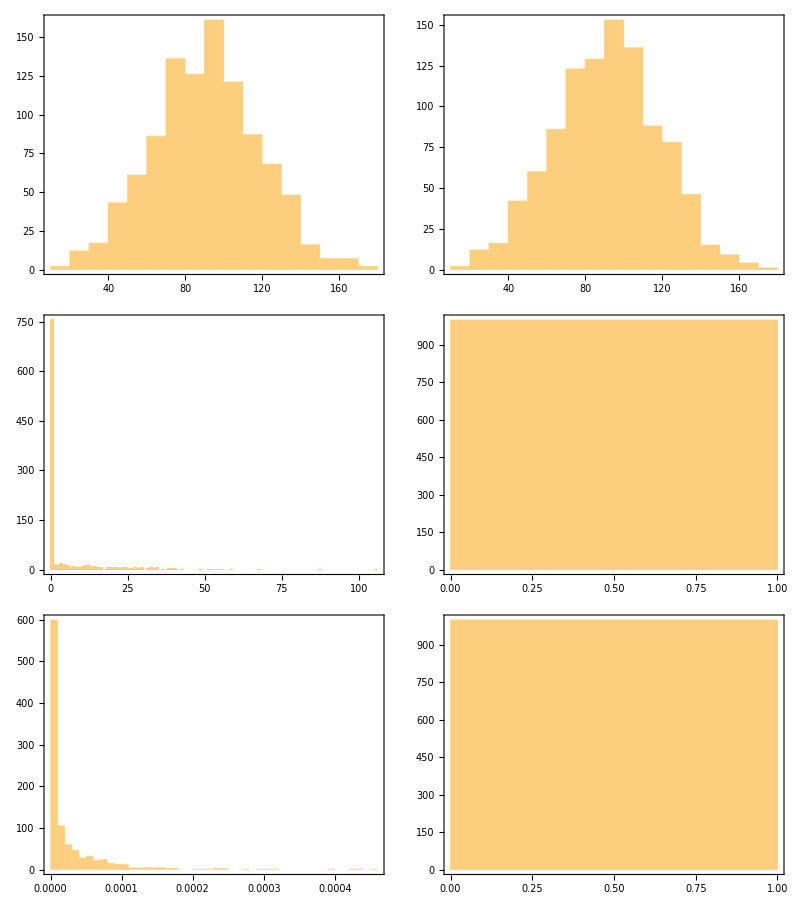

```mathematica
TableForm[ArrayReshape[Map[Histogram[#,Frame->True,PlotRange->All,ImageSize->Medium]&,Transpose[tblDiffsrnd]],{3,2}]]
```

```mathematica
xr=RandomReal[{-1,1},{2,2,2}]
```

{{{-0.946114,-0.689697},{-0.796852,-0.568032}},{{0.799586,-0.402902},{-0.241119,-0.882481}}}

```mathematica
xrs=ReplacePart[xr,{1,2,2}->s122]
```

{{{-0.946114,-0.689697},{-0.796852,s122}},{{0.799586,-0.402902},{-0.241119,-0.882481}}}

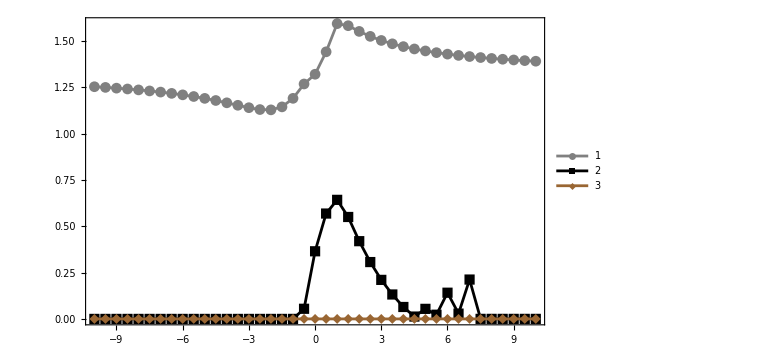

```mathematica
DiscretePlot[{
NormCPDiff[xrs,1],
NormCPDiff[xrs,2],
NormCPDiff[xrs,3]},
{s122,-10,10,1/2},PlotRange->{{-10,10},All},AxesOrigin->{0,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,3},
PlotStyle->{Gray,Black,Brown},
ImageSize->Large,Frame->True]
```

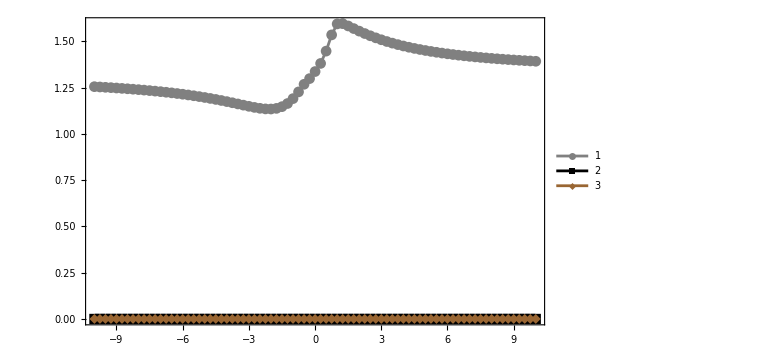

```mathematica
DiscretePlot[{
NormTuckerDiff[xrs,1],
NormTuckerDiff[xrs,2],
NormTuckerDiff[xrs,3]},
{s122,-10,10,1/4},PlotRange->{{-10,10},All},AxesOrigin->{0,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,3},
PlotStyle->{Gray,Black,Brown},
ImageSize->Large,Frame->True]
```

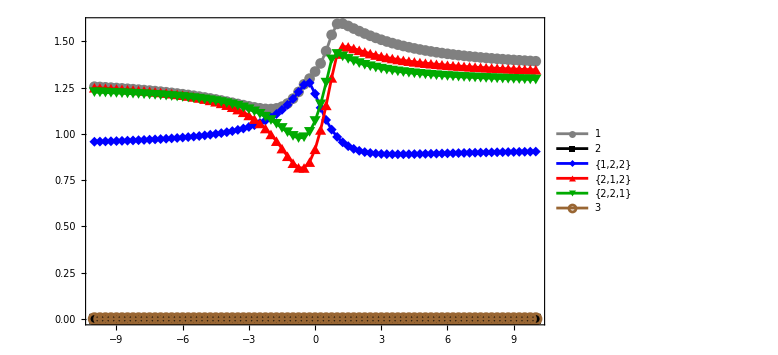

```mathematica
DiscretePlot[{
NormTuckerDiff[xrs,1],
NormTuckerDiff[xrs,2],
NormTuckerDiff[xrs,{1,2,2}],
NormTuckerDiff[xrs,{2,1,2}],
NormTuckerDiff[xrs,{2,2,1}],
NormTuckerDiff[xrs,3]},
{s122,-10,10,1/4},PlotRange->{{-10,10},All},AxesOrigin->{0,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,"{1,2,2}","{2,1,2}","{2,2,1}",3},
PlotStyle->{Gray,Black,Blue,Red,Darker[Green],Brown},
ImageSize->Large,Frame->True]
```

### Generic (Core) Signatures

```mathematica
Apply[sl3f,Append[Most[Apply[coresl3x,RandomReal[{-10,10},{4}]]],RandomReal[{-10,10}]]]
```

{{{4.41726,-4.69719},{0.456693,-7.85831}},{{-20.7541,32.5743},{22.4273,-29.6396}}}

```mathematica
Timing[tblDiffsrndCore=Table[AllDiffs123[Apply[sl3f,Append[Most[Apply[coresl3x,RandomReal[{-10,10},{4}]]],RandomReal[{-10,10}]]]],1000];]
```

{576.485,Null}

```mathematica
TableForm[Map[Quartiles,Transpose[tblDiffsrndCore]]]
```

12.3763 | 33.3101 | 98.2529
12.3763 | 33.3129 | 98.2747
0.000102351 | 0.000486926 | 0.366124
0 | 0 | 0
1.38409×10^-6 | 0.0000154118 | 0.0000627003
0 | 0 | 0

```mathematica
TableForm[Map[Quantile[#,0.99]&,Transpose[tblDiffsrndCore]]]
```

626.607
626.915
83.4789
0
0.000636726
0

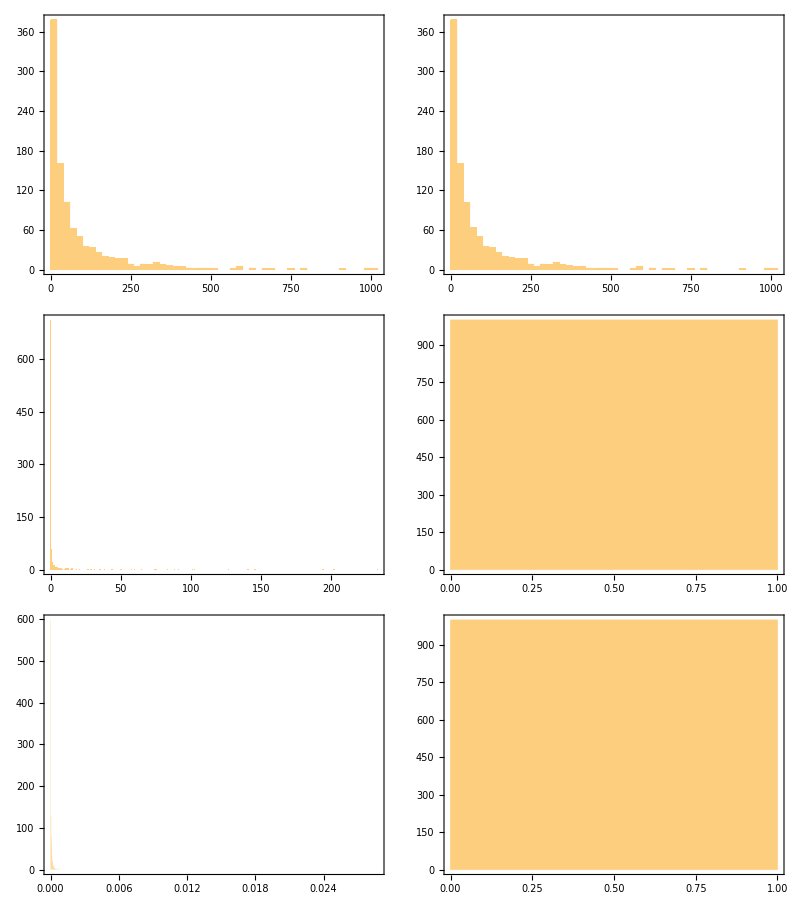

```mathematica
TableForm[ArrayReshape[Map[Histogram[#,Frame->True,PlotRange->All,ImageSize->Medium]&,Transpose[tblDiffsrndCore]],{3,2}]]
```

### Example 2.4

```mathematica
sl2x[1,2,-3,1]
```

{{9/2,-11/6},{-25/6,2}}

```mathematica
sl3x[1,2,-3,1]
```

{{{9/2,-89/60},{-38/15,19/20}},{{-299/60,53/30},{197/60,-4/3}}}

```mathematica
Timing[tblDiffsrndE24=Table[AllDiffs123[Apply[sl3x,RandomReal[{-10,10},{4}]]],1000];]
```

{839.373,Null}

```mathematica
TableForm[Map[Quartiles,Transpose[tblDiffsrndE24]]]
```

0.676641 | 3.21385 | 8.4927
0.676641 | 3.21405 | 8.49576
0.00334971 | 0.0565487 | 0.299067
0 | 0 | 0
0.0000281834 | 0.000130651 | 0.00035709
0 | 0 | 0

```mathematica
TableForm[Map[Quantile[#,0.99]&,Transpose[tblDiffsrndE24]]]
```

25.5513
25.5513
6.83177
0
0.0036526
0

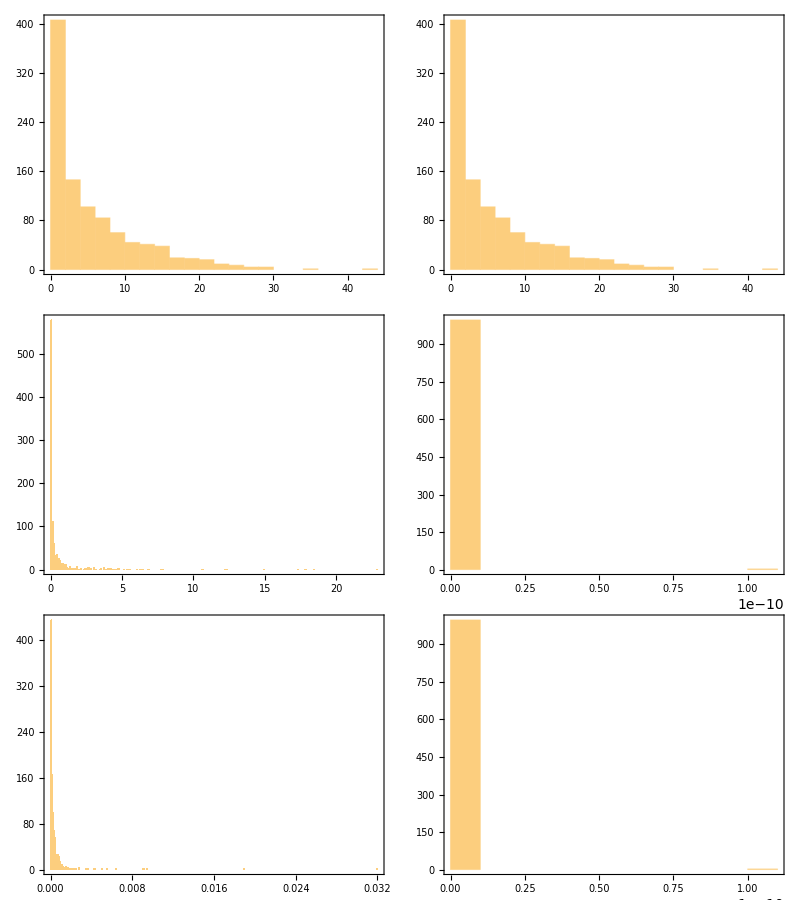

```mathematica
TableForm[ArrayReshape[Map[Histogram[#,Frame->True,PlotRange->All,ImageSize->Medium]&,Transpose[tblDiffsrndE24]],{3,2}]]
```

### Investigations

```mathematica
coresl3x[1,2,-3,1]
```

{3,-2,-11/6,-89/60,19/20}

```mathematica
N[ShowTucker[sl3x[1,2,-3,1]]]
```

{((4.5
-1.48333) | (-2.53333
0.95)
(-4.98333
1.76667) | (3.28333
-1.33333)),((4.5
-1.48333) | (-2.53333
0.95)
(-4.98333
1.76667) | (3.28333
-1.33333))}

```mathematica
N[ShowTucker[sl3f[3,-2,-11/6,-89/60,19/20]]]
```

{((4.5
-1.48333) | (-2.53333
0.95)
(-4.98333
1.76667) | (3.28333
-1.33333)),((4.5
-1.48333) | (-2.53333
0.95)
(-4.98333
1.76667) | (3.28333
-1.33333))}

```mathematica
sl3f[3,-2,-11/6,-89/60,1]
```

{{{9/2,-89/60},{-38/15,1}},{{-299/60,5/3},{10/3,-4/3}}}

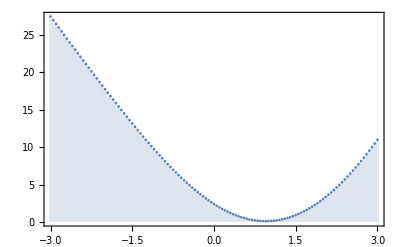

```mathematica
DiscretePlot[NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{1,2,2}],
{s122,-3,3,1/20},AxesOrigin->{19/20,0},Frame->True]
```

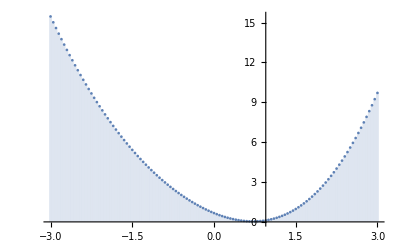

```mathematica
DiscretePlot[NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,1,2}],
{s122,-3,3,1/20},AxesOrigin->{19/20,0}]
```

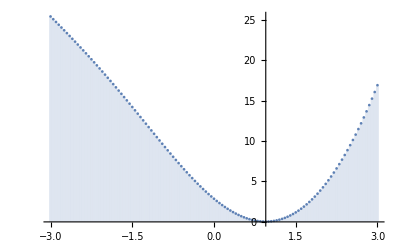

```mathematica
DiscretePlot[NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,2,1}],
{s122,-3,3,1/20},AxesOrigin->{19/20,0}]
```

```mathematica
ShowTuckerDiff[sl3f[3,-2,-11/6,-89/60,19/20],{1,2,2}]
```

((0.132625
0.0175565) | (0.161465
-0.110988)
(0.11364
0.0150434) | (0.138352
-0.0951006))

```mathematica
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,19/20],{1,2,2}]
```

0.31243

```mathematica
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,19/20]]
```

0

```mathematica
TableForm[Table[{r,NormCPDiff[sl3f[3,-2,-11/6,-89/60,19/20],r]},{r,1,3}]]
```

1 | 0.353855
2 | 0.0128918
3 | 0.00158359

```mathematica
TableForm[Table[{r,ShowCPError[sl3f[3,-2,-11/6,-89/60,19/20],r]},{r,1,3}]]
```

1 | 0.125213
2 | 2.72915×10^-6
3 | 1.26069×10^-8

```mathematica
TableForm[Table[{r,ShowCPError[sl3f[3,-2,-11/6,-89/60,1],r]},{r,1,3}]]
```

1 | 0.15222
2 | 0.000742411
3 | 5.72916×10^-14

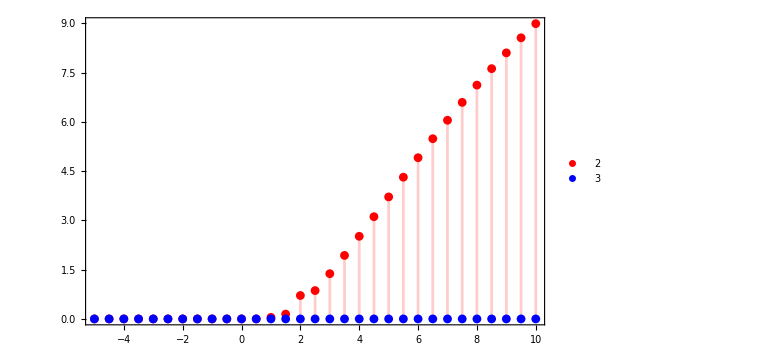

```mathematica
DiscretePlot[{
ShowCPError[sl3f[3,-2,-11/6,-89/60,s122],2],
ShowCPError[sl3f[3,-2,-11/6,-89/60,s122],3]},
{s122,-5,10,1/2},PlotRange->{{-5,10},All},AxesOrigin->{19/20,0},Filling->Axis,
PlotLegends->{2,3},PlotStyle->{Red,Blue},
ImageSize->Large,Frame->True]
```

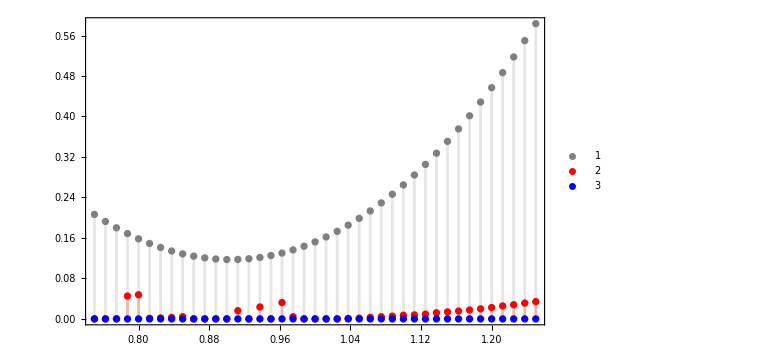

```mathematica
DiscretePlot[{
ShowCPError[sl3f[3,-2,-11/6,-89/60,s122],1],
ShowCPError[sl3f[3,-2,-11/6,-89/60,s122],2],
ShowCPError[sl3f[3,-2,-11/6,-89/60,s122],3]},
{s122,3/4,5/4,1/80},PlotRange->{{3/4,5/4},All},AxesOrigin->{19/20,0},Filling->Axis,
PlotLegends->{1,2,3},PlotStyle->{Gray,Red,Blue},
ImageSize->Large,Frame->True]
```

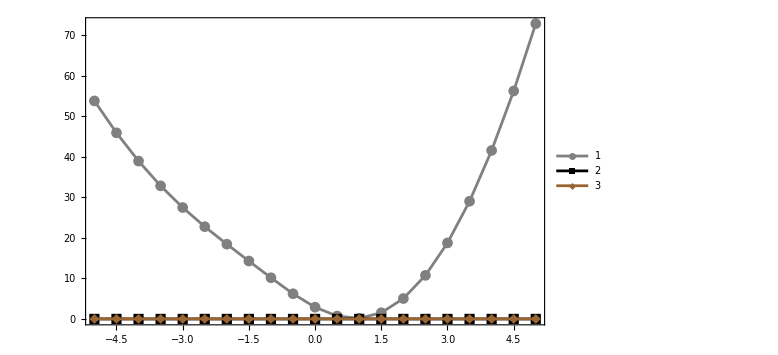

```mathematica
DiscretePlot[{
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],1],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],2],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],3]},
{s122,-5,5,1/2},PlotRange->{{-5,5},All},AxesOrigin->{19/20,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,3},
PlotStyle->{Gray,Black,Brown},
ImageSize->Large,Frame->True]
```

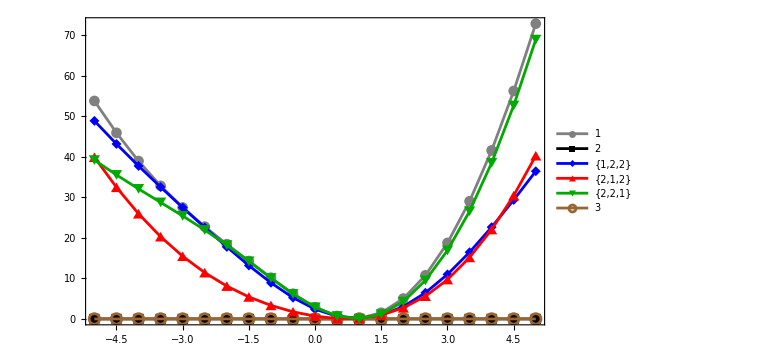

```mathematica
DiscretePlot[{
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],1],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],2],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{1,2,2}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,1,2}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,2,1}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],3]},
{s122,-5,5,1/2},PlotRange->{{-5,5},All},AxesOrigin->{19/20,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,"{1,2,2}","{2,1,2}","{2,2,1}",3},
PlotStyle->{Gray,Black,Blue,Red,Darker[Green],Brown},
ImageSize->Large,Frame->True]
```

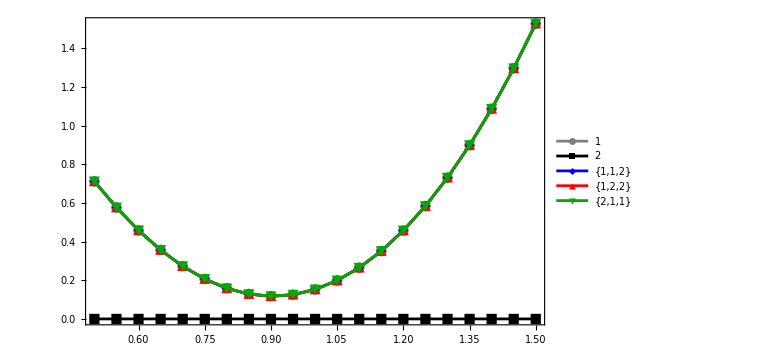

```mathematica
DiscretePlot[{
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],1],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],2],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{1,1,2}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{1,2,1}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,1,1}]},
{s122,1/2,3/2,1/20},PlotRange->{{1/2,3/2},All},AxesOrigin->{19/20,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,"{1,1,2}","{1,2,2}","{2,1,1}"},
PlotStyle->{Gray,Black,Blue,Red,Darker[Green]},
ImageSize->Large,Frame->True]
```

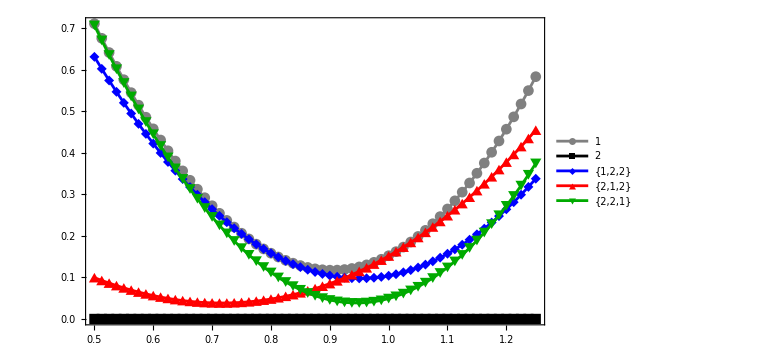

```mathematica
DiscretePlot[{
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],1],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],2],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{1,2,2}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,1,2}],
NormTuckerDiff[sl3f[3,-2,-11/6,-89/60,s122],{2,2,1}]},
{s122,1/2,5/4,1/80},PlotRange->{{1/2,5/4},All},AxesOrigin->{19/20,0},
Filling->None,Joined->True,PlotMarkers->Automatic,
PlotLegends->{1,2,"{1,2,2}","{2,1,2}","{2,2,1}"},PlotStyle->{Gray,Black,Blue,Red,Darker[Green]},
ImageSize->Large,Frame->True]
```